Theory

#### Vector spaces

#### Subsubsection. Force vector

The force acts in the direction
								 OverHat[F̲](θ_0)=-cos(θ_0) (e̲)_1+sin(θ_0) (e̲)_2,
where θ_0∈[0,π]. We are going to say that we cannot peel the film at angles at greater than π or less than 0. This is something we are simply going to assume, even though at certain a values we might be able to pull in directions with θ_0<0 and θ_0>π (locally).

#### Subsubsection. Tangent Vector

We  define the tangent  to the surface as

T̲(s):=(d r̲)/(d s)
=d/(d s) (x (s)"e_1"+ y(s)"e_2")
Let's say that x=s,  then x(s)=s, y(s)=f(s), and we get  T̲(s)="e_1"+f'(s)"e_2", or alternately, as T̲(x)="e_1"+f'(x)"e_2". We define OverHat[T̲](x):=("e_1"+f'(x)"e_2")/(1+f'(x)^2)^(1/2), where by (·)^(1/2): ℝ_(≥ 0)→ℝ_(≥ 0) is the   positive square root function.

#### Subsubsection. Rotation tensor

Orth^+ is the set of all rotation operators on  𝔼.
The expression R[θ, e̲] , where  R̲: (-π, π] × 𝔼 -> (Orth^+),  
denotes a linear operator on 𝔼  that rotates a vector about the vector e̲ in the counter clockwise direction by θ radians. For examples, for example R[θ,(e̲)_3]

R̲(θ,(e̲)_3)=cos(θ)(e̲)_1⊗ (e̲)_1+sin(θ) (e̲)_2⊗ (e̲)_1+cos(θ)(e̲)_2⊗(e̲)_2-sin(θ)(e̲)_1⊗(e̲)_2

#### Subsubsection. Effective peeling angle

ψ_hk∈(-π,  π] is defined such that 
R[ψ_hk,e_3].OverHat[F̲][θ_0]=-OverHat[T̲](x) or equivalently
R[-ψ_hk].-OverHat[T̲](x)=OverHat[F̲][θ_0],

For no local penetration it is required that 0≤  ψ_hk ≤  π. For penetration the condition is -π<  ψ_hk <  0.

#### Subsubsection. Hello"f'_max"

"f'_max"= max {f'(x) : 0≤ x< λ}
"f'_min" = min {}

#### Subsubsection Tangent angle

The tangent angle at the location x is the unique number 
θ_t(x)∈(-π,  π]  such that
 R[θ_t(x), (e̲)_3].(e̲)_1= OverHat[T̲](x). 
 
The angle between a̲ and b̲ is θ∈[-π,π] such that
  R[θ_t(x), (e̲)_3].a̲=b̲ 

Since we represent the surface as a function, it can be shown that  θ_t(x)  in fact ∈ (-π/2,  π/2). 

Consequently, it can be shown that θ_t(x)=ArcTan[f'[x]]

#### Subsubsection Max and min angle

We know that 
 			ψ_hk = θ_0+θ_t[𝒻,a].----------(*)
 
 (Numerical proof done)

Cos[ψ_hk-θ_0]=Cos[θ_t](follows from *)
Sin[ψ_hk-θ_0]=Sin[θ_t] (also follows *)
Tan[ψ_hk - θ_0]=Tan[θ_t] (follows from previous two equations)

We start from our definition of θ_0, as per which 0≤ θ_0≤ π. Adding -θ_t[𝒻,a] to both sides of the above inequality we get

-θ_t[𝒻,a]≤ θ_0≤  π-θ_t[𝒻,a]-------(#) for all a

By definition of the max and min operations we have that 

"θ_t[𝒻,a]≤ max_a θ_f[𝒻,a]"
θ_t[𝒻,a]≥ min_a θ_t[𝒻,a]

Multiplying the last two inequalities with negative unity we get

-θ_t[𝒻,a]≥ -max_aθ_t[𝒻,a]-----(*)
-θ_t[𝒻,a]≤ -min_aθ_t[𝒻,a]-------(**)

Adding π to (*) on both sides we get  π-θ_t[𝒻,a]≥ π-max_a θ_t[𝒻,a], on   re-writing which using the ≤ sign we get

π-max_a θ_t[𝒻,a]≤ π-θ_t[𝒻,a]-----(*.1)

It follows from (*.#), (*.1), and (**) that

-min_a θ_t[𝒻,a]≤  θ_0  ≤ π-max_a θ_t[𝒻,a]


Rotation (in the counter clock wise direction) of F

Calculations

```mathematica
Off[Unset::norep];
Names@{"Global`*","ComplexSymbols`*"};
ClearAll[#] & /@(%);
Remove[#] &/@(%%);
```

```mathematica
<<Notation`
Symbolize[UnderBar[x_]]
Symbolize[OverHat[x_]]
Symbolize[Subscript[x_, y_]]
```

```mathematica
ProblemHK="WavyPeeling`";
Module[{x},x=ToExpression[ProblemHK~~"sympaltte"];
If[ValueQ[x],NotebookClose[x]]];
Quiet[Remove[#] ]& /@ {ProblemHK~~"*"};
Begin["WavyPeeling`"];
If[ValueQ[sympaltte],NotebookClose[sympaltte]];
Quiet[ClearAll[#] ]& /@ {ProblemHK~~"*"};
Get[URLDownload["https://raw.githubusercontent.com/haneeshk/ForBetterMMAExperience/master/ComplexSymbols.wl"]];
syms=AssignLabels[{"e_1","e_2","e_3","u","","(*GraphicsBox[{Thickness[0.05546311702717693], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {CompressedData["
1:eJxdlG1IU1EYx2dMw9Q5N3edtTmnK7v3lmkTkyj2X1aaBIpZWUlv4lQsLfKD
ipL4Sq4XESsrqeiFFb2wPlgqZUSUWfZCFoIFZX3RXqRETFNcnnvu7qAHLpff
vef8z/95znOOcW9Res4cmUy2YfYh74yffb9bBjVwkfikx/FMe6pXGkP5sAG9
JI4yeFBU/vPMyXCJt/oy9eZdRokTG6tVtk4jZCQqGeTaZoOJQPumlZmuXAaf
1+2ynj0YgTzy3YfBtfHhkt7GSJE1iOGuq9/UmLBjYabu1X011dm9EI/sXVVx
l4Ow1GgY23d3kbheANIGFpTvaVosse78TvaFk5XYGV142esjiyxBL4Dm42JR
E1Lhne+jgM4xlBxt4ES/Cjo+i8NQxdeC10sCRR0OJ0g9lEqcbgwsi7/BIWrU
NHz2iBK7M9KjLva4/wdh47O5q8+951D6aWLAbPew8N+pRndn+zGfNxxuq5Yo
csM0uIeqL91aDuGdF7tyRhg019du77vPIs48G+oQVMqfnIi9xyL55hOHLMHD
tJ4e/lG33758ysPq0qbil1e0WLHqQfqpQRYGQV9L6xPDwSzoh1I/aRzKiF8+
FMFHU77Jiz3szt/N7nyE/Hu0ok+e7k+iVqwnj/XEbwsj6vPYLtQ/WNTjqT+5
WmJaL5XEQp8EqZD0sEKfUM9L+18+6kwrKOORRPQnlJD7NhiyC3lsIv1rVWIZ
6Y8tPK4OOL7GJgZKftz7LYwf4dCW4kxonfTHMtJvVzgccBQ7Z1L9aX6bOdGH
H13vLwt/qyKlhfXD90Ntmim7h58/XnMrP8zDeUW/anveRUF3h7kwJ1xBOWOR
2PdKOn7GJK3feimyY7rbBD9hvi/iyX5ZTbT/fnhjLTlPDZG0by1e+MDqb7qq
I5Dcltqd7TNtEeqw2Ii3U0/7z2+btFDfBtiEmLCUCHUNg7ZK1xzT90dkvcTC
/BadxPT8z0cK0a+btAjnAqGi32lLOZn/PQT9AR+YnHEZxrp+t+WOa8T8vXGG
REeweJ7mSSzcA7Ygid394Nb///75B4zd9Nw=
"], CompressedData["
1:eJxTTMoPSmViYGCQBWIQPRMEfgo5zAHTMg4PXOMdZwkKQehCSYczIOAj4BDy
9vLHGQtFHRhAoIELzu+L6PZn3MAG5wc88bxkepnZIQ0Ejok5RKtGyJyrYXIQ
rpxUcjZFwmG71waLOTsZIeY4SDr0g/QXMEL0O0qh8aXhfPc1R5czzJBx4Hbk
85rxkhHqXlmHL/s+bk2fxuTwpi232yhaHm5/9f0ft4xfKzjEgOzfw+qwVkiH
L11PCeKfHk6HSpC8tbLDi9rH2effcDuAw+GmsoPqJ5WXs07yQfiRKlBzBBy2
mP84lNKlAnGPgKDDq+Ktor+zVSDu+iHo4DKhWSitS9mhXYFd9cwVIYdOG89d
aYuUHILB/hCG8hUd0sEBI+yw8tvLijMOig4mxkBQLOzwYdF6hbM3FOB8sHwB
gg/xv7yDwq4F+1L9hB32d+9rMnGWc0CPPwBSiMkB
"]}], FilledCurveBox[CompressedData["
1:eJxTTMoPymNmYGBgBGJ5IAaxQYAJSjNCxZiR+OjixKihRC8l5g+UOKlqADSm
AmU=
"], CompressedData["
1:eJxTTMoPSmVmYGBgBGIXIGYCYucJzUJpXUoOMaoRMuf2yDl8WLRe4ayGssPK
by8rzjgoOWxQfdI8z1cFzn+auPCayXk1h7VCOnzpekoO60HyuRoOtzVl1/xn
VnL4DwL1Gg7paUAghuCfAQEfJYdUkHibhsNMEOhUcgi4JV2TOEkDYv4BJYdT
h53WZs7TcHBfc3Q5ww8lB+l5cZqnN2g4iFROKjlrouyQEBKkvuCkhoPKtUfB
DDnKDpPbW6Mu79GAuKdOGeI+f3UHBhBIUHY4sWtHL5uBGtT9ynBxGN8DZM8J
ZQefE+y2s01VIfIPlB1eZGl/mz5X1SEQ5L4iFYg9NhoOG/TyFjPuUYGGgwYk
fN6qw/lvireK/tbWdmjm9V8/pRWTfxzkPzttuD9hfJh+/4sTY/45a0PCiU3T
4TjI/QHaUPs1HaaA6BhtaLhrOjwB6cvXdtDXWil8YYmmg/v+WlmLdm2Hmk8b
ArJ/aTqcvxr2Rr9aGxL+PFoOM0DhLqkNiZf/mhDxHi24epg6GB8WPjA+LF5g
/BWgcJygBNeHzgeni2aEemVwvCHiGaxORslBbvkLD73/ag6V93/cMt6tCI+P
8sPbXGfWKsDTJ1i/jIKD+ieVl7M0pR12BFtF/E+XdwAFV9oxcWh6k3MwMQYB
UThfYdeCfal8og5/0fhv2nK7jaLl4erBVLMCnN8CijdWdVR+K4L/GhS/3BoQ
+9VE4fkBZj4s/aOo74am13sIPtgd0mIO2x2aHh2foeHQqsCuemaKmIMBOF41
HPoiuv0ZBcTh6R3mX1i6AYeDugQ8f4DzV6SEQzyUPwPKh+QHVbh+cPj+VYTz
H7jGO876qOhQDYqH1xKQ+K6AxucbWQf08gIAkyDgpA==
"]], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, CompressedData["
1:eJxTTMoPSmVmYGBgBGJtIGYC4oI13bczJhg4yO9asC/VT9ABxndfc3Q5wwxB
h416eYsZawwc+iO6/RkvCDr0B5eoTM9H8Jfc38c3JxnBf56l/W16LFT/DkEH
YxAINnDYGWwV8b9d0EFfa6XwhRR9h9Q0IFDjhaifqwvni/R4vWIJQfBTYu+4
MVfowPkJIUHqC05qO8SoRsics+GH89U/qbycxSkE54PdUyDsUPNpQ0C2lI6D
Ash/58Qg/Fs6DiDj0o5JOJwBgR5diP/7pBy2OjQ9Oh6h5xDw9vLHGYrSDi0s
R/sNvyP4cxYp7/yjrg/n/3n7+oDlY32IfyWkHdLB7jRwOA8yV0cK4u5l+g4i
lZNKzrJIOfz5VvpgTqE+JDzYJeF8YZB8igScPxMEKsUdzl8Ne6N/W9/BA2S+
hbhDMig8OAzg/OUvPPT+CyL43G6qpUxVBg5uIH4Egg8OH09JOH8GyHxLaQf3
/bWyFs9h7pNxMAHF12c9OB/sno06cP5/EKjXcggB+X+hOJwPDj89YTgfbJ+m
ACS82rUd7Esca0/HcDu8Kd4q+ttbF85/krjwmsl5fTgflv7A4fFEwAE9fQIA
vSgmPg==
"]]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{18.0319800747198, 16.338709838107096`},PlotRange->{{0., 18.03}, {0., 16.34}}])","∇u","f'_min","f'_max","(a, f(a))", "λ","μ","I","n_sd","^1u","^2u","^3u"}];
sympaltte=SymbolPalette["syms",syms,1];
"n_sd"=3;
"I"=Table[KroneckerDelta[i,j],{i,1,"n_sd"},{j,1,"n_sd"}];

End[];
AppendTo[$ContextPath, "SphereTranslation`"];
$ContextPath=DeleteDuplicates[$ContextPath];
```

Complex Symbols Package Loaded

```mathematica
pltStyles=;
(*AspectRatio->1/Subscript[a, max],*)

a::usage="Interface delamination length";
Subscript[e̲, 1]::usage="Basis vector for 𝔼";
Subscript[e̲, 2]::usage="Basis vector for 𝔼";
Subscript[e̲, 1]:={1,0};
Subscript[e̲, 2]:={0,1};
ϱ[x_]=(Sin[2π x]+1/(√3) Sin[4π x]);
NMaxValue[{ϱ[x],0≤ x≤1},x];
ϱ[x_]=1/Evaluate[%] ϱ[x];
f[λ_,A_]:=Function[{a}, A λ ϱ[a/λ] ]
OverHat[F̲][Subscript[θ, 0]:_]:= -Cos[Subscript[θ, 0]] Subscript[e̲, 1]+Sin[Subscript[θ, 0]] Subscript[e̲, 2];
T̲[𝒻_,a_]:=Subscript[e̲, 1]+𝒻'[a] Subscript[e̲, 2];
OverHat[T̲][𝒻_,a_]:=(T̲[𝒻,a])/((1+𝒻'[a]^2)^(1/2));
Subscript[l, p][𝒻_,a_]:=NIntegrate[(1+𝒻'[x]^2)^(1/2),{x,0,a}];

Subscript[ψ, wd][Subscript[θ, 0]:_,𝒻_,a_]:=Subscript[θ, 0]+ArcTan[𝒻'[a]];

Subscript[ψ, hk][Subscript[θ, 0]:_,𝒻_,a_]:=Module[{sol,θ},
sol=Solve[{(#==0),-π< θ≤  π},θ]&/@Flatten[RotationMatrix[θ].OverHat[F̲][Subscript[θ, 0]]+OverHat[T̲][𝒻,a]];
Return[(Intersection@@Round[θ/.sol,10^-5])[[1]]//N];
Remove[θ,sol];

]

ClearAll[Subscript[θ, t]];
Subscript[θ, t][𝒻_,a_]:=Module[{θ},
sol=Solve[{(#==0),-π/2< θ < π/2},θ]&/@Flatten[RotationMatrix[θ].Subscript[e̲, 1]-OverHat[T̲][𝒻,a]];
Return[Apply[Intersection,Round[θ/.sol,10^-10]][[1]]];
Remove[θ]
]
```

```mathematica
ClearAll[check]
check[a_]:=Module[{Subscript[θ, 0]=π/3,A=0.5,λ=1,𝒻},
𝒻=f[λ,A];
Return[{Subscript[ψ, wd][Subscript[θ, 0],𝒻,a],Subscript[ψ, hk][Subscript[θ, 0],f[λ,A],a],(Subscript[θ, 0]+Subscript[θ, t][𝒻,a])//N}];
Remove[A,λ,Subscript[θ, 0],𝒻];
];
```

```mathematica
Manipulate[check[a],{a,0,2}]
```

```mathematica
Fig[Subscript[θ, 0]:_,a_:1,Subscript[a, max]:_:10]:=Module[{A=.5,λ=1,Subscript[l, d]=0.2,𝒻},
𝒻=f[λ,A];
"(a, f(a))"={a,𝒻[a]};

plt1=Plot[{𝒻[s],𝒻[a],-1},{s,0,Subscript[a, max]},PlotStyle->pltStyles,
PlotRange->{{0,Subscript[a, max]},{- A λ,2 A λ}}];

plt3=Plot[𝒻[s],{s,a,Subscript[a, max]},
PlotRange->{{0,Subscript[a, max]},{- A λ,2 A λ}},PlotStyle->pltStyles[[4]]];
θLabel=Text[Grid[{{"θ_0"},{ToString[Subscript[θ, 0]/π]~~" π"}}],"(a, f(a))"-0.2 Subscript[e̲, 1]+0.1 Subscript[e̲, 2],Automatic,{1,0}];

ψLabel=Text[Grid[{{"ψ_hk"},{ToString[(Subscript[ψ, hk][Subscript[θ, 0],𝒻,a])/π]~~" π"}}],"(a, f(a))"+0.2 Subscript[e̲, 1]-0.1 Subscript[e̲, 2],Automatic,{1,0}];

plt2=Graphics[{
{Red,PointSize[0.02],Point["(a, f(a))"]},
θLabel,ψLabel,
{Blue, Thick,Arrow[{"(a, f(a))","(a, f(a))"+Subscript[l, p][𝒻,a]OverHat[F̲][Subscript[θ, 0]]}]},{Orange, Thick,Arrow[{"(a, f(a))","(a, f(a))"+Subscript[l, d] OverHat[T̲][𝒻,a]}]}}];
Return[Show[{plt1,plt2,plt3}]];
Remove[A,λ,Subscript[l, d],𝒻];
]


(*Module[{A=.5,λ=1,Subscript[l, d]=0.2,𝒻},
𝒻=f[λ,A];
"(a, f(a))"={a,𝒻[a]};
Plot[ArcTan[f[1,0.5]'[a]]/π,{a,0,1},PlotStyle->{Dashed,Red}]
sol=NMinimize[{ArcTan[f[1,0.5]'[a]]/π,0≤ a≤ 1},a]
NMaximize[{ArcTan[f[1,0.5]'[a]]/π,0≤ a≤ 1},a]
*)
```

-Graphics-

```mathematica
Manipulate[Fig[Subscript[θ, 0],x,2],{Subscript[θ, 0],0,π},{x,0,2}]
```

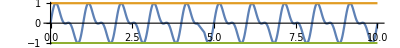

```mathematica
Module[{A=1,λ=1,xmax=10},
Plot[{f[λ,A][x],1,-1},{x,0,xmax},AspectRatio->1/xmax]]
```

```mathematica
Module[{A=.05,λ=10},
Echo[" ",NMaximize[{(Sin[2π x]+2 Sin[4π x]), 0≤ x≤ 20},x]];
Echo[" ",NMaximize[{y[λ,A]'[x], 0≤ x≤ 20},x]];
Echo[" ",NMinimize[{y[λ,A]'[x], 0≤ x≤ 20},x]];
Echo[" ",NMaximize[{y[λ,A][x], 0≤ x≤ 20},x]];
]
```

{2.73582,{x→12.1379}}

NMaximize::nnum: The function value -y[10,0.05]'[0.914636] is not a number at {x} = {0.914636}.

General::stop: Further output of NMaximize::nnum will be suppressed during this calculation.

NMaximize[{y[10,0.05]'[x],0≤x≤20},x]

NMinimize::nnum: The function value y[10,0.05]'[0.914636] is not a number at {x} = {0.914636}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

NMinimize[{y[10,0.05]'[x],0≤x≤20},x]

NMaximize[{y[10,0.05][x],0≤x≤20},x]

```mathematica
?NMaximize
```

```mathematica
ClearAll[check]
BoundsTheta[a_]:=Module[{Subscript[θ, 0]=π/3,A=0.5,λ=1,𝒻},
𝒻=f[λ,A];
Subscript[θ, t][𝒻,a]

];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

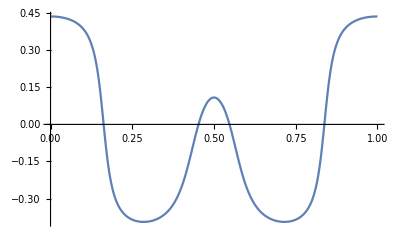

```mathematica
Plot[BoundsTheta[a]/π//N,{a,0,1}]
```

```mathematica
Sqrt[4]
4^(1/2)
```

2

2

```mathematica
Show[Out[208],Out[214]]
```

Show::gcomb: Could not combine the graphics objects in Show[%208,%214].

Show[%208,%214]

```mathematica
NotebookDirectory[]
```

/Users/haneeshkesari/Computational-Solid-Mechanics/WavyPeelingThinFilm/

```mathematica
CreateCounterBoxDialog
```

CreateCounterBoxDialog

```mathematica
CellPrint[Cell[BoxData[CounterBox["subsection"]]]]
```

subsection

#### Subsubsection. Proof that π/2≤ θ_t≤ π/2.

```mathematica
RotationMatrix[Subscript[θ, t]].{1,0}
```

{Cos[θ_t],Sin[θ_t]}

```mathematica
{Cos[Subscript[θ, t]],Sin[Subscript[θ, t]]}={1/((1+𝒻'[x]^2)^(1/2)),𝒻'[x]/((1+𝒻'[x]^2)^(1/2))}
```

The above calculations shows that Cos(θ_t)∈(0,1]

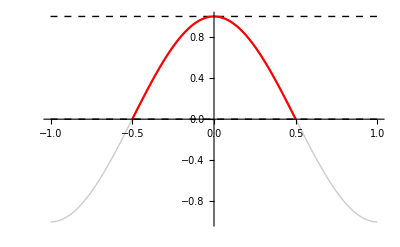

```mathematica
Show[Plot[{Cos[θ π],0,1},{θ,-1,1},PlotStyle->pltStyles[[1;;3]]],
Plot[Cos[π θ],{θ,-1/2,1/2},PlotStyle->Red]]
```

In this section we are going to be developing a cohesive zone model for the the peeling on a thin film from a rigid substrate. Within the cohesive vertical  force act on the detached film. Over a length of Δx  the cohesive forces acting on the film are p Δx (e̲)_2 . The shape of the detached film within the cohesive zone is describe by the function y:[0,ℓ]→[0,δ], where ℓ is called the length of the cohesive zone, and δ is called the “crack opening displacement.” The tension in the film that lies within the cohesive zone is described by the function x∈[0,ℓ]↦t(x). 

Consider a film segment of length Δx   contained within the cohesive zone whose  left end has the x-coordinate x.

The forces due to the cohesive forces is p(x)"e_2" 

The force on the left end of the segment is

-t(x)UnderBar[T̂](x),

where the unit vector UnderBar[T̂](x), as we have previously defined is

OverHat[T̲](x)=1/((1+y'(x)^2)^(1/2))(e̲)_1+(y'(x))/((1+y'(x)^2)^(1/2))(e̲)_2
OverHat[T̲](x)=cos(θ(x))"e_1"+sin(θ(x))"e_2"
□
The derivative of the unit tangent vector is ""(x).

The force on the right end of the segment is -t(x+Δ x)UnderBar[T̂](x+Δ x), which be expanded in powers of Δ x as

"T̂"(x)t(x)+( "T̂"(x)t'(x)+t(x)"T̂"'(x))Δx+o(Δx)

Summing up all the forces on the segment we have

#### -t(x)T(x)+"T̂"(x)t(x)+( "T̂"(x)t'(x)+t(x)"T̂"'(x))Δx+o(Δx) +

```mathematica
FindRoot[x Tan[x]-1==0,{x,0.1}]
```

{x→0.860334}

```mathematica
Module[{θ},
(*θ[x]=ArcTan[y'[x]];*)
θ/:Sin[θ[x]]:=y'[x]/((1+y'[x]^2)^(1/2));
θ/:Cos[θ[x]]=1/((1+y'[x]^2)^(1/2));
eq1=T[x]Sin[θ[x]]-T'[x]Cos[θ[x]];
eq2=T[x]Cos[θ[x]]+T'[x]Sin[θ[x]]+P;
eq3=(P x^2)/2+T[x]x Sin[θ[x]]-y[x]T[x]Cos[θ[x]];
{eq1,eq2,eq3}]
```

```mathematica
""={-T'[x]/(√(1+y'[x]^2))+(T[x] y'[x])/(√(1+y'[x]^2)),P+T[x]/(√(1+y'[x]^2))+(T'[x] y'[x])/(√(1+y'[x]^2)),(P x^2)/2-(T[x] y[x])/(√(1+y'[x]^2))+(x T[x] y'[x])/(√(1+y'[x]^2))}
```

{-((P (1/4 Cot[x-C[1]] (4-2 x^2 Cos[2 x-2 C[1]]-2 x Sin[2 x-2 C[1]])-1/4 Csc[x-C[1]]^2 (4 x-x^2 Sin[2 x-2 C[1]])) Tan[x-C[1]])/(√(1+(1/4 Cot[x-C[1]] (4-2 x^2 Cos[2 x-2 C[1]]-2 x Sin[2 x-2 C[1]])-1/4 Csc[x-C[1]]^2 (4 x-x^2 Sin[2 x-2 C[1]]))^2) √(1+Tan[x-C[1]]^2)))-((P Sec[x-C[1]]^2 Tan[x-C[1]]^2)/((1+Tan[x-C[1]]^2)^(3/2))-(P Sec[x-C[1]]^2)/(√(1+Tan[x-C[1]]^2)))/(√(1+(1/4 Cot[x-C[1]] (4-2 x^2 Cos[2 x-2 C[1]]-2 x Sin[2 x-2 C[1]])-1/4 Csc[x-C[1]]^2 (4 x-x^2 Sin[2 x-2 C[1]]))^2)),P-(P Tan[x-C[1]])/(√(1+(1/4 Cot[x-C[1]] (4-2 x^2 Cos[2 x-2 C[1]]-2 x Sin[2 x-2 C[1]])-1/4 Csc[x-C[1]]^2 (4 x-x^2 Sin[2 x-2 C[1]]))^2) √(1+Tan[x-C[1]]^2))+((1/4 Cot[x-C[1]] (4-2 x^2 Cos[2 x-2 C[1]]-2 x Sin[2 x-2 C[1]])-1/4 Csc[x-C[1]]^2 (4 x-x^2 Sin[2 x-2 C[1]])) ((P Sec[x-C[1]]^2 Tan[x-C[1]]^2)/((1+Tan[x-C[1]]^2)^(3/2))-(P Sec[x-C[1]]^2)/(√(1+Tan[x-C[1]]^2))))/(√(1+(1/4 Cot[x-C[1]] (4-2 x^2 Cos[2 x-2 C[1]]-2 x Sin[2 x-2 C[1]])-1/4 Csc[x-C[1]]^2 (4 x-x^2 Sin[2 x-2 C[1]]))^2)),(P x^2)/2+(P (4 x-x^2 Sin[2 x-2 C[1]]))/(4 √(1+(1/4 Cot[x-C[1]] (4-2 x^2 Cos[2 x-2 C[1]]-2 x Sin[2 x-2 C[1]])-1/4 Csc[x-C[1]]^2 (4 x-x^2 Sin[2 x-2 C[1]]))^2) √(1+Tan[x-C[1]]^2))-(P x (1/4 Cot[x-C[1]] (4-2 x^2 Cos[2 x-2 C[1]]-2 x Sin[2 x-2 C[1]])-1/4 Csc[x-C[1]]^2 (4 x-x^2 Sin[2 x-2 C[1]])) Tan[x-C[1]])/(√(1+(1/4 Cot[x-C[1]] (4-2 x^2 Cos[2 x-2 C[1]]-2 x Sin[2 x-2 C[1]])-1/4 Csc[x-C[1]]^2 (4 x-x^2 Sin[2 x-2 C[1]]))^2) √(1+Tan[x-C[1]]^2))}

```mathematica
DSolve[{eq2==0,eq3==0,T[0]==F,T},{T[x],y[x]},x]
```

DSolve[{P+T[x]/(√(1+y'[x]^2))+(T'[x] y'[x])/(√(1+y'[x]^2))==0,(P x^2)/2-(T[x] y[x])/(√(1+y'[x]^2))+(x T[x] y'[x])/(√(1+y'[x]^2))==0},{T[x],y[x]},x]

```mathematica
DSolve[eq2==0,y[x],x]
```

{{y[x]→C[1]+(T[K[1]] T'[K[1]]-√(-P^4+P^2 T[K[1]]^2+P^2 T'[K[1]]^2))/(P^2-T'[K[1]]^2)K[1]1x},{y[x]→C[1]+(T[K[2]] T'[K[2]]+√(-P^4+P^2 T[K[2]]^2+P^2 T'[K[2]]^2))/(P^2-T'[K[2]]^2)K[2]1x}}

```mathematica
sol=Solve[eq1==0,T'[x]]
```

{{T'[x]→T[x] y'[x]}}

```mathematica
eq2/.sol[[1]]
```

P+T[x]/(√(1+y'[x]^2))+(T[x] y'[x]^2)/(√(1+y'[x]^2))

```mathematica
sol2=Solve[%==0,y'[x]]
```

{{y'[x]→-(√(P^2-T[x]^2))/T[x]},{y'[x]→(√(P^2-T[x]^2))/T[x]}}

```mathematica
eq1/.sol2[[1]]//Simplify
```

(-√(P^2-T[x]^2)-T'[x])/(√(P^2/T[x]^2))

```mathematica
solt=DSolve[{-√(P^2-T[x]^2)-T'[x]==0},T[x],x];
```

```mathematica
Ts[x_]=T[x]/.solt[[1]]
```

-(P Tan[x-C[1]])/(√(1+Tan[x-C[1]]^2))

```mathematica
FullSimplify[eq2//Simplify,Assumptions->0≤ C[1]≤ x≤π/2]
```

P-1/2 P Abs[Csc[x-C[1]]] Abs[Sec[x-C[1]]] Sin[2 x-2 C[1]]

```mathematica
eq3
```

1/4 Cot[x-C[1]] (4 x-x^2 Sin[2 x-2 C[1]])

```mathematica
Ts[0]//Simplify
```

(P Tan[C[1]])/(√(Sec[C[1]]^2))

```mathematica
Solve[eq1==0,y'[x]]
```

{{y'[x]→T'[x]/T[x]}}

```mathematica
Ts'[x]/Ts[x]//Simplify
```

```mathematica
Cot[x-C[1]]
```

```mathematica
(eq3/.T[x]->Ts[x]/.y'[x]->Cot[x-C[1]])
```

(P x^2)/2-(P x)/(√(1+Cot[x-C[1]]^2) √(1+Tan[x-C[1]]^2))+(P Tan[x-C[1]] y[x])/(√(1+Cot[x-C[1]]^2) √(1+Tan[x-C[1]]^2))

```mathematica
Solve[(P x^2)/2-(P x)/(√(1+Cot[x-C[1]]^2) √(1+Tan[x-C[1]]^2))+(P Tan[x-C[1]] y[x])/(√(1+Cot[x-C[1]]^2) √(1+Tan[x-C[1]]^2))==0,y[x]]
```

{{y[x]→1/P Cot[x-C[1]] √(1+Cot[x-C[1]]^2) √(1+Tan[x-C[1]]^2) (-(P x^2)/2+(P x)/(√(1+Cot[x-C[1]]^2) √(1+Tan[x-C[1]]^2)))}}

```mathematica
Solve[(eq3/.T[x]->Ts[x]/.y'[x]->Cot[x-C[1]]),y[x]]
```

Solve::naqs: (P x^2)/2-(P x)/(√(1+Cot[x-1]^2) √(1+Tan[x-1]^2))+(P Tan[x-1] y[x])/(√(1+Cot[x-1]^2) √(1+Tan[x-1]^2)) is not a quantified system of equations and inequalities.

Solve[(P x^2)/2-(P x)/(√(1+Cot[x-C[1]]^2) √(1+Tan[x-C[1]]^2))+(P Tan[x-C[1]] y[x])/(√(1+Cot[x-C[1]]^2) √(1+Tan[x-C[1]]^2)),y[x]]

```mathematica
eq3/.sol2[[1]]
```

(P x^2)/2+(P y[x])/(1+y'[x]^2)-(P x y'[x])/(1+y'[x]^2)

```mathematica
DSolve[{%==0},y[x],x]
```

{{T'[x]→T[x] y'[x]}}

P+T[x]/(√(1+y'[x]^2))+(T[x] y'[x]^2)/(√(1+y'[x]^2))

{{T[x]→-P/(√(1+y'[x]^2))}}

(P x^2)/2+(P y[x])/(1+y'[x]^2)-(P x y'[x])/(1+y'[x]^2)

Solve[{y[x]==1/2 (2 K$23367 x-x^2-K$23367^2 x^2),x==ArcSinh[K$23367]/(√(1+K$23367^2))+C[1]/(√(1+K$23367^2))},{y[x],K$23367}]

```mathematica
Solve[(x^2(1+y'[x]^2))/2+ y[x]-x y'[x]==0,y'[x]]
```

{{y'[x]→(x-√(x^2-x^4-2 x^2 y[x]))/x^2},{y'[x]→(x+√(x^2-x^4-2 x^2 y[x]))/x^2}}

```mathematica
sol=DSolve[{y'[x]==(x+√(x^2-x^4-2 x^2 y[x]))/x^2},y[x],x]
```

Solve[{y[x]==1/2 (2 K$28191 x-x^2-K$28191^2 x^2),x==ArcSinh[K$28191]/(√(1+K$28191^2))+C[1]/(√(1+K$28191^2))},{y[x],K$28191}]

```mathematica
Plot[Evaluate[y/.%],{x,0,1}]
```

ReplaceAll::reps: {} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
y/:y':=Function[{x},Cot[x-C[1]]]
T[x_]=-(P Tan[x-C[1]])/(√(1+Tan[x-C[1]]^2))
y/:y=Function[{x},(4  x-x^2 Sin[2x-2 C[1]])/(4Tan[x-C[1]])]
```

-(P Tan[x-C[1]])/(√(1+Tan[x-C[1]]^2))

Function[{x},(4 x-x^2 Sin[2 x-2 C[1]])/(4 Tan[x-C[1]])]

```mathematica
eq2//FullSimplify
```

P-1/2 P √(Csc[x-C[1]]^2) √(Sec[x-C[1]]^2) Sin[2 (x-C[1])]

```mathematica
y[l]
```

1/4 Cot[l-C[1]] (4 l-l^2 Sin[2 l-2 C[1]])

```mathematica
Series[1/4 Cot[l-C[1]] (4 l-l^2 Sin[2 l-2 C[1]]),{l,0,1}]
```

-Cot[C[1]] l+O[l]^2

```mathematica
T[x]
```

-(P Tan[x-C[1]])/(√(1+Tan[x-C[1]]^2))

```mathematica
"T̂"
```

```mathematica
MaTeX["\\hat{\\boldsymbol{T}}"]
```

```mathematica
""=3
```

3

```mathematica
("")^2
```

9

```mathematica
Manipulate[(Cos[Subscript[θ, t]]-Sin[2 Subscript[θ, t]+Subscript[ψ, p]])Sec[Subscript[θ, t]+Subscript[ψ, p]],{Subscript[θ, t],-π/2,π/2},{ψ,0,π}]
```

Manipulate::vsform: Manipulate argument {θ_t,-π/2,π/2} does not have the correct form for a variable specification.

```mathematica
Manipulate[(Cos[Subscript[θ, t]]-Sin[2 Subscript[θ, t]+Subscript[ψ, p]]) Sec[Subscript[θ, t]+Subscript[ψ, p]],{Subscript[θ, t],-π/2,π/2},{ψ,0,π}]
```

Manipulate::vsform: Manipulate argument {θ_t,-π/2,π/2} does not have the correct form for a variable specification.

Manipulate[(Cos[θ_t]-Sin[2 θ_t+ψ_p]) Sec[θ_t+ψ_p],{θ_t,-π/2,π/2},{ψ,0,π}]

```mathematica
<<Notation`
```

```mathematica
Symbolize[Subscript[x_, y_]]
```

```mathematica
NMinimize[{(Cos[Subscript[θ, t]]-Sin[2 Subscript[θ, t]+Subscript[ψ, p]]) Sec[Subscript[θ, t]+Subscript[ψ, p]],-π/2≤  Subscript[θ, t]≤ π/2 ,0≤ Subscript[ψ, p]≤ π},{Subscript[θ, t],Subscript[ψ, p]}]
```

{-3.,{θ_t→1.5708,ψ_p→3.14159}}

```mathematica
With[{Subscript[θ, t]=0,Subscript[ψ, p]=0},
(Cos[Subscript[θ, t]]-Sin[2 Subscript[θ, t]+Subscript[ψ, p]]) Sec[Subscript[θ, t]+Subscript[ψ, p]]
]
```

With::lvset: Local variable specification {θ_t=0,ψ_p=0} contains θ_t=0, which is an assignment to θ_t; only assignments to symbols are allowed.

With[{θ_t=0,ψ_p=0},(Cos[θ_t]-Sin[2 θ_t+ψ_p]) Sec[θ_t+ψ_p]]

```mathematica
?Subscript[θ, t]
```

Information[θ_t,LongForm→False]

```mathematica
?NMinimize
```

```mathematica
l[a_]=((f[a])^2+(a)^2)^(1/2)
Series[l[Subscript[a, p]]+Δa (1+f'[Subscript[a, p]]^2)^(1/2)(1+ϵ)-l[Subscript[a, p]+Δa],{Δa,0,1}]//Simplify
```

√(a^2+f[a]^2)

(-(a_p+f[a_p] f'[a_p])/(√(a_p^2+f[a_p]^2))+(1+ϵ) √(1+f'[a_p]^2)) Δa+O[Δa]^2

```mathematica
Sin[""]
```

Sin[complexSymbols[]]

```mathematica
D[Sin[""],""]
```

```mathematica
Cos[]
```

```mathematica
?""
```

```mathematica
?complexsymbol5
```

```mathematica
""[θ_]=Sin[θ]
```

Sin[θ]

```mathematica
D[""[θ^2],θ]
```

2 θ Cos[θ^2]

```mathematica
Cos[Subscript[θ, 0]+ArcTan[f'[ā]]]//TrigExpand//Simplify
```

(Cos[θ_0]-Sin[θ_0] f'[ā])/(√(1+f'[ā]^2))

#### hgjgjj x

```mathematica
"(*Cell[GraphicsData["PDF", "\<\
9E14ARda;S<:9LCUl^G[Yo>Pd<C62S@P<21_HVX:?3`P;daUKVMdJ20e830PDR0_
AVU/M6Eb82m6K65dIDAUHfmTIB0n?PYcM79UHFd:N06=TTU_Xd0DQ>oi5JfL9XX2
=4/3DQ`9>h31aP/dMY_;20`HQgfaHoSeHc^9AY[CZ0n_GZVU[iiD=ER36S3G1cT0
1M14H0^:Z`DYo/^ncQNN_Jh2Sl2;925:T4DFk7<`aT2VI<BRnlM_bC4<9@X/@9a0
LE1j`3VPL@l113P6_bi?07l05MnYohM0U2abdQga;CT6D@S:EhA<lAcl1l7nAMa>
h`1^KTTIRV6HJhSmUk[YfmEgnfO1n@>=lDoFelc_X/^a0fgR`mn1gdJ87cdB/_X<
_:1WWbF5E[b=_:lFiNG/behiNWaC56ER5/Mm/7VO>`O[XUU`=nDfdZH:Cn?bO5Rg
UJDAff=fK]2jIY0@glGCZST8nKBgfD]bCYNMf0bng9^We@8?loDV7S?6e4;2HTR5
]C?SeedXMoe^U/8E]ZB=5k72lhiXeBW0SU^X]Hi]KjjK`SAC]4<J[ff3W`b9IBjD
CkE@21V;6AdN>TO2BLe?U?4:fDB=i8_MJDIlS59FYDmiP<AJmdW?KSWn82KdQ4Bi
RDemANIYA/Y@GfjCA4UDj5CMJIlS_JeCK8gc49ZJhkPT]1Yog?Z<?G4K?ZX/=WjO
JFbQ<MeP58j>c_/5MYOI>=L>iWWYXRHRAeXFA=/F8e7<GLlhf_[0^1=YlmijBe9>
/F0K^f>Y9YVJWMZ?^/Gm9_>=^Pn2KYP/MiaJRX/QKXlX]1Ag:/4/bW5BaIFaKXL1
jnLQkT8VXidjlbGAKF0h2oO/YBCKRMeh9VcETVkCY1B<PSRV<NaC9NhM4kGNleV;
6Q;I]HEQTAAIg2]b[9Xcb6KmifSdBWlGiNgYhEY^i]JaFl?o09I@o8T:IFiTLgAb
IF5]2VE^I6mRJPXe830PKf9Z2SHc=@YUKVA_HVX:<R0`86mRJPXl?20_E7U`IB0_
D65WIB0_D65bIFid83<P<21B82mBIG=_MG9SIG<P=R0`858P;d=_KWAUKWAc83@P
<21B82m=IFAYHD9_N21K<20`834c834eG@Xn?PYUKVA_HVX:=R0`86mRJPXl?20_
D79_He=UM21K82m@A4HP;eAUN7@PGB0_AVm^M20l?20_E5@a83PP<21B82mDNC4P
=b0`858P?ShP?Sh:IFiTKf9Z2S<P<21_HVX:?3`P;eAiL6DP;e1QIfEc82m=IFAY
HD9_N21K<20`834c834eGB0_@fmeKW@P<B0_BfUTLb1K838P<21B85dP?Sh:IFiT
Kf9Z2STP<21_HVX:?3`P;eAiL6DP;d=QM65/KfLP;e1QIfEc83<P<21B83hn2VE^
I6mRJPXg830PKf9Z2S`l82mDNG1U82m6Kfid82mCMF9dNG1U82mDNG1U<B0_@V5c
IDI_KW@P;eM2BTA4CB]EDUM3J65^HfEbND`]CFETJDUdHF`P;dI_KWA4IG=SLVU`
M6mb2S4`830PDR0_AFiSKfAYKVLP;deQHe9_KF5^AFiSKfAYKVLP;dIYLW=d@fQQ
LR0e<20_C65cM4=XHG8P<C8`82mGJFAdJ7<PFb0d=30:<20`830P<20`830P<20`
830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`
830P<20`830P<0X`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`
830P<20`830P<20`830P<20`830P<20`830P=38`85dP?Sh:IFiTKf9Z2S4`830P
Kf9Z2S`l82mDNG1U82m6KfidA6EcHg9YL7A_LR0_AVm^M4iQKFDP;eM2BTA4CB]E
DUM3J65^HfEbND`]CFETJDUdHF`P;dI/HFMc83<b2Rm6Kfid@T9_N21K;C4f=20]
<c8a834a<3TP>C@dGB0_BGAQK6US@FiWK6DP;C4d82m1Lf=UKW@P>C4c82m4IG=S
IFid82db>C0:;d=QL4QUJFMXM20h<C4P;e=dIFeF83Lh82mHB6EYIfQd838`=B0_
DgAUKDPP=3PP;deQN5MYI7AX834b=c<P;dI_KWA6JFaU834a830PDPXn?PYUKVA_
HVX:<C4P<21_HVX:?3`P;daUKVMdJ20a<R0`858P;daUKVMdJ34P<C<P<21B82m<
IFiWM6Pb834d830PDR0_C6E^IgAX<b0a=B0`858P;dIYK7AULPX_AVaQM6E4IF=_
I6DP?Sh:LgAbIF5]2WP1kEAi==AmfdnbKlVNYAnbkk//fLV^8Q4bIPJCfLb<OH_/
I8W:D/T^^a0R96_64Y8eje3:;W^lXikk^Mmc_lliccW?NooeWWO>nLgiOZoULegO
JoT8l5YLUm22X9bPnRPTCT96DUX5/;YV[N<:@X:Q61lC2E<X16J80l41XTZ1FT10
1`<5hF0XY2h81eD1[:4@@1L:1VAU0IU;UbiA2`0j:;@?1^KRRP>4RCPRHV;ROdY>
C00WWcldA4l/c0D9218?WU0h2Xf08W54R?oHlCXD2^1LXH0c30h5M<`]K0c=301Q
0c<[`02:Q6:8Sk3`L8;3`80930a5HZ4RP3<:0a059aL0S492H2M?`dXBTm320R00
RhJ2HD@gZ3LHRSiAR@=X:0H1`f:9I`261E``82B>F0<L2X0Q`G0?b4T2A;Tc/IQ4
43@6AKA047E4<0/D5XL5Hf1X742<JZ6[oc]?W2/8Ma8K2b>Z0I@cdA:20W^Le8:8
1CZ18FYa81PB2n2PgT@Q2W220Q0H5Pd7nA1S4l7@6=R_=3b`<:C;WaV80aRX2`P3
PD>aF28<4O^T>WnnllCeSmN3d6Rhcbm_e2n[OnH0`f6QL6M9JQUIHT``SQSK1HJT
USXI5d>T<`Z@TOh]QgRPom1i@S6o2RAl<S<Ra2A041@BkP=0X<kDDVHX7;7PP?1o
eVE9h6m[l]o@h[nU`Gm;NomgcOe[SoiLFN7oM_b?m_V_d?XNL;PI244L028Ll0O?
02K02M5h880C[X61ohLG2063no`[_kmJFT=oTlm_^;mZOj=[8Ef8124Q8bm9W=fC
VHAQmF7ND8P530Mf1Ia1L28Ko99K8B5@31b6Q19gmaLe49eTon7cCifU:`c/QRB^
6:3`F`E5@_hblbO;lR]i:A?[jeXg[hSmJh[m5M>2^>ThBald5?Q786]C595FoW4i
@M;FAWT3OQ8bLW:0Q>`UJN86:RT3UfCT0_i5e5m0<[mOLn9[2/9QH=k0;FU9JFTI
P?SoaoOWcOh_<7Y8<0Yb`PcGLB0TQ4PWoaBLi0_f`628E?F;6XP?on?nRh:QD6lX
V7Yd60EF3KfCTYj::fO;J<O[gVYYUR5]3d?WEe[VI=d]ACD5YDA>GbYb?2`;TjcZ
ECVZloVhQ?hiKbA:j6aVQ@/e?H:^I785l8^lcF:L5:aG4R>4B3WTdjEn/hkeFadb
VCYSZbQmPc23_g[=8Nn@W;^gGPi3^KXSLYOO<n/^llE]=7dPn?7;N9J6/eFWcYEW
;gdCC?Zb/bgDf]GAg]JdC_IfWU?/FCbEP2Z8;O3Q4Vlbc/LA/eD9?R;KmiA>XMC/
Ki9WlQc4^;AXcW[US<BTVENO^ce/QMiSe;e/U7?Q]JMOgk8_CDCk=ATVRXkUO9<O
`jFRaofL0a82j:HGeeY9NY8N;Bim]ANCQiR=IINODe^A^FGAnZ@0ef7DM:kkmV5h
<bFQAXoiNjelTXkUFNAFGH:g/FRl]M2A/?R<I=Ah`<fK`=^H>eGV@1o6XJ@nLO_0
k?iQ^A6fYV?WSH=ZI=0acTfhnKAKBA:=7m=[Y?kgiUkICC/E3giA@V3acohZ8l]L
SiYH89FfIZ8R^m;[?A^@lCbSAMh8aCQ8[S3VCeDeW[R>F<KcQ;/OPCdJQYkA1oAO
S:A^_OOIOEVhH[MfnWgQV^f=Q;eW:WfO7dPfXGdjM_XW@HJZE8ZOWVKY^<MgFJ`h
?n0F]@ME[;35a9J>ARR/]=QL>@[eoFCNmlPcK]5n;Zi8l=5[15jnLEbRmnVY3f]N
:I=6WBW]j0E>GZ1DPd/fnkBJmd;]3HCaa84F58oSJ0Ifc<SA]P9ROQ`o4gO3SmUN
F]34Q`AGe^@_dDTTg3/5gn5Z6H_UPG<KIY2gH<P:;IcZUl`IlnT3LPeH=5LB/VC_
jL?7eoWTaTPCY]?kk]8cBaAA:1HFd?j@GQf=N2TVo`FEA7gI<e4[V5I:2>BQ<Ld^
=[8o_IE<N<I1bR8Md3In4A9m@CCRRBQZdkMXUlX?5__/ji>/<LTcdZOfA[`ULB:>
hX_7Wk5QUjg^MQ^ccj`]OB^3N2G^KHB:GVM3G;BCl?gJ6gZ_PRD[WnZML0_d1[aL
ckoN^j8c]8c?kf`dKIV=29_Q/CSk`OUVKl8jJhP=TiL=[?3cTPSj<5dS<Kh;U<Jd
bEY9VS]RR@lG463KdGUfm:ja]E0Ro>fg=ncZo2YS/Y5a5=YeS[ZI?M_P8[WS]IOl
WF6?X4lfX`Mc13K_Xn5i19E:aVkDIM_MEQ?K@;Eeci6<3]gb91e</k]oVPTM0f09
81iBaO5OWNJd_iP^HNB7Hk[7@:7ig?^=`1^n?M=YhH;`2`d4b<A^^V;^NS__nRM?
Zc?cHo3VkRVF8le2KFT[co?>gmFE8a0kPKMOY:Y8deh:e_2>Hi?ORD[jIW?C<ZiM
G:Ya_>JZbeAmh9[Jk0og^Lf^MUI1F]ZFcM?jgNUSkSdf][7CGmGeVX8LDajZTIAl
XBU`]h]mW[10ZoWddN6n_];::J]_8I7h>QfQ<_485Nfg:/MHDGaj[NY6^6A0][SB
]W2j>>bN>3W3Q>HSY^TgfA[h_U5U`YhCYeJFOngAUn>gFHMG_PgL59KK60Y@cODU
IjQ[YfQkf?m@fO^nj/65]mGKJDFcNi3^W>IUBmH/Q[?R8Jo_H3m<OGmDFaE[=MaO
ee<2HhSbc7>oKo7<kX=W:7XTDi7ZUA/WKk?coJGhHm7^AaM;Jd9<Ke5o5AkSdLA^
J38DZR:;cKj?LdK_Zle:aE0D]<I?VS99>iTm`X1WiAO_bSk>`_YOnQK07:oWkF?U
O3G7RR80DRenNj_f]<GP^O6Y^jlF>hXLh]R^YToUdQN^6=9jmSSNXG5^X;/L:O/j
Cf5I`lWOGcn1U^_WQEkoYKVbY90@8n?DLn5fZ>:1EeH>4M:BTaPCGPlj;?Aa7TWT
FIe/YZcX]7;IY_F]5bKUHRiMZg=IBKBjaUh?LUbZS7Vk=XLS9BlW?;dkkBUnlg_[
[<ikkd>oN:Nj>nXIo^[/OAVm7]L/gEYgK_Y[mF]4Qk3O_V:RENh:>_bY9YK9SK[L
V1456KaIj?VITO@DgRlZoTe<fFT;a]@Dm5X9AoDgcZNFmH/fJWZe?cX3Eo_QfO?m
`gRa11?U[K=gYWW4ej<T1NQC]YA?:ljLg`ZMoNWbM_G7K]lkQRlTUlBVWlB_U;:C
[QB]79a_4=/SOk8YHcOFNDFN?;>HNhLTlS76/9>V=9WU@6ZRdfAg_?61:Eg1b1;O
SCi:8EZdJn:bA;B]MV@JScBVcSRcA2DedXe2=o_J@K>HI[ACfmKbS=l^4^<:BK59
OGDU:i6ilIF?fBhk>H<96NGC[_fdB^<gXbVGkGFiMhbS267<AoN_WZ;]3C6Ligj;
b=7`6N[/QLMVa;X52PC;RJl?noaXR9ATFI9P0aZ^gMBnM:7MRDdD;HY:77mEVca_
VcmkDj3P=IGGA0bid2NIU;03dNWIfJj3W_WZ[1cY<kgRSee_L:h3W>71JViABjbU
G8_65b`4A]l4O2]1[F3UWBKPDcGm7kRn:U7Xj1DWPMgLAbM[2BX<:D`2mafl_3OU
F`TU^Te1e@e]Z6SAe;88NQ[`Agn^@[^O2FN/KEn/5bEbL3jB08_?3?5=g488RRa7
9o7Ml[E@i<JYYoGI1FC`3LTUHb:nDD]c9cZ73ckjCVOfI8Wb/I3UC7o2G6CjSJKW
S`ARn?b5A0oMQE_@=H=aEo7B6SM1n36TL=_FQ^U[5Bm14Ql3n[S@2:l2_Ngi7b6e
3bRi>[SLBY2a_Q9goO]QPRBG]ODAZ_B^RZn]3/N4aPQj9TcjY]_7m_g3PYf0=QZo
276Ibmcmn?[WCoERFmRi>U:[X^;g]MA7LkiJHP;f7kDG0afDfNBiXW6]cLJ;MV]d
Qje<eFNle==?fn][gJ`<:ifRdeaUV3Bk5?<:7oM9X64?>CZH7=P>6eelOc3eOUZU
jJ=M]nPFaGKQ`>LHW4=fgaWVZ5>jkTlGoCElZRD_2Q_7UbMckW0C2YZ=FZQNaDR]
A20k7_8jlK?G`aagK/J17aabeE3@gL^<YWjIL2/5cTR?fBRfSm8?KV]>Z=AP]fmo
lEiblj<ZNn6KcXH]A4<5Yc[M_^?@n/mN]d_:oXfFKL2FhMX6Da3ISh/iMaiKSnXX
k1EVJ;nEXheDbFI=EfH:>PdEm^Q]2_:JM?HJ0J[ejKF:HMWJkN1f:Zf02]<]BU5;
K8D5oKADNWX4SSm`?BY=eVeYMgVaac:YNFj1T9n:<79F]32m9Ln=Te]N2kABBW0n
S3E?SPZ_f:GonI06]l2L]jc0USG:QJn_mM1hD3WMTc/0iJlelW3Y2E^me4nm]QVD
mIR[<U9K3hZH3^AeegojJE^Vmbh[X`PIhHSeb49D=bRn2WZo?Xf?[FnmMLkZ6Xd_
UA>1:Z[^/_P62[7VW]Z/VZ^?bUim4n@eHckELJMOfmCAjf<[BnWAelSl6kTYck5e
=3g;NAb94/S[UAIPGbhgSe0JCShdCfNLdkFEDfLKj2P>B/?4jCEc;1?>EUg>K:1V
:D;A<[Te3Tl3kbfnmiTe;RB>S1AW_V8H`VG7?W0PRlS4[k39<m/KEbU?C>K_LMMc
gNllM9^3UjS]g3Nbd/aPIN@YSSVPBdK:4icD@H8:`e?;QJ<Z59YWfi`@X`IT8Eo4
>Md^]/gMh9cJCEAD_RUDTd8[=EeLdE<aZ_7i2nlNQ/TIOCcA[M9U]igNYkmV6V`b
DMPY?HT@hkm>lRBfHEDYAIaC`T1Y_;<kcS:2GhZWJQ7i=^FZ:`BY_N]om]Q_lV:=
MI;>V8>E`INk_?GhQ8[YEdL[?>Y[<>ahLn`5S?1CZM?_V:HBO7jZG3MgAPcN[X@o
7a4d:i@fYV2PK6B^`OW6BVUm:S2H2F?deOb2Sc9U2jYO7`_PIkc`I=XR1l4faYbS
BKDNbJDMY?/STVYcX/OlB70P]naPa3lS=>KV`X^k?Zm7WPP4ARRg]l/:f3VmQ3`h
MFSWMDZMkegV5k682G5aQn0;MdSC];O_noEX5?QKebQWVJ4R=j^ZVDA`kBB_mTD<
^=mMHCh<cYc9IK6ah2cJ6nc_oXW:2lc3Om:lIWoe4a?NIK:GjGW^5XO89g]E7WN^
^H:RD;d9?iHREX/=PYLI]OUg?K[L`_E23ccV:RZBPjoMfn>fDgHEi;Td6M?h5HEK
j^cXcn4T`nf6E94bing@hhheXHNTlHS2E_FT]CMR4Co^77BU53A]FHd?kGJ<L/ka
3=>X>Dmn`gjag<o?37k19?J8Sj6UCQGR=XnSSgc8nXSRXgoD@kM[Mib=QK=NK1E4
Kg=N;l_eIJkI60YfX91kW9ja^2j[]SMRCbKAJF]1BNhj^WfUV82BJKCBnoYRMkY<
M:O3]2I=C2lW@8]S45aND=[4JjDeUn>mUWBi@VAYGSMd>_C=i`3QQa5VW=Gd@l<3
f=AZeTY<_hE`R?9nUnOnhHE_2aSN<b?b@daOl=niSK<dcVV7TmHbYLMmif^LoI:I
cd_8^]m][mK^^?:c^?m^6GVl;mMWMYUK`lW]==`Mg?U76@7D6IfNhHMlWN^<?a3G
Bm[e31[_a=dHekWdk0j<_B0RceQb9HFLgZ1i4l>/<35Pj_9i/:gTQn@b8G1cZD]g
e8]M>1@1UIadYh74M_0cUGjVoAYYb9FGV04ZWjh0B2`d<mbi:QmoSkDDJ;n0C>Tk
ag53]F@3Wd]O3k/`U`NFgkeME^gY4CHC2W>khBVF52olF6J1iMKR<hiESJEkaT9/
bEg9fG/Q?6KY2OcU/OiO1[U5kS6PhflDb?[Ek=^m9L0<=kT]_3j>_>_M8U7l[?]Q
T^[6FdGaO1LD?JWoLLTE_83=eFWkJM[974nE/PdH[f3EoXARaQS?eNK>>P>fJa`C
8XJ@SbC_Lf/QfSF:C?KY0cS>ScT<iC@_VYW7N7D?iVdF1cmF/Ig5UKll?a<cUiBR
VjXEOCcK7j]HZMCn`86fn/dS]I[4fMQZHbFXPn4glkbcGTl9Z39j93HVZ3PVWMhi
4f28jGE^L6^>_CmI[EG]cYE<TC9Z;iDZeIkYj]D3aG2i5EO_[6I:[hbgl_HEVibk
m9@_Y75/iPYT?]JjOeO^LgTO0<5/_SKfc@L5R/Mi?g7R7:AhIN1;9VNnBFO2efQA
Z=/:FoXlMhBlVZ6nTb?a?ZBR[2N3JTRhd2N4RECG?iUDH;JEU:7;/LAJcKY:8YOG
D`nloBc0C93<TjmeOESSo2WMj^``YJF7nSa;imDj6Y9QbX]1W0_UPEbg:R3IRVc@
:PFhVGPLLTBWff0Q5=TLkKUT1b@]16?@EoVe@cQRPV2[KH8oWQJm@7LWegHGKij?
Na=MDHo_mea@CXo7^Alj`b^BndaIQD@njKkIWNj/`C/^3f`4?VCK7]nV6kjB3jVK
H=]RZJ0;P<]H;WF]<5nL^3dj=DFfHbo1nh53PY6>D_W<LQ7=^=VUm[K6^2TDVhGF
14URe6WB^``_nPJAEOkcVEoM6O4m2Cbm>ekHT1X<i:_<PcUOR[cg@FRl;`4BVM6V
54@3;oKH6W5kS6hCFfNYVOaY5LQR4V0XloXX;E7aGN6dNcTmn/5c/aMDbH?lj[Z1
lA7Go1DfNkjJ9YGJZ70>`4icVadVJ2O;kTMFlMUblO<l76K[ZRc7B8=jL=mMHa9]
GkVVW_V8dgnL_ELIXY5Gm6XLK>W<Y4VZU[aH9h^dEM@E1fKdD]JJ/UneT7262XDb
WQEjHAK9l:fV;LeP5/8Z_^FDLEI<eIoW1BX76:W<N[[1Ek;<`^elDNWn4edS3_G[
SQlo3ZAkLFB_cFMjPIBLSBZ2n^_SCkdkNbH_F]m:9CZ/M]?Xb3Cc^d[;d>GDDB>C
]oabm>Ki2mHfEm9RcenSEl0[Za5jU4K6/QTAHX5j]?5n[4;g2Bh7BUmfJ5HFRa@V
_XT;fd2g9SI2He=/INLcgXLeLRdjTM@4FCh^2QIKNUIe>ofiQ5BNKi]jB`eE^13m
iMg<jbh7Zhgk9I@U`i0h1F<b@VPG^T0VDUTMZaid?;]0ZB0[9Y66Xk;1`cZ0a@MQ
GJm?Qdnia7Xo^dUf6Sbnjj];8d3ObGbgjRgEW<HnQmZ2H<OHV@VXhP@Cak/7VFkh
D/oL0G7`5A_7fG=6Y>nE5XM<20=?Gdo:CXjZmFa;T[WdGM/=;Km3:6><^b_D<S?c
S]I]jG9XH4`hcc3>P73Z^l:09b?Ragg>EXVaGEgoj_?H<kEbca16DX6E<;DNV<Bd
NJW>l1/4OE3RO5FYSc9KYT>JU/c;RB`Ed/PG1[bIPlDZAKh6<YD</=3ge[3B@R>9
O2LaQXSDCldf7lKao3<oPd>OW:7]<heU63B0C:me<k>H5eLEW:5TlQheiWbWI3JG
FgU_EbchnHLYO_iA4PNKNjnmQ3]/ma>22jcFiJ4G^U<6_O_NSKKHggQG/fJ[dWFQ
HI:3gCE/VOcFFSg^MVjfTMMS2ZkaEPK1kNNc]HjXfFUZIFkALo5KF/ELUHPT?Ih]
97Ub4gLR:]VS6e@MjeWoc?=`Ak4`J]GG=]3;FXmLOAofN[FK;6MBh5iWX:]0kD9=
RDg:0</]Da=HHafOIf8^SDg8g2RiRCRbAU<0]`b/S5nWKIKFCZeegSlOnlaRIWYo
b:>AKB?_YA]UKW>oQeec^Z_:Sf4cOTA[3N]RGDAjReVSHTa@=V5eG^BfkfgNSTlE
ZQSHUA[[A@M:K[DX6K<1fi05Q>7]hb7jNo;=IhdL`EIQ?>KijfG>W=N3YJCocHoj
gnRUomoPMhGnSm@138N2<3PD0XAaXoh_7AQ7cPYUKVAcM79UHFd:IFiTKf9Z2S4b
830PKf9Z2SDh<S<:IFiTKf9Z2S4c830PKf9Z2S4f<cD:IFiTKf9Z2S4d830PKf9Z
2S@i=C4:IFiTKf9Z2S4e830PKf9Z2SDd<0YUKVA_HVX:>20`86mRJPXl?20_E7U`
IB0_AVm^M20_DgERM7U`IB0_E79eIEAiL6DP;d9QLfE6Kfid82m2EEM@Ddh[@fme
LVUULR0_AVm^M4AULf=bJG1dKg8:<CHP<21B82m5KV=_I6U^Ib0_CF5SDVm]HFi5
KV=_I6U^Ib0_AVUbLgA3J65b83<b82m<HG=d@fQQLR0a<S8P;eMYI7AXLb1K83H`
<0X`83H`<20`830P<20`830P<20`830P=S0`830P<20`83H`<20f<30P=S0`83H`
<20f<30P=S0`83H`<20f<30P=S0`83H`<20f<30:<20`83H`<20f<30P=S0`830P
<20f<30P=S0`83H`<20f<30P=S0`83H`<20f<30P=S0`83H`<20f<30P=S0`83H`
<20f<30P=S0`2SH`<20f<30P=S0`83H`<20f<30P=S0`83H`<20f<30P=S0`83H`
<20f<30P=S0`830P<20`830P=S0`830P=S0`83H`<20f<30:=S0`83H`<20f<30P
=S0`83H`<20f<30P=S0`83H`<20f<30P=S0`83H`<20f<30P=S0`83H`<20f<30P
=S0`83H`<20f<30P=S0`2SH`<20f<30P=S0`83H`<21M83hn2VE^I6mRJPXa=R0`
86mRJPXl?20_E7U`IB0_AVm^M4AULf=bJG1dKg8P;dI_KWA>HFeU82m2EEM@Ddh[
@fmeLVUULR0_AVaQIg<P<c8P;dI_KWA2@Vmh85/]=SDe82dd<3TP<C0f<b0a<3T`
G@X_BGAQK6US@FiWK6DP<20_@G=SIFid83Le=20_A6EcHfE^M20]<S@f82m3HG18
IFUWJ7@P=CPg82mCM6E]ER0g=R0_F4QUJFMXM0Xd=CLP;e=dIFe883L`82m=HGQG
JFAdJ20h<S<P;dI_KWA6JFaU<R0a=b0`858P?Sh:IFiTKf9Z2S4g830PKf9Z2S`l
82m<IFiWM6PP<CPP<21B82m<IFiWM6Pa83<`>3Tf82m6JFadIG8P;dI/HGAUA6ES
KfAU83hn2W=dLVEQK@Yh0JfM1g`LmKG_iknkjUeJeMEZNemYYEEg4BibalH1HVCC
K8X;7HaK2<4><MPV3R@TH0Q`2@5SN0TH9mOH<PV@Q7I_2>KUaN0l26T@h19OGPZQ
B>?g?C>c^k:DnfhnhMVOWnHo/j_oc9anc_o<j>Z[eUfXUFVK=K^fN=V::eIZa[ne
GTg;^nGlBeMLHNhkkVGk/o?GGleanJONidO;bR]FGF[/J[I:SZeMMLTVjoOc>Gc9
h]DG[[S0o5`KHM^cVP?V_^YR6eamjMDKcGgkUoSmiT/^?moj?4o>Nl^U:cIJimMN
HmmkfHY;;cBo_eHfgR/^Gg^e^GoEH[Ik[kSZ@^_kJXSmfcC5ccWZZeZAmST]cmSC
]69=/fWf:?N[S2=lIj?7O/Ni5E?nZQX;SNVn_LGLo^;Rbhimo>>AhL8]QHoc@Khe
0iO:CZ7>Uo9_noS77onXL4_f4n?giJ`7=2fQ3G?L[]TBJUQcV8<W6Bc@9VTYcJoE
lKg2a9=LfKWJO6fZU/`NbMNVWo0MkDTVF/bGa_jJKL:_fKFi9okJ/5K0n@XBG8ag
e[E[6PHiHecKZFg@k]I^inLSk?_d:cG=OYOFi;Q?lfTJGdd^>:3U;aijC:V_;3fP
SVlmX0fj3g;gmW??JCfPZJCG>f_=h5jeW1eKTP=a7b=kdS]k[cddnmBQ`5;_3^n>
NAO/l<kf[Uia`Ei7b=Sb`HDkUZJlNkGCQ]K`lo@QgmiYBegIhHE;UdiR7XO<`jo`
mAe;VN4RJ`JfaZ7D:5o:Bbk`k[F75`mmIVS_iT7GgVV3BednWgOFgZLF3nemJ]3U
FkZDKnEW[i@[U[/g[kV0Jlj?lgVQ>L]Y@g^W^OIZBgO/T3U?6`[hmVkN/L>ePo^`
mPmXChdkX;Ca1jII1j04Ld29F@ODi/E<aRKPLlV1P2oPhcZG3W;^X^B2dhIVLJFn
YJfJhdE]9F2[Q]RN1oh0GVCO`OHn/1o/0ml17=MN/_02fd4P_co3lN9aWNgYH16@
NCRVW@GT>k;o@g0YV0_j@BW`POU0cRgKbN1V8;lg5I@36eP2CPILbo5SK6l4<^mb
8;l[eo04f0X^0;_1>f0e6;J^CLK;P5bGG:=LRmbGo;iLDhc__LOfE23Gma`BJ^ZY
YYDRPdnakmG>i9RXlOQoM^^00ig:AoH;dOaR[HCO;=?:SLlZ]4Z]bQQEJcFJDj]5
inZe1ZeAJm9LF[?VeUXd3fO`XIl1;JR5];0FdJ9J3;e9I4nGI=BZ]J6>kEZ7U]Hj
]Bj]Fn_AN[Dn[AlEW:a=@Il7]9>dJFSb36fV=ZS=dVIK_cn9KfcF3V/OZXM]=]/C
mZlk^Qc_i_dXge_@G72/<5Uh@N5mAKLEGe5bFNWYIJNFNb_VETjYg5=eN_EIeKn^
6GIn/OJ/F[fn[J6dlD]=ODdS[Ulf7fTYm>AkSWSNmKk[Nloofl2c`B^27hCdl978
H>BWdIo6V^?YA7?RCdVmcMUfBk^]oOj>UNTIWJMfGMfm_2L:5EOZ]cUFi]f?PBX@
^eFH@/50HBFfh32@oLZ3O9cg5oHH@Ei6MSh_NTdka:i``Y4ha=H6gAf9mXjJ:UmE
b5OUFnW@A]KJGB=_j[LEU7ohYj_bHd84VaZbGfYOUkL<GPBPnc2L`PR9WF;BJThZ
9fljg=jQo>68_K^[Ik9:ekVE_E`5O1>>f4/KjabNn[XEMODNAefSOV=S_MeCEknl
_Zj5GO^USF5eIFUS@d=SZGic^?74?I6^li3LRa`g`_NC3R4`3Zf2Fn3N^0Bio`Zf
3HLaS<d@XSAeb917k2YO:N2SB[jRf=K;eO[BMKG>o82_RQonL7LE5l_5MoZZn<57
][gZHWm[<Z1o8nY_JME_3kBfNmFJ^<lO]Cf=/H[Zfh=9SVb8NU_Je?YP<QVDjo_3
lI/MS[aMb6/9Ee76EMQCkAeid<:H_EL=:9WLVEnP]]I5G<gao3cK5HeQEd/l;lnE
3/KLQKFUNM>k@]7V@VLA77[an1]`/9cIjUDamlJ4AJ21VjSPIRYB`^_l_db_Aj;]
B:eMF`9FP_GP1W0Kf0gfPfO14E1bm_@lkDd6O`DffGTGHWh<f:U7;HZdNF0YF0<f
PNgP3_0@>0QN04M1bMU2oH<XIcibe_RJ>:EI@d9led5d^F1PjB6]fS01`XAB_XU[
U^_]IC07W05FP@gPAW0kN10l3Yh3[`3SN]mRl06`WBfRIZ]eEWNVZk^kK7Jo[JYB
aUFE=]_:]I/g[kejlnJ[WgSmmBNNn=F_7=OYkgohTOjOZ^ZS3eGU9l_EnJYKMJWc
mK_d5oWoCGRV78ScagV5f96i``Qi/b7LcE0h7`[W@ndZ[]Z[>Ok2_AFc:e`ek[51
k[51k_4P_jNhO`nohAGQbS8lI3:lb^BjJ8BQ8EEZ@eUIWRORmjYHBFe9CMfmBm^S
dM67Xm7fYK/M7CIK`=d@;5Y/]`MJ?WWF7@gb;nZf_hcV:Ndn[_Mgb4BWm^XQ[R/O
/nU863`/QXO56AhF`l=RN5P<3h_QHC4l;8J7aO2`61hF`l=RN8SAQHMNkSO9eBNi
>AVW6:N/LGNFZi[L/FIbeLfUU1VZ9GHVY=T]Ra=SI?0g1WmSl3L6Of?`=`IoHo0g
1WmSl3L6Of?`=iKQK`cnaPcn6V@jBOGdJ]eMhH0o_h3oUPII2ZCb:i@_Xdbe1M1K
5GMg?^EfmjYUWe]ad]Y0OUVX;MQBGS?]1nO_OT?ocQU]ejPG716O;f`[];Ld95ZW
Ojni^D_=o/K5Fk^BQCDcT`=1Glg0_2=goD@om9VfmHWFI=QNHEoX2G2kg>SnhfoH
?hCVB=h`[Z@A6H7RaHH_J]A/EdigXCF=D;`ARSM2lDHXgPS56j5h8aA_Q>:=D;`A
RSMZkh2?@=WI`dcOZ:FZZ_^7dA=cQ5U=6Ob/QYoE6GiF<g/e/eLcNcFcEc=k=K=G
<g/e/eLcNcFcEd=>db[0@D=bAC?50gAVnIP_O<C[RWHV^Kf0`LMl_UfAhEh5g:^0
NaE`[`;^EL2m2[QG0OLZh5h5g:^0NaDIkUG0_@YC>e^DF5KCWZK[>]<mL372onj^
gYkN0FGb=?/igkGKeVgil9UMOdahZWiaeXI_[5[VBYinZ[MfdO;eIiknF5ecj=OK
kW[YO=]Nkd>ONoB=MK=K8R^gGK;dVZXlNmkdbLEfAnWZnNM^G1edCMgdPae[]T5@
VkH?7CVFElZXCk_]48hoWomRPCZhAa`P52V18PXY5cMFc;J3[MOH?`Q=Q6IAmZ;X
@99?^/F[R?U]0^9M30]P5c[RRhF>W14c;NN`LhhR`ak8g3iVTG>9AXVOjV2K5Q]A
EJ@/Jm2=_4mE@Qc3?mCGNA@Ta6HHW/R9Z9N[Q:ZeK8Q]F=nZ:][mPLSENV]S/c_?
[WJGEeOTEcPL:l^[>^/J:Yc==W]QPL]mNV0JETFmJ=/m^Tc_m<B2_SgNUUWAI66N
kJN=iCJU:Vf^^]72@4]MDDEQ;=Rdaa<>h/H@R>oPMfb>HdABkao@4]a^;DQ`mBeL
O@]NAfQXb6P]<UZKTM5JI;@F6Je5AV^AdEYT]1HI[DE6Ji7AFVBd5QV]=Fa>;GB2
;e2jQIU=OhK5IIc<BVZAD;S8Y7002/NPl26f2/?[B8Sf=6Qf]<Od@WPJdoID8kgE
B6ledU^=m5HS_ME8KcGBFhgdER>meDR_:0^glAJ33h3QFbb[h/P:Z2W0V24i8^51
9WA@FfMLdOWX>k[n`YkOaI];OW7V3@oN/g7IMj]K6V>Mj^?fmWBK?]UNgU3oinlo
nN6Idi]R2kmegNLOF9JLY?kTLdLR8C>n4Qm_7c5lO53e7M12D5ZlCPPj=43]1X?J
UXoGS<Qd2KL]fO]jL0>h3N`6nl6ch0R`O;b6SdLQC1nO3jo4PAXn?QmNiL>[O7RE
3jobhEDn_<Z7EoW`:QmNiL<[LKo3^?86CC?X;5JRf^2JL<[55KZhfV[6hBcGJXE[
]BKGG?0:k`WG:QPA/j4Q`WUhJ?;:3Zo/l<X>[nc`bPj_k?3:3Zo/l<X>[nc`bXYK
gV;`0K0IEeFTEG1EJ9?C/S>`:I;a2`493CB3Fn91K>[V;jiLO/ee5jbh[ZkWBh_^
NOg8PlolDIfS?2/6eRm:gO><fW[==knfoW>k_[I[m^aSSnaoEoF[?7Fj^[/i</fV
RU[dhe2BFgSYn37kNnR6Gc_UT7Q0PSfiYaXXD0LejU:I62QW7BacTBMTbL^@a@iA
iAMM4:<B/m_N4D;=KHI=j5FnC0QaT]P4k/6]R1Y]j`[;Jj[V>>_]M[EMMmR30Km?
ZF;21=/gg:kR4VM3NFEiHDFa8i5Zm@N;Rag;VU/JGOkBR4n^gLje_f7GcGQBBjU;
3VS]`S_@c]FgL_F]B1_9Vg2VQl5//0B/1>_13N0f/1_/1ln28l2B]U:T3J=;?27A
^?HY_IPYEOW<9?Y@3ITRG=T`T]RZA@aIK>FZ<a8HHBbfeYLJ9QW<O4>>MVCU<Rh<
R9/<J86E]N?T<_koBBhKT7>ABkVB_bNQ=F>T]JH=QfPInX8aWU>]gG[IiE^gGG;a
]^;[Ejjjo_YEZkkXFg7N[kkkl6nGGgSQ9KokegomkBEZj:8_KKiXmIK[e;7c_g3M
1L^__EKOe7k[NMmlk_UK;_ijNnaO;WkPl?mlL>Foh0EO/>:G1RfXZ:V8SFTd^M>8
CB22<Fg2?ak1B8`QLV;6;jD6=lARVM`jB89VbI076O8P@aiTb8<<NI0Q3c;T@HHl
b9076O8P@ij<37V@8HlQ@n8ABYTcIeLZQ7lE9_o`/<CZHUOlS>b<i5[/V]nhUPXh
jLaH62LFaXV5LF9QW5PH9aK6RHEaHV6LF1PW5/J9QG6Jeo0FP`n0h@dbJVPT69XA
V>:WNjY[S<2deV2TOGk?5c4W_mSmToOeKnVo?7_ZQU?JkWTVkoZE:cInhO`EVfeW
cA[lhgOgohOnS3jR?jB_JPi?/m^:g=A:G_^l69`kKSG/bZ2fdk74L@ieSEX/B3d/
:T2DRKJeNVjY_J=8PP8S[XZXC30e9Yn<f5i?QP>NL[mWi4e7oUW;2QefUb]LkPV4
TkI=nR>e/JJFH765FZ_/lG@jj[2YBl]:o6iGc2WadTZeeK7B_QYciZ;6T/^KCJ<]
JT:M8>?f30]eh]i^niHFWjmUi3Z?cnLI<kHeAP;1<555F9dBIQ@:1D=R@fM`[jMW
kkF0Njdgk[EN:k3^=J<EmJZ^WX@Injfb>H3mb]5@FcS@DQ5Z][/LQL^6RQgLLeM3
Bb3LI]^T5W6_KWm9VGj[cA5=Ml@L=WfW[CkHdQB[iEj?jl@^[e11]FW]RTbePi=;
D2OaGbH32[e6@=nSQI3M4;8K@WI3b6h8f@dQ^b5T=hC/QY3M4;8K8X088C8Q0_[Y
NESh42`<TAH8ni9JR5_RL35e:oU_I@]=n=lVo6lCo[L9om^4ofg2ocKQOi_`_dgh
gbKlKa?I@Q?I@Q>CLjELILe[DZa^dVZHMiSKB5XS^gF^H@YSVDmmeS5RcZ`E;1H]
:]K:1YIJOZU>3]B9FUT7XW8PJ^ZIU?@l201A/VDMlG6<l>I4KVidE692/Kan855^
^e5N/BO<l5IlEkeEmLSV_a5O`KR<F>eBMkablmNVMRBF:gM_Y5;MF=DC3GOYkinL
B4doNhG^F;9RAW]RW_kA]7QlBXe=/eGk8S6?>c:BJV7[RHDmahii`S::]41e3<7Y
l7T]O2hT>Dn[P4CX3^PR5R=<E2>i:eaiUl77`;:0IG2U3:jD`IDb^586El[PBQUL
:H<[IG2U3:jD6E6APfdH;U0;=jfYPkVX/IWFe<5L3^Ib<9N3^Ac<iF0^1g<iV<_1
G0kVLS0GQ:lTQSdlC8BKWA<ZViU8EiIgO^6<O`c_Z^E0]LTZLWn/QK1:W2Ej1X?l
S2Z=TIbP4OHdPD[6hSRKSA<FJ<F6eXG<B3NQ^S>36/?PDM:[/Z9Qd`JHO/[8^[oj
ZbO^_?GPfbmoIO_W[ok`1GeJ890lcNMKV0cjeLooejl6IejbI]VY7A/_fgW^IINO
LlfbLiJNnlTaXiJaeA<;Q1jhniCehLRG;cWc]_KVA[4;RhkocW6ZhfTdLnDQ93:O
@RiLTURT3Uf/@aO[d<DjM;4>GJa35n_@aCYd/@iM[4<Gjc9nY0hoDPL[aTES>JU_
4lZeSB5UC^[=O;Wd=NBS23OG:46=i?Qm3>J28K0JK0CK`2j`1a`0ch=G`M_P@b0i
OQ7RJ?[8=]QA8ghY3kF^@Je[C6WYHc0G387EH2?H1WJ1?N00N1jl2TAJX/a35L:<
X1_aKhgh]dKlFb?n[A7oeXQoJlBo=N;O6_5_SORgAY<fKc7h08c=M^ZjaK>@Y;MA
ZSB;Ji:ZFlE:LH:D`CAfkOLE1ofQ5XLg=/=Ih:RiILESAhk^VkAaT^/LYbNAVWKj
`nOlCOnQV_fg6M/MFeae`Kkc7RY9nLiY[UQ`[SkjbeoZXciOnLaHBd]_];M;WJdZ
EIVj`8^X8[WW7Ama[4=OBkFTVRoJVXmLRkH66DWfKVS[?ig3R8J9UI?LGk8E4OlP
fkJ/K[F8@;B<4@R_7?2>>E0V1l[66<YL@69IcUb4BJ6@liU:J>MLG_JT:V1`_PS>
FmGF?PIc`A1H3CJ2KF0Gf0<>P>O1Zd0hGlYLYOP[ZNSD<YK<g<`k><jaNXi9l63V
SR@E;G1A:S1BAj^bS79FXBOKdaXEL55UOeQ]l9kDl/6KKhfV>V[_J@f54U>Z:jNd
QR:9NekoB4DoniT5[ccT?7NWgOkJ7hlM]MU5TB<]mZgNJ2RP?jWoimKO;eTdQf:Z
jMleAcnlW:ZFBOG5PA4FCTK`SCiS11n<j<gd^hH7hM[K^7JY_:KIe[7]]kHWIGUD
:AbX7<<BbokUe3YGXcb8<A@CF6UAg^AkXjWESBR0EKW[Hc0G387EH2?H1WJ1?N00
N1jl2]h67`;aaE;=bOPo<Jh9RAYj<EUc`1UP5MP0KPBgP`O1hn0il0[h0oPK<:86
/GEe`7JUb9cm;`NY<m[h6FA/;UnHUB>c3]>3SnddKG:>Uk:V8FTRajLZEWC<_>:o
>3:L2XHB2jM=Fm0J2[OJ9oT3hTM7ge?ikV30eA`<^_B?KDkaZd5OaV270[78NegA
i<:KmDNkNn:]lhLGa=]W1OAImbe<a_Y7PV63mfOQIln2mgdZka0FToZ1`O4fN1le
AVihKeHLnn1<YJ6AS]O<:YU8M1nd3;6=/^eVjfHk:B/1E]Dmao024HT2d`=6<;AY
CR84bbQO>E=8:R6[?`dL=D_e3DcZ=DG12cnm6@?_AABlR88GDO0R2Ui4`H/XN145
;j;PAABlR88GDO0R2YP7A:6:fH;<;iLMhA`m1^/BIUIoHZAS6n]:cLFW_ll/fcVA
N3SXef_l`DS:Mm999bN2O_/jOb3PSkN<oTHE=PNmKYLof:ao^=<G38A2PI3GKWSE
F4CGLL?2YJIijG1LChOClmcj;?c[h?7O>6ieo5RKY7HOHQTdWg1OlZHX_94U?O4Z
2WjH^Ig90B5K9OI4^27;OMBVaAmghhnklLOMn>=^o74go[PKOmb=?nk67gOSSk_a
amdIOmb=?nk6iiPcCLWbLh;E3@XoPf=D?;O>8V]nR/QC62a[OH[[4A^>iXVWC/18
DB33DbMPI0969V1T0THVH6@2ARIPI0969V1T0THVH6@2AXXJBRGb809TFNTdESZM
lLmYiT/cGi[id/bGI[hdljFI;lelJNI;<eoJ/=8RJ7dbSjadmF4An[08OER4?Ra2
7aJQ3h_@QdGX`b;dHA7j/0Qm6OoLQgo^<oacZ?^4`2^QZTP1aEYk;GmLKcQYDlM?
M=ofncm/LCN5e=jVAUnl[;BjoiMGj7oAmj^I7`m^WelLJ4iio?6^n/:ld8jUgc_b
gToj=ggWV=LGK_Ki@/gjOcBhJX_mkFZ9Z^7oBXnWZKk_`VdMTFTeaJL/dDMOnign
5j9/FHoEF8nmCi^]^Tb?;BF]@bbaia^jK_YLdG29MZGB:ai:M=c1EVbWf4g97KZP
Em3hG[_a?K7l8W7Cf0Z71mUf/IfKUI/9MZ19i8H/:I_59>@0K<dNJ9D3[F<>i4b7
iKiciFK[`1CiUBVVL@U``k?66IN9Q/G;ULXMILa1Ye`iT91K[5T?V0T6/N04g;8H
K1GmLXKLIQiF[<aK=Sika?X=<kOR=gaZ`lc9kO4iog^/_giiLJ9W@J]jHk2oXgGX
^MIP:=kCD3TU6CoiYLlT^nIej;jMgU3<Tg?OWUSDZmn_c_:C@77D=g9=9YEBmaXf
oHO`^A`nnkEeDVlaemdANV<EY5iXE3n6[8eb01nI9Ga^_LWjUD;iAZ4IB4U1f@bC
<YJjWR=VcV8B4d8I1:4[aeXabI15nC;dZ;;O]S2AF3Sj[E@`W5chfml^J0^7FfgW
h^AJ5oafYc/Z=lHB:PHb50P6HijAJdAn;bGO^9GkBTVmDVZQ6_G?:/<S]EM:NRB;
?@O95bEZm;?Wic]Q?XTaSS4F`in[;e[bU;]aBiib1g:ELHTO<SL^MTc/K1F@fWPB
mf5HSRBF8hWUB68iTUR>99HSRNE8HSVBF8hTUR>9iDQV;4LBbl5_baYi9WG;TLP/
7[DYeYZTh5SOX[0K/Y40dJK[OeZ@34AJKJfYH20iOl^?GSgWhM<3MNiPPko@hLS?
[o_RFC/nkjS>471dbi_oWVR]2GGlana0CGEaLk3Hen/jiLa_?RYdWH^l25gWZWVV
GI0HH9Q/2`N=kII8O:aET?FaS5D@VX]El9:Jn^AKVNY91>F>V=JmWl4l/1B/0I_0
MW07N0PL12n0Xn0Ml16@?<c?]/fXVW@BULR8V9=ccOn_[HXEd>Lh><5VC1EIWV[:
lWlGMIP=0W9S1EZ3LGXAZP0@Lf46N<>/k6Ln5J<Q1Z<gIb`b=I@ChPQ/R:YRSM1@
3jVhR5EA50a[<_Y1:dhhYMYDY43M:@IS/_h`:hPYkkAY9lL3O[ETLU`/a[M:jcZB
908AOc0eYEbomXckoTOe09l_mkX[RUI6C_[2W</`7E5_;]S`AS4MJmC]c>l;1B8n
ODOe4oZC;I50Z;bao0OceZd[GXdlm2<?Ub<?DNeFDfm4cbQEX5DaK]79;CXi4S6>
570TW^E8/i2gNH`aVA0`U<PgBT`660HYUjJIbKHT5K8N9LV0A6QQD<=98VbSDZ`b
e<6]91[kOiTHWof=USReC?o8mU@`V3SifV_WBgJTOXc=JCeiSlfYKUf@i83nN20b
dMZ8GYA2QjNQ`gC]T`?J3>b7;2W?h59j^IANa^8Q^^Dh5eaRN<8bSY@IaM5^[Lb@
GCL[82F6l?Cb[CSO6]I2Q1UahiSXd/`/mAa26lYDFE=/BF_^P5>nhAa3?L];DPfD
lZGCD41af791@T4WXc9SU:TP^Je_bFET_Rld5_Z:ji>KT/_:B;:Z6E3B9FH8ZBFQ
6K5F9FKcC:@4ZbCOb7i@Tc7nF2kKjUO:>m[^moYR_IG=mM>Y=^UoV1A?cdWD?U^A
C<JCiBmDVd;n=X7`m3YgIFoLkkfo[J=<_FNk:^P=n<;^TJ_LDD;V:2W/FJ=?aiW:
M];8oB;L1^^nhPkk0]hP??<MOmna7Ii=e]hgKIUD3TE9LkK<m1Qii32M48L<elSN
9=kYi;JWI[Ta`C5>4>h9iRHYk4V>HN1HefU8^eG>cEE_NnEGNTf>5W8m54>i4Q]<
b?PHD@MI:aM3e:/eCc14TWmgR/W9L<ULUL`6:9g]AYMO_L[F4k;aRNUSU5[B>KnW
;C7_Ha@U=[VVlOC9WOeAicU]XDKeHFA>CdMliWnf1`>9oU9GAdNmJo@m:b0A3ddm
`FN[CHcLJJl;655:e3]BiJh[JK=oPe^aJO>?olIa?CV<m<Ame]BP2[?jFT7eEEY@
L9gm3>J1YF0=f0BfPc_0@n0PN04L1K:FAKD96TUBV<nmif>;Y:>=RGXHc0I;`4Z`
7]`0KP>k`Gk`;3P2[5G@FS8MJHT`oER^9fi2<91K89J4bdXFBW7iYKSlDUan:Bjo
59MOR//_aNFGh_9;LOVU^7a[dOD]1Ql0>Id454H;Q1@GZo5jE_=@7h>iH0R/1Q_1
=[0;k047`??PEE0RXD>UUZWgJLYX/Z=fA<>Mhg[ml1oo@gm9]AgkXfXOoMfNYioN
lm2CCm]>eHoYge;;lD1>MKInkfRYD[om[E;7OomKLlgLaYW=VT0Q7^15bCM[R0<>
D@G89o>DK4iRONd`FMbk7?PHF5c<Ph]iL34?;^K1aCbhV0LGln1R7Uc<Ph]iL36?
2iMI910E[e::;XZ9UfPR`3KWCcbR7Iha2YF[hDUG[99PS`_b68XSmTjF4ZE`IiKI
Y;`VhHVDea[5MdRKSUCGJTjdEV>cO=<koo3@gGOMOAOn5MmKkbMSgc9kR9AN_OCW
THoonZRSFVnoN]gJZdN^l@G5_`KlIS;oa>>?3n/_6G:_Ofc8OD;[E@NXT^0UY4=?
ZREBGkBK>Y22NQB>C1e8@KdDe4]1_ACDBd6m5=A;@KdDe4]1_ACDBaWDTfja8/>K
b?99TN5[J4``AU9_?4SnK^W4YlSnYF[F;aKA`lG;@[AQa:`<8NNFLPfTeSO6/XVR
^DHF0Y^TXi@>]TlI;H^SXna/gK7OF4lciDLFC1ZiB4UB?WeM08/J]WE;7Efbmd2L
J<a8ga4QbmWiYDa[>3YFVBgETg:lN^6AUeGOkmmB_O[oo6^SZncR:InKTOaVb7=6
AF?`Lc?jG^iNl51aGN_b]X?g?o>C1nkobDm/JCG[Oj]2]D[OYOm=Odmoa;JVXChE
B[Pm<fO<KFmbWIVlBMUomHIbj2=__:6c96[3_fV>OORi@VfJbYM:BkhhLk@dV]EB
hMfWee8aDhf6Sb`c[:jCFE^8mQ>L;f[h8[46<k9NdbLJja^S/EHA>>OaN^@K?N;a
C1DnbI0=7nLa4l]L1ESDeeAMDheU<LaUW?/TcFJL^i5cYcQZ[69VU=]nHR`b=_HV
OB9:HDF/?QM[DhRa]a6>Za]On_;>7M]o<CRY?Ci9gn/?A]]lTbJAI@GDkS]^kiZi
L>LGVV8e;oSj2;6_k4SUfinJ_?2T[@jGO/V55ebhL^BZK:SmUNJ8gnl>]7km/f/O
l5I4VoFON/:1d=alQ`X/kL9VgGclihi>ac?JC1^b>PQTEF2@>lUT/;g@fo1V_GRc
G[aI;mj/5foFRcO[aI_eh/ejlFJmN;=N_5U_aY_eh/ejCFl6EN@9PekV[F1/NMe?
f@4h`9E9I]J/3ASdWbEl]g>JjL2`3A</MTSHcF:k1;GCHK;QljC@mTngoHT1V:iE
6aL`WM/[<D_i9OSR4Waa2Kjh15mLPRl^`ANGh8];l<DUn>8BO749YO`BB_TUVE9n
RJa3TZ^JOZA;dWWabEghI7K4>?LaV0^6`6Z`4F`3^l0NL00l3eh5dX3WafMe6MLG
h_YJcH9W:g[DVRUh]S9O:o>e<Ul[lkDbGb_c]C9O:o>e<Ul[lkEBl6bUh4TQ35m?
caWV9VGf8=EWRP5MAZiX[QnH5DJ?fG]RUAR91/`VEB?LDc?bPY5hc5k6RU5CJDWP
mSEK_WGn^EmojHNS?nSmg49K/coYMiA7Pmg^lW;OidoIM?^EEmokb=j?GikkUD1[
X:?gkN[fj994gNbC?gO^:L_;WNik_g[7HKO7GMODlG9a838oGY_^fKSRi:5:Iof3
GmWckgiAJDgF6:k4EWEXAjVl8RQai37>=PEaD_Sn^;6MK]NFhmcDf@`@GDeMbN3L
c95OI`KgIPJKS@4A0c>HVR<cbZ:Pa1@bIh/e]jCZdSTR/DF^[mY:?7=N;2bB6SI3
LET>K3KRR;0aYD@DD]mZ1Fe0S8h/O[FckB2bZ34hdmgNddfjI7AAd3KFKLKGMUnE
5IYWdR=KUNmmVjLe4;0Efh9QnhGQX2ZaQL?A5U^aoY/kSIF4dIN<UH@kmMoHbaO4
@T5?YIXOX]b[kjofZV0P]T0i9?[8;2D8WJOB1k`C>ZNEkA2e65IQ3Hn@H6CfQ8QU
QAOI5H<4noAH/2nmNUCI^J5Lml9oGanKd=l`HCDP9BA=VBC=UE_47TUf8mbZcl@3
mJQ_?NYKSo[FXkkeZ6lmjU^?n]JS__FXKcgZFfoJ^[LHO00TU9K2RiWNV[:E48IH
2FP^elVXBjHLVO_4l>7kFCfU2_VR55dC]@f1JdnnnO[^AMga6Jng1d?9BNE7OoW<
OcRZIOeD2[2S[eenHGcZh7NN/_EjHTJidS_j_CoonLloP`oUaooRn25lR:YYI_e4
k7^<JgA`c`k6Q/7Z`NK<1T_0B[0Ng01^0k_1O_0/>0;N0Ql0Zf>YA=8G;<T`nA3m
:1PJ35Ha1i/TUC6OKoS7^k_OhILn0[:RD/]E=]>aA2G?b3CU6I]J:nNDXX0D2B;L
PHQn;TZO82TCb_fFH1Q1@4h>c1:bW2eX]9:I=EEI]lXlVf=a<E/T:a;k9iH^FcFC
IW]oRRMddW72lmCTF;;m<_Z05fa=]LHW:EI:hefUnRi?/;UoA/cVX0m9bPRQ`<P^
nnX0i@>YPXfL^R1dDCjJ0Nm/j<Lcl6jBFW10VlbMUX?9g:dX_4C`?FJgF@nljh5g
?O2^1mke`;/NN=L3kg[PG@nljh5g?O2^1mkeI7SG0ceIL3BjcE9JChIgiO2^?<>k
LS:1LS:1LS:1LS:1LS:1LS:1LS:1LS:1LS:1LS:1L[aD>K`[=gQGcUGF`[/RmV^I
Ema@bQPMd78[N5FRTEESh[>d74R?>N2F0fiCI`fGW[>;hWWMFYGQfNA1Zf;3@YXQ
VY`^leT2HTUkWR`<CI:lbjXQeK_6lhlW3jD@BP796]S7<oR2kaCE]kBj6h]nO=kM
KHUHWiYIi`n7BkmR[jZIDmm@M?BYP[[61LhJajkBB<AK[`IkHhWFWC1bRKNZfSFj
fnkb1/8]4KOO=m;PLEHgf_J>;VZ/[?7Kgo;kF/8]HMKVQ>m;h?/6n3iM?CP<OjJB
l@ic>dVf;53fl7lfF09FP_GP1W0Kf0gfPfO14O0Fn01H^Y[Q=i83Onah9=TF@iQR
jX@EW2T[0dUTP>D0DgnCb40B6DPR0dUT88T<996193:@A0JBb40B6DPR0dUTP:XC
nY]TkY2Q_e>=CTKAgjCV=QPVWmEagS[>ffhM7LHYIkjI]Zk5G<??EBDWI7/C2V=S
Nk4<RNTG4NXgABRgHUC6bG<ZCj9RbQ57ANE[P7QH:@_@98`k4YE[9mc_T:C6n:iI
jY:5APbldGBJ[GVi<PGeS:_=M>1VEUKDRFU1[gXj4@[hAd:AM;:Vn7O_5MNfmlB3
8oi0;:Do[Li:aZ=noBmM`NBdf75]Y7EF>mf=7oRSlCIeZZ?JA_6L9GaoF7mBCNLa
]DPX4?K[RoF4gNoeAJA:ZEKXom8BRGXS?[mO:BX28V<W8f?G86=MjZ9QPP^W8F=]
A1bFS3DSHlg8F3<beXb<=B=ScLQH<c;FS8`e8f?=b5Pc<]J<S55W=c]HVlE68cRV
GAHBUl=S;fL`ZhEB@N`b8WLOgi?0e?0GHN@]W96g<?8FA]k2b5/HN@/SKf7T;Hbl
QI6g<?8FA]k2b5/HN@]cLU7il9REVIi/5_SO[c;6A4AXWlcF^RL/05]bQlo8I8HI
0LX]>NJFJ?:=aV]cgDnFJ<cUVMaRI6H]dS90Tc?N?f>A/PMDUGd6Ri?CmM3dN6[n
EoG_EDeQVJ3ecLVaS^Vn?gdB@d[V=MecLR8aYE;oS[5FBCcPEROKn/F_62//Rm@n
KcCNH/@91oDO2NmifXOWD5RkE1F7R5XL[:i9AJBnDW9d<e>CLBI2T7D^ddJHJeiV
7aUiPJ5NEWDUAk^843=RjY]D`3PSnR==5`EVkU50kU5P/[Z?`E``15J3SF0Kf0Gf
P0?PNO0ZN1]l2<BdB:N<16/b`TBH>INKX<e=d>HVJ7<C];T9f]`4KFj2=SM1Vi^P
cDg@iRKWLY=c^DfAcFM@1faGhQ]XT92E0fV3/V9WBM6E[kN[fbRd]>OGF/nWhoQk
UKZfF:U@9>@[hjM]b^@Y=MFSnmA;YGUc@WiK^@Y6A[nLj6UX]0dhZPnGeIL6OI7F
R786oJf9^XkVTMg_:__JF2^?[;lLlZBS3I=2m^U@joPagNeh@knE0UXI7OEBHJ6e
QSijEN_[M[caBHEnjo[eL_C6hgm`g6So?PFXK[DJFdi48?gX`T>ajf;4JZQ74g_o
QKbaQl5//0B/1>_13N0f/1_/1ln28l2ZAnNC`L]SGfKg^4Rl?<:LcmaR7;eb?QPA
HgibnjbnFBjj9:]=4jX^7B8R7B8RdZ_;VeX<nC=[;EIWJQ7<;8:IAC2c26HF`L`R
V5T4<h]PIQ7<;8:Id]Z80GV;`@M0W^dZ8hJC6ZB/]d_`H?GT^34DL=U<XMf8WA^a
Lb=fK/C>SMRi4C/gH^M6k=b8WA^aLc>mfJlGihhUUVLUe:QYedWe]]k<]<a5lO5?
YeZ?KQ/QQGf`MeGWWO/^Gg;MdL9CWekiSLOoo=ZTm@>GGKgX:Hlko?YgmWjoH`h?
G=kM7<aG`mEEZhL6QkK>OFWnX]eKkgVTX[9PkFFWYd:CCogNXo[T5]H7oEj40[8=
lXJ>jo>hA:eM[Cn47lfgWW;T:C^3YQ3VG@HO0j^^JlNbf[6/MRb[7L]Zak;J/Jaf
;:/Mbf[7/]Za[?;870h?CQMagdEHl0KV=//LTSeTn=l>QD<6ojDc=_NTP6DELS8`
]Wg1/1_F0YHQ0o8T/ETlUah6<AS8Jbn3>N0</0Y/03N2fl63h77`77P5F3:P8@<@
QR/G`f>l;d2:9oU`gWYj/Ho1G304EX>=H1_H1OJ00n1il2X`Wej/<=bmg3o?P1QB
9DElLn5M;;[E84]I`bhEFJgFbA98>8;I4<IS9K9[GdH`H;][imk_kKSY/LNnfkOW
XQMDZOk7ImOLUJjYNc`BKQ^/[AU<Ab>kFU`gkO_:CMoogYNoo7gKU]WcmOoco3?j
/OT;5[/JI87AXGUi[=o9eHP]Ghh=J<D69:G_gLUE/a9^m[dkdGHWf^i4fieX^a=]
Mj;]C[CMRKHkdGHWfVhm^o@VPkl2FkK_gEX1c_7@FV;<7ARKBLTCL5F/5b9ckc3h
25RjEPG5Zj1h5AB_P^9ED;`:RUM1lBXXGPG5Zj1hUD5aaKZd6M@kX3?IZOCWUN0b
BS8^XhCiBYR_Q?U:V:n4nDZH[hCii>DI9LaG`W`U^8`BG8JTZ]8;9Rk3/RkoM7j?
oY^e;J/ge^QjUiXFeT2NkS:Z_C`0c>/7S9kgFl?d3hG3[TQcnoJUMoghd:dc=oGD
N:N7?17m5g^>jVlXkj/Wgf5Ok_1ifQL<Qd:NS/nLM^1[goQ1:5CJf1gaW?:0ZS]l
F=EKco/>`N/kdOLPnSkY47YW_/7Q475D?]8Y?UbR:iil`1jK:c_3N?M<cYb0WU;Y
T9i<ZKKh<V/booSCBYIO224Y?:D4EHfNjjcU]jYH>@6Id?:Bjk4n14/E?9N[URcL
3FoTJP^/346:GVdIfmf6?;EUi:T=o[O1ocKhg`Kofn1o6oa_Pom]l;l=o[O1ocI3
WVSi]Z92j@JFYPf2l:U6Zh3=I59mYPPSS@FFd@j<OBcHOV]]eIC_[oW1LEGikj_^
WmamAVL/lV:;ZkDS6OJ>k=fgOLNnafkJnDQ]bjT;CU=UcknTJ^K=DMOad3a:n/TM
_R1M<Do_f?_hcY^nCn0UMW/UO5aVUaPjX;e^MPK8l`YhKZi@NQ_MfBN1;K>IXnSH
aBaL6o?9;hZinoB?AI/G8<D[<L>n3?5m4=nG8Ck_>V5W2:`66l4f/0_/0@O0ln1E
H:`7BhMHd5`2<IhD<?D28hUe3?T<EjZLQMokiS[UM;N@dEc`RcFoehlYoc/oEgFY
eAFS5mY^ZWSXVZgkeGfgg7e]^=WMG]oAY@Z>_ZjZSf_knl;GKoSZUhFVBW/2@Tc>
la1Eg219FS5i374g]e5^J4<aU9EhB>XB/Y8SccUd<3I[B5bghI=bDOhQnY_]dUO:
:QJ1Y]BfV6mRnRR?H?^<;PV9V:?<;85^2RW;=1j>m`6VnC23C089Mnie@_HkHhUH
I?@ZnOW`oK7FN?BNWkeeaLE]`N[]7ENNYlj;9I9QOOO=@KX@Pob`WLmcTL71Ooef
^]/CKCSg/Wh2PlSXgLSGE_e:aeKk?ARnGWFE_??0PKK:WGAR9i:<S6S`Wgk[SiWI
Vg61S:D5@Bb>i?Bb6^OQK9f6Yi@N5V?5eZ2^UIWWI=TZb>H>F8mT54UL:16<^E8[
BKPA4hQWdA16LO7L@Ql3fPDAAPeQi0eo@5kR/@_/0@O0ln1E8=6<?=X6ElgH`TE/
hB:fL15K^8P]G<@F;V8;5k65RmS2AFcQ8[I`lJ_C9Kid4E^h>;7LWmn:2A8D0g8a
@KI9BEXNS?2`:bb?gXn94O4BY^TajXJd8aWaPMG?I9]ooNkMegoa`@MENk>okmnf
GkFV<n2j`_gecdomn_93OadIGWS[0YOkmVPd?J_JGWSOU^^noNg[[[]o]?G;ji;c
5bKK?JV:K@m/VS?SXbNO6^fO=;OF6@Q4_M`i`W^1i?[hSGiEM`S_T4lZ8=8PdH9I
RaM_`7OPXN@=NHO=Mh>9_i1LCgX^DoP:RJaI2c4h:jeL?8U1]KhQ^a8k>N/7[80o
aeRG1?b^<FDlZm1WA7n5G:;=d:ndLAfBeTT^@9ND6DfHKIPFcb?`?0;?8o0l0/lS
l3`2cb?`?0;?8o0l0/lSQ_FGG<1lhUm/Zg@;eX9<jjAI6Vc_j3g10aP;jeU7T2WI
E9V?KFOlPgVhleS=8<iPUj]Ug/d;Kom^:Yf<A_D?D[iHOn2R2eMm<c0UkT_Y7d@R
ZL6MI]QFEj=?7Ycna6im</o618eToMieenaHZBnGQfPT_8<D_973/CQ_>OXKdEH=
lh>WN[0nT_BJgDHbh_T;NJnDXET18Fm0bm6kAPkDV0VF7DDZ</QK`jm9]i3i9:OH
n@17I6F9/<K8HDbcE6<F]:d58Ui/AT0[IT/>fhXSd`JRXNWC8PLY=hD2ZI4?Xm5h
G7Gl>9KPSC4QUlOaa2EmZJ4U/O18VHmfJDbEgkJ5]YA0WCAO_:>_/mmYg5]LniYX
^MBj[BOd=38EBkOk6L`3Bl4J/0U/1gN0Ql11l08h2RA>UbMgcK:L_6?6/TMINLaU
Y:IM=il>c156lTC?139<e=gL^mj44SM5Ydn=1:M=SjZ:5Woo_ffklR;dmB[gecj_
Ke[A4HgJ8T:;Ro_KUPi58Yl<GoLUe;A=e?C6gKJGN8IEj:74L3UfXI]Ce>93XT]6
A2A_Ob0NP^OBEbKiO1GK@[KbgSkYl9@ka2`ElkDVH=EYgM3<3LgLd<`=cMc@c0g=
g=3<3LgLd<`=cM`HDS<MU[ZIC114ZhNaZ>I8NXB<fO_hT<M9c2Y`7k?g<G/O/oLa
Nancmc5k7k?g<G/O/oLaNancmf6Vnhbh^h<:l>C/_0?24bLgHLR]mIQTCVj]U0>c
H7fSB`Bibc@LVDKBHB97QnHd[YPE@f>DF@bELiU746VjL_m^3UHE<]lAH8Pik`LX
EaGZa9iA:S]kODd78m7D`_KHTW@/lZB[AO62PVALEHBS:fY:H^NU_jZ^FI88lLSD
odU68a7m5GFMOSCJKVIX4_cEeHafoZWLGmoBh_M?:KKIl[ZCenTGB0=dRllE:EF3
R:cR[HRJHb[lMfWciEdiI2Q`GGZC>8jRU/9gAeJ>ajZeF4gA7>8J@aibJ/fMSe7H
ZW7:K0/l_:8S5U7c^J=9m0bUA[4l:72]HjMieA:bVV[;mAW_??P3/NXYj/a3Y>Ci
E1W4Mm21SGfAdDa6^N/`>hnUOjkf/15UO8Z^TEiV4B<U_LZBdlSCSK8b;5D9<fhK
IYD0:fMh9?5BLhg?Io;iIk8dja@9XVTo:e:Ci<2T<@NVbH5YH`jDbh7b<Mk:/Zli
/E`PgeQPOZ>L4i^?Rl[2_hC_IZW8K>VE5[=Q2=MY=HU=]DKV0_LPgihUAJDCW8/8
kEAEUGWbm/@>X/`3mE9=<1//c9lIQfE8_?eXil3l<jZWa_b1ja:N`LV]2ebQ:G5o
>khXU1YdE/o^S4K_l=GJH^M<WWeVGObb>E/fE0k4Ph5=dK2]MNOiVjo@Ul^k0j<c
g6[gXPEWM7N=7QGoa2:UfkK56`d4jT?9n=B1TjK/NL8/BKE;;i7H/^^XADaFTnG]
L?UH094@nV7QW4RZa8Yl1ai:kf4VcY2hDFZ;`T5iQV/HfV]J^l5EBDC<Yk/J3Mk:
VW2^:m[ZJ<kae^YXcQf`EQQc1g9U9l_2F?:Ahffgl;IKN2/G:fXU[joP7JYV<1;5
/[5S1Z1AA2i:<1;UgZ<48e62TBS1B9AP98ZURa:<A0U6XXJC:/MNVfeZ4Xa8829;
H6HY2N8`KTDF//48Z`9^jcD]HdZ9A/AhHS1R?@GFnBN2TGPZ]C`GSJBV_3h]69m4
<;;b;X:Ah>cm?K4H`HP`<NB[ZaW<a28AGd^LUJ9/;19_4EkS[iNAZjjekb<FbOI<
FofRWj:^:5i=U]VZlMGB=fYHRR;ZEDGDZhZXEaEA[bZRGUE4_JZ8N:R8NUDAmJXR
jUEFaOM=1Wl5DXF@3U=iYa0MUeVmogmTcRIO>FT_39h3cP2[`0I`8kPM?0PN1ln1
El244Z>8iZL_<IiH@UAB?;AbI=_:>imimXhkW_V9kD7m]GONeUmC`KOOEZ6e?kkm
mVNN^GgGSmBb8o[kZ_;84EFQ_ll5f[@Ii7gGToM5FMFkoQ3[j?W4n::1i2^i_2l=
WM?@>@fMdm0i3IgCd3T=WM?@>@fMdm1I7TLU27RC`En1d3T=gb@JTEhnRMGUBBca
Co9X1gDg?Y5_R<efVCg5BB8jNJP<F_LcV0NFPSEP4mP>kP0?PH?P1G0DB;KVIjH9
JgPi?KIJng87[58C^J>Uf5J_Wj7HDV0bMMULliG5;[Ul:CTehg@[3F<ChUP<SCLT
himn2JWI0R@UP1=SRQ?Z`:IRD`NAU`E6aUJAe@G_Ql>QU3hW6^^LEE<cZc<FYB0l
n<2i;jSbhmYc5nfKXWY^f_Nm7C_f?WYLhi5;Kc0@mC[:aBPkJeO<WZfoon8cnX;I
]TM_f_KHg^dkmR8GRi2;Vhej@9OjQUU_4]lmC<fmPgR3fnf1>[?14[0B[0LgP=_0
K[0O?0^>04/Z<^l7=5MIc8Pk7lkW/eI@a[cVffdTOY5>J8UXi7TS2TC/nI2O<9oT
n6^mB2S7CZ_a8gO0N[PXamoLZ];oWmZG_9ZX:9=bOX[GK;@bSfAI4ZKFF@]AAMa/
T1/?L^<Q]]:m;Z@9<hhP:F=OjjJZY60@]6ZCH`/4hg;?TKdg/Hi`diLO]JdMf7Oa
<oYaEO5_im`ofmEbNcCL<K=6eQ:Rn^aD:1YFcfeki;7]fakK=o:8^WWf0_fIWjV:
fK=Ge3[Y:oInlRMT9nQUGDWRDOkFPn=bO7Q2nh8df9@HlJQhIRYPL<o8X]5gfK[T
cJI676n]/>NHmEmYiaRWNZ8R2[VJ2J<lQR9:UCId@]cjMiC7N<C;j7X_/3WDbI:;
SUhERLHBS`b^J8m4OnmZ?_MW6iINe^^[_cBaj;][MVJRF]/FBKiZW@m_^7Y^OjQo
j^DKiKkg7Go7DLmmCk=eV`g4dV/U3KgRYZEW;V?ga>bWX8FQ=BVd9XGFY=2J55ZC
@V]BJ4d:[DVQ=BVd9XGFb6<BQRe=HD_U8H]<=/O1M`Ug?PJFUOc7njg4BT[`:LmF
S>ej]a[NL]b`WW_<7NRC4:M_C80k80L6i82h3K]EUQoPmQgVf[X3?nW0Cc[`T`kl
Y0<ojL1?>_2C3_bT0coY`4ljF5]g/;K>Ph=b`m;f:Bm/TGJ@?RjE=AcC^_kSoM6F
gcEk3XE`;E`E[eVCIJ4@:RI_Bj<[ZXo1G304EX>=H1_H1OJ00n1il2Yh6g`8I5U8
TVTlU1WKVKe;EVbGI;hTlbFI;lUlBNI;<UnBnI;<UfBn9?>9^b9ZT`99NT`K]9Ei
4[aCm>?W2BmJT0:QfOh_i]lX4>kcQF8=UFGanlnoJ?>ZJg]oN^CU7bblee4bd>;g
N@<]BHncNn=WcUVko/N7WoYOgnoolTF1M1E]o?^BhCioELod9K?WC?W:SEojFR:B
CZo[CWD6ZS/BYddkZLNAMn?>6nn[KJb_kd36QeP_?/lQ3ELoT3lJ`U]aRLW5=IYM
bY9C2G5SK>E9FVUi:VCKW]Gc2HlDFXY_n5P9ho=OboQIlJobe:OQBcl5]o>IeFb/
<He>F?bZDC2E5o1K]:E/IEIIFHhSLC:cglVIYmGiT`8K>U[SLOgRcjhjDfmYSWA<
?^o^FN_n9N:/NSPNk_[/UJ58dVno`4n=B]mgonZ;XViOAgdT^61nH?T57[D8_[Bl
f9f8YIOn>cBLben^F<]OD^W@?SW4SgblVWQB7WlcZ2TeIVZZj:?h@Z5V0E]i9:cN
d59ITLR]UnOj_jfD<jNRU[_;7K1NDV6@fS2jE/>cHE8YIIVDoZMORF^J4S>?]G?I
/USR=8[iO^/ebB8B6GmU[HiU:@e3aZ@XVA;gf8oEYAN]_OBKfb>1L?`GHDmK1f/L
E4fGKcoiP@MZ1m>Af>d1Uk[b2eO_F:g^mPG2@MnddE>m8BVR3<k_OO@amB>9Ki[K
lDS`87KlMLNml20/?LgB0B`59FT4<]LlBMS<_]QR[7<ae[THjeb<MBk6>QMSWH^a
c/EHif:/Lc7F^ISbOS7UOMi/:4K;K5oVUGSdaIIS3>DEMa`^9YQ^TPEb/a[V99Ye
4/djRFJMA;=>XUTWdJbCJ=I9=>/TVWDBcCZYQSW96If6^I4hfDE5S;NUJbkVUGiS
Yc6B==<TL9RkLC6>IW<IJedZ9``C7>kH2/GhEBXi6lm;6YiEeWn[@0_`B>2AZna:
/JaXK>E83UR?E=lePh:VJ^P?YfN6U4?iYRc/2ON[kVRdHdJe_[na8iE8=MZ=6=@C
XAmmTne6gZKXTAF8dDR_cm]Wl>ghNo3]IOPfBN4>Y9mIgX<QoLbbbU1ZEQaSd3RF
XG4<6/NPL@`Jaj1a31[7X74<6/NPL@`Jaj1a31[7X34]O9QdjDmYQlKbI9iIAI1@
ZlJDRAYTXPJIZ44VJY296VBR1YVX@BIZT8TJI:86VJQ19VZ@RIZ<C=A@aj20SD`d
<Joi1TeGMQCPg78^ZMbJ8k=>UN]eW]0AHaWC75<W53mkaB/KSf?;cO3Z58>5/]I;
l@lC8h5e4c[:DX3edV2FI:a_BK@YTJIX[3b@KOaI5Gc=RBg=F<f4LYU51_ZQ<ck;
3;d:Y=>=Gk4]ge8LS@JSUFlFaD>A/2[Y2MMEEKEj9geWBdTd4XaEG_]0@f9FNk1;
UGXl`OA_bR:AH;aLSNPQFY[C]Z<ngPWQRC@477V>dCgZncA0MnS;KD</O[B`=^je
SMK88OCjE6ib>o8aDmeT?X/fP7c8/fRI6:cIi>6WkTdELVJj8Q`@B9j3T4h6/c]2
^UG=C`f]7h3Q0aV9740R1i380BAb08TL@287T<P19780RAa08PN@b04TLP29730T
DP:YGRCBcgj_`D@i8Pg4JK:U6MVSD_4dWV8c3?b4><iZDle9c8Cf2Z^fJCR9RCV_
a3[V>l`b7SFc4=K>YG@0FKc^I=/5YX<I4XR?ZcmVK4BVfeWEmiX>=o/LA96En5[R
=5U5e4g^M5m7]oiNBkAW/U<=jSlZWmCJ>OO5WXkN[/9GGZc]jfW_D@i?9=gK[?m6
WE<LS[L_n6Ug^SgN=k8ci0ojXbdQ_cYIMG^<8Z@on?>On`:A@<C3n`=oXClLhW=o
d1On01WZ9mOMR@bUe<UX87bEE4/Za[;ficA]C0R>FV5S?h=iH2UH0cJ1kN0>l10h
25h0Al4kh2<P=RK4S4W3aSR=`RicLlAUbZL;6n?2a[R`<Bi/S0/Khl;6^;0a;Vb<
2a_S`/Jh//_:U]ma8GN/<F=S?9IG<3^WcNN;OIaKAYbILnGN7CC16DaHJ<oEAS;Q
fMS/ba@9db?8n@Z/kVDO51<1nG^US1Y:e9TU`K6>`a::0Y/[<Jn;]I7>E2PB>GZO
oUG3PMCg6@jT@STS/k[2oGn;AI9macGB<B?mE2OIGQ8gKkR@XcKYGLN5H234ie>6
LiC2ehQbhAWQZC9ZQa9YAJ66nLcM<5A[=U;^c?/j_Ebom:TZ_R?gTdW4IA_;n]L9
je2iIlPc11<GTRO/kBDnV0?>0:_01W0S^1dl21h7ch5G`1o0gh2E2nFA2o5n0YbO
5dfDUhc;B8ZFdbFKnM@_UYBTfDQ3c6C3G:;V3`:HZk[6^i//bjifZSm1MWoGS=5_
mdeZK;==dGVB;1RL>MMF?g]>Jn_>[RF/4>a^SK@UGNe]]/VMIe1;N3PFjDbkilUO
B8<UlXlNiOGVJ=c?>NccYl@8WoknGf0coo[Jn;nlU^C9d_o^kjg=/?k:fQbb/gWl
/L@5?<V`D5^TWL:OC_`<7^@dg]klFGC_33:gYMXboX[LFM[IG8fBIgf=ZlcWZ[@I
WceSlFV;4S<_GgOEVP^_/SjA[dTAQ31CC@>;`G9`1MP<KP7gP[gP:G0Ho1ZlKa94
oSjVc@_J`CB`62`7Eh3=h1I`;mP;WP:7`Jo1nd8/D0VlX1e<0h_1LW05f0a^0ON2
_N0YL1Sl6[`_`@6X15k@3ZJ1aF0i^09/1[N0Nl5Nl1@h37h=g^O_P6ZP4WQ1>iP6
5X?Uh0Z`nKSeSbmZfK7B_>?foN?fSKnW=nKkZG6OLjhCi^/H]ilN]mliKUona^SH
jnTN]mlcK[mgg;hAVXji__iaWdlI]cmeg?k0^?gYhoIWS=^O>FioL=cn[77k/lO]
caVg?gOLo[aano?7kBlH]lmc@2O@Kn6hoDGSmTlI]hn<W?3kWaVgCdag`^NWSM_W
GN/WO?kILO];a^fO<FioJ=cndW7kblK]Wc]^OlFhoO?6kIloK_n2LO/GS]]O>Fio
eKQmeTQ?^=lehoH_6[MolKSmBlK]DjlmHKk;a^eO?VhOGCkQneN>fkmZg;kaAgS7
j<OEhciO=fkOl0MS_[mQg>LKane_6[Oo>MWo_hOHB0P:IFiTLgAbIF5]2VE^I6mR
JPXa>20`86mRJPXa=c8`<PYUKVA_HVX:<CTP<21_HVX::6eQHdmC85IULW=YKfhP
<C0^<C@^=R1L:49eJFaT834hAc4`<e`Y855eHG9dNR1@A4I3KfidIGQd:@YUKVA_
HVX:<S0P<21_HVX::4@j<S0a>C4b<CHa>30e<3IJ<30W<30W:@YUKVA_HVX:<B0`
86mRJPXl?20_D79_I7ESIG8P<CTP<21B82m3LVEQM6U_KTAQM6DP<S0P<21B82m=
KfA4HGAU838`830PDR0n?PYUKVA_HVX:N79UIPX`838a2S0`<30`<30`<30P=SDe
<cDPIR0:<30`<30b=CPb<B0`<30`<21^80X`<30`<30`=cD`830`<30`86hP2S0`
<30`<30i<c4P<30`<30PKR0:<30`<30`<30b<R0`<30`<21^80X`<30`<30`=c<a
830`<30`86hP2S0`<30`<30h=C8P<30`<30PKR0:<30`<30`<C0f<B0`<30`<21^
80X`<30`<30g=SHe830`<30`86hP2S0`<30`<34`<C8P<30`<30PKR0:<30`<30`
<C<h=b0`<30`<21^80X`<30`<30a=S<e830`<30`86hP2S0`<30`<3Le>38P<30`
<30PKR0:<30`<30`=cH`<b0`<30`<21^80X`<30`<30g=S8d830`<30`86hP2S0`
<30`<3Lf=3DP<30`<30PKR0:<30`<30`>34e=R0`<30`<21^80X`<30`<30h<cPi
830`<30`86hP2S0`<30`<SDf>38P<30`<30PKR0:<30`<30b=CL`=20`<30`<21^
80X`<30`<38e=cLi830`<30`86hP2WAbHFU/IG8:?3`P;e=YNVDP<S4P;e9_Kg@P
>B0`858P;dU^IVlP<B0`858P;dU485/P?3AS<3Dh>CPgHFEU<S4dHC8aHf@dI3La
ISDhICLfIV@h?PXl=6<`=CPi>3MQIFDb<CAQ<S5SI3AT=c5V=CQU=cIVI3Pn85dP
?Sh:LgAQLWAhLVEV2S8e>3Tf2RDUADm62P\>"], "Graphics",ImageSize->{13, 15},ImageMargins->0,ImageRegion->{{0., 1.}, {0., 1.}}])"=2
```

2

"(*Cell[GraphicsData["PDF", "\<\
9E14ARda;S<:9LCUl^G[Yo>Pd<C62S@P<21_HVX:?3`P;daUKVMdJ20e830PDR0_
AVU/M6Eb82m6K65dIDAUHfmTIB0n?PYcM79UHFd:N06=TTU_Xd0DQ>oi5JfL9XX2
=4/3DQ`9>h31aP/dMY_;20`HQgfaHoSeHc^9AY[CZ0n_GZVU[iiD=ER36S3G1cT0
1M14H0^:Z`DYo/^ncQNN_Jh2Sl2;925:T4DFk7<`aT2VI<BRnlM_bC4<9@X/@9a0
LE1j`3VPL@l113P6_bi?07l05MnYohM0U2abdQga;CT6D@S:EhA<lAcl1l7nAMa>
h`1^KTTIRV6HJhSmUk[YfmEgnfO1n@>=lDoFelc_X/^a0fgR`mn1gdJ87cdB/_X<
_:1WWbF5E[b=_:lFiNG/behiNWaC56ER5/Mm/7VO>`O[XUU`=nDfdZH:Cn?bO5Rg
UJDAff=fK]2jIY0@glGCZST8nKBgfD]bCYNMf0bng9^We@8?loDV7S?6e4;2HTR5
]C?SeedXMoe^U/8E]ZB=5k72lhiXeBW0SU^X]Hi]KjjK`SAC]4<J[ff3W`b9IBjD
CkE@21V;6AdN>TO2BLe?U?4:fDB=i8_MJDIlS59FYDmiP<AJmdW?KSWn82KdQ4Bi
RDemANIYA/Y@GfjCA4UDj5CMJIlS_JeCK8gc49ZJhkPT]1Yog?Z<?G4K?ZX/=WjO
JFbQ<MeP58j>c_/5MYOI>=L>iWWYXRHRAeXFA=/F8e7<GLlhf_[0^1=YlmijBe9>
/F0K^f>Y9YVJWMZ?^/Gm9_>=^Pn2KYP/MiaJRX/QKXlX]1Ag:/4/bW5BaIFaKXL1
jnLQkT8VXidjlbGAKF0h2oO/YBCKRMeh9VcETVkCY1B<PSRV<NaC9NhM4kGNleV;
6Q;I]HEQTAAIg2]b[9Xcb6KmifSdBWlGiNgYhEY^i]JaFl?o09I@o8T:IFiTLgAb
IF5]2VE^I6mRJPXe830PKf9Z2SHc=@YUKVA_HVX:<R0`86mRJPXl?20_E7U`IB0_
D65WIB0_D65bIFid83<P<21B82mBIG=_MG9SIG<P=R0`858P;d=_KWAUKWAc83@P
<21B82m=IFAYHD9_N21K<20`834c834eG@Xn?PYUKVA_HVX:=R0`86mRJPXl?20_
D79_He=UM21K82m@A4HP;eAUN7@PGB0_AVm^M20l?20_E5@a83PP<21B82mDNC4P
=b0`858P?ShP?Sh:IFiTKf9Z2S<P<21_HVX:?3`P;eAiL6DP;e1QIfEc82m=IFAY
HD9_N21K<20`834c834eGB0_@fmeKW@P<B0_BfUTLb1K838P<21B85dP?Sh:IFiT
Kf9Z2STP<21_HVX:?3`P;eAiL6DP;d=QM65/KfLP;e1QIfEc83<P<21B83hn2VE^
I6mRJPXg830PKf9Z2S`l82mDNG1U82m6Kfid82mCMF9dNG1U82mDNG1U<B0_@V5c
IDI_KW@P;eM2BTA4CB]EDUM3J65^HfEbND`]CFETJDUdHF`P;dI_KWA4IG=SLVU`
M6mb2S4`830PDR0_AFiSKfAYKVLP;deQHe9_KF5^AFiSKfAYKVLP;dIYLW=d@fQQ
LR0e<20_C65cM4=XHG8P<C8`82mGJFAdJ7<PFb0d=30:<20`830P<20`830P<20`
830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`
830P<20`830P<0X`830P<20`830P<20`830P<20`830P<20`830P<20`830P<20`
830P<20`830P<20`830P<20`830P<20`830P=38`85dP?Sh:IFiTKf9Z2S4`830P
Kf9Z2S`l82mDNG1U82m6KfidA6EcHg9YL7A_LR0_AVm^M4iQKFDP;eM2BTA4CB]E
DUM3J65^HfEbND`]CFETJDUdHF`P;dI/HFMc83<b2Rm6Kfid@T9_N21K;C4f=20]
<c8a834a<3TP>C@dGB0_BGAQK6US@FiWK6DP;C4d82m1Lf=UKW@P>C4c82m4IG=S
IFid82db>C0:;d=QL4QUJFMXM20h<C4P;e=dIFeF83Lh82mHB6EYIfQd838`=B0_
DgAUKDPP=3PP;deQN5MYI7AX834b=c<P;dI_KWA6JFaU834a830PDPXn?PYUKVA_
HVX:<C4P<21_HVX:?3`P;daUKVMdJ20a<R0`858P;daUKVMdJ34P<C<P<21B82m<
IFiWM6Pb834d830PDR0_C6E^IgAX<b0a=B0`858P;dIYK7AULPX_AVaQM6E4IF=_
I6DP?Sh:LgAbIF5]2WP1kEAi==AmfdnbKlVNYAnbkk//fLV^8Q4bIPJCfLb<OH_/
I8W:D/T^^a0R96_64Y8eje3:;W^lXikk^Mmc_lliccW?NooeWWO>nLgiOZoULegO
JoT8l5YLUm22X9bPnRPTCT96DUX5/;YV[N<:@X:Q61lC2E<X16J80l41XTZ1FT10
1`<5hF0XY2h81eD1[:4@@1L:1VAU0IU;UbiA2`0j:;@?1^KRRP>4RCPRHV;ROdY>
C00WWcldA4l/c0D9218?WU0h2Xf08W54R?oHlCXD2^1LXH0c30h5M<`]K0c=301Q
0c<[`02:Q6:8Sk3`L8;3`80930a5HZ4RP3<:0a059aL0S492H2M?`dXBTm320R00
RhJ2HD@gZ3LHRSiAR@=X:0H1`f:9I`261E``82B>F0<L2X0Q`G0?b4T2A;Tc/IQ4
43@6AKA047E4<0/D5XL5Hf1X742<JZ6[oc]?W2/8Ma8K2b>Z0I@cdA:20W^Le8:8
1CZ18FYa81PB2n2PgT@Q2W220Q0H5Pd7nA1S4l7@6=R_=3b`<:C;WaV80aRX2`P3
PD>aF28<4O^T>WnnllCeSmN3d6Rhcbm_e2n[OnH0`f6QL6M9JQUIHT``SQSK1HJT
USXI5d>T<`Z@TOh]QgRPom1i@S6o2RAl<S<Ra2A041@BkP=0X<kDDVHX7;7PP?1o
eVE9h6m[l]o@h[nU`Gm;NomgcOe[SoiLFN7oM_b?m_V_d?XNL;PI244L028Ll0O?
02K02M5h880C[X61ohLG2063no`[_kmJFT=oTlm_^;mZOj=[8Ef8124Q8bm9W=fC
VHAQmF7ND8P530Mf1Ia1L28Ko99K8B5@31b6Q19gmaLe49eTon7cCifU:`c/QRB^
6:3`F`E5@_hblbO;lR]i:A?[jeXg[hSmJh[m5M>2^>ThBald5?Q786]C595FoW4i
@M;FAWT3OQ8bLW:0Q>`UJN86:RT3UfCT0_i5e5m0<[mOLn9[2/9QH=k0;FU9JFTI
P?SoaoOWcOh_<7Y8<0Yb`PcGLB0TQ4PWoaBLi0_f`628E?F;6XP?on?nRh:QD6lX
V7Yd60EF3KfCTYj::fO;J<O[gVYYUR5]3d?WEe[VI=d]ACD5YDA>GbYb?2`;TjcZ
ECVZloVhQ?hiKbA:j6aVQ@/e?H:^I785l8^lcF:L5:aG4R>4B3WTdjEn/hkeFadb
VCYSZbQmPc23_g[=8Nn@W;^gGPi3^KXSLYOO<n/^llE]=7dPn?7;N9J6/eFWcYEW
;gdCC?Zb/bgDf]GAg]JdC_IfWU?/FCbEP2Z8;O3Q4Vlbc/LA/eD9?R;KmiA>XMC/
Ki9WlQc4^;AXcW[US<BTVENO^ce/QMiSe;e/U7?Q]JMOgk8_CDCk=ATVRXkUO9<O
`jFRaofL0a82j:HGeeY9NY8N;Bim]ANCQiR=IINODe^A^FGAnZ@0ef7DM:kkmV5h
<bFQAXoiNjelTXkUFNAFGH:g/FRl]M2A/?R<I=Ah`<fK`=^H>eGV@1o6XJ@nLO_0
k?iQ^A6fYV?WSH=ZI=0acTfhnKAKBA:=7m=[Y?kgiUkICC/E3giA@V3acohZ8l]L
SiYH89FfIZ8R^m;[?A^@lCbSAMh8aCQ8[S3VCeDeW[R>F<KcQ;/OPCdJQYkA1oAO
S:A^_OOIOEVhH[MfnWgQV^f=Q;eW:WfO7dPfXGdjM_XW@HJZE8ZOWVKY^<MgFJ`h
?n0F]@ME[;35a9J>ARR/]=QL>@[eoFCNmlPcK]5n;Zi8l=5[15jnLEbRmnVY3f]N
:I=6WBW]j0E>GZ1DPd/fnkBJmd;]3HCaa84F58oSJ0Ifc<SA]P9ROQ`o4gO3SmUN
F]34Q`AGe^@_dDTTg3/5gn5Z6H_UPG<KIY2gH<P:;IcZUl`IlnT3LPeH=5LB/VC_
jL?7eoWTaTPCY]?kk]8cBaAA:1HFd?j@GQf=N2TVo`FEA7gI<e4[V5I:2>BQ<Ld^
=[8o_IE<N<I1bR8Md3In4A9m@CCRRBQZdkMXUlX?5__/ji>/<LTcdZOfA[`ULB:>
hX_7Wk5QUjg^MQ^ccj`]OB^3N2G^KHB:GVM3G;BCl?gJ6gZ_PRD[WnZML0_d1[aL
ckoN^j8c]8c?kf`dKIV=29_Q/CSk`OUVKl8jJhP=TiL=[?3cTPSj<5dS<Kh;U<Jd
bEY9VS]RR@lG463KdGUfm:ja]E0Ro>fg=ncZo2YS/Y5a5=YeS[ZI?M_P8[WS]IOl
WF6?X4lfX`Mc13K_Xn5i19E:aVkDIM_MEQ?K@;Eeci6<3]gb91e</k]oVPTM0f09
81iBaO5OWNJd_iP^HNB7Hk[7@:7ig?^=`1^n?M=YhH;`2`d4b<A^^V;^NS__nRM?
Zc?cHo3VkRVF8le2KFT[co?>gmFE8a0kPKMOY:Y8deh:e_2>Hi?ORD[jIW?C<ZiM
G:Ya_>JZbeAmh9[Jk0og^Lf^MUI1F]ZFcM?jgNUSkSdf][7CGmGeVX8LDajZTIAl
XBU`]h]mW[10ZoWddN6n_];::J]_8I7h>QfQ<_485Nfg:/MHDGaj[NY6^6A0][SB
]W2j>>bN>3W3Q>HSY^TgfA[h_U5U`YhCYeJFOngAUn>gFHMG_PgL59KK60Y@cODU
IjQ[YfQkf?m@fO^nj/65]mGKJDFcNi3^W>IUBmH/Q[?R8Jo_H3m<OGmDFaE[=MaO
ee<2HhSbc7>oKo7<kX=W:7XTDi7ZUA/WKk?coJGhHm7^AaM;Jd9<Ke5o5AkSdLA^
J38DZR:;cKj?LdK_Zle:aE0D]<I?VS99>iTm`X1WiAO_bSk>`_YOnQK07:oWkF?U
O3G7RR80DRenNj_f]<GP^O6Y^jlF>hXLh]R^YToUdQN^6=9jmSSNXG5^X;/L:O/j
Cf5I`lWOGcn1U^_WQEkoYKVbY90@8n?DLn5fZ>:1EeH>4M:BTaPCGPlj;?Aa7TWT
FIe/YZcX]7;IY_F]5bKUHRiMZg=IBKBjaUh?LUbZS7Vk=XLS9BlW?;dkkBUnlg_[
[<ikkd>oN:Nj>nXIo^[/OAVm7]L/gEYgK_Y[mF]4Qk3O_V:RENh:>_bY9YK9SK[L
V1456KaIj?VITO@DgRlZoTe<fFT;a]@Dm5X9AoDgcZNFmH/fJWZe?cX3Eo_QfO?m
`gRa11?U[K=gYWW4ej<T1NQC]YA?:ljLg`ZMoNWbM_G7K]lkQRlTUlBVWlB_U;:C
[QB]79a_4=/SOk8YHcOFNDFN?;>HNhLTlS76/9>V=9WU@6ZRdfAg_?61:Eg1b1;O
SCi:8EZdJn:bA;B]MV@JScBVcSRcA2DedXe2=o_J@K>HI[ACfmKbS=l^4^<:BK59
OGDU:i6ilIF?fBhk>H<96NGC[_fdB^<gXbVGkGFiMhbS267<AoN_WZ;]3C6Ligj;
b=7`6N[/QLMVa;X52PC;RJl?noaXR9ATFI9P0aZ^gMBnM:7MRDdD;HY:77mEVca_
VcmkDj3P=IGGA0bid2NIU;03dNWIfJj3W_WZ[1cY<kgRSee_L:h3W>71JViABjbU
G8_65b`4A]l4O2]1[F3UWBKPDcGm7kRn:U7Xj1DWPMgLAbM[2BX<:D`2mafl_3OU
F`TU^Te1e@e]Z6SAe;88NQ[`Agn^@[^O2FN/KEn/5bEbL3jB08_?3?5=g488RRa7
9o7Ml[E@i<JYYoGI1FC`3LTUHb:nDD]c9cZ73ckjCVOfI8Wb/I3UC7o2G6CjSJKW
S`ARn?b5A0oMQE_@=H=aEo7B6SM1n36TL=_FQ^U[5Bm14Ql3n[S@2:l2_Ngi7b6e
3bRi>[SLBY2a_Q9goO]QPRBG]ODAZ_B^RZn]3/N4aPQj9TcjY]_7m_g3PYf0=QZo
276Ibmcmn?[WCoERFmRi>U:[X^;g]MA7LkiJHP;f7kDG0afDfNBiXW6]cLJ;MV]d
Qje<eFNle==?fn][gJ`<:ifRdeaUV3Bk5?<:7oM9X64?>CZH7=P>6eelOc3eOUZU
jJ=M]nPFaGKQ`>LHW4=fgaWVZ5>jkTlGoCElZRD_2Q_7UbMckW0C2YZ=FZQNaDR]
A20k7_8jlK?G`aagK/J17aabeE3@gL^<YWjIL2/5cTR?fBRfSm8?KV]>Z=AP]fmo
lEiblj<ZNn6KcXH]A4<5Yc[M_^?@n/mN]d_:oXfFKL2FhMX6Da3ISh/iMaiKSnXX
k1EVJ;nEXheDbFI=EfH:>PdEm^Q]2_:JM?HJ0J[ejKF:HMWJkN1f:Zf02]<]BU5;
K8D5oKADNWX4SSm`?BY=eVeYMgVaac:YNFj1T9n:<79F]32m9Ln=Te]N2kABBW0n
S3E?SPZ_f:GonI06]l2L]jc0USG:QJn_mM1hD3WMTc/0iJlelW3Y2E^me4nm]QVD
mIR[<U9K3hZH3^AeegojJE^Vmbh[X`PIhHSeb49D=bRn2WZo?Xf?[FnmMLkZ6Xd_
UA>1:Z[^/_P62[7VW]Z/VZ^?bUim4n@eHckELJMOfmCAjf<[BnWAelSl6kTYck5e
=3g;NAb94/S[UAIPGbhgSe0JCShdCfNLdkFEDfLKj2P>B/?4jCEc;1?>EUg>K:1V
:D;A<[Te3Tl3kbfnmiTe;RB>S1AW_V8H`VG7?W0PRlS4[k39<m/KEbU?C>K_LMMc
gNllM9^3UjS]g3Nbd/aPIN@YSSVPBdK:4icD@H8:`e?;QJ<Z59YWfi`@X`IT8Eo4
>Md^]/gMh9cJCEAD_RUDTd8[=EeLdE<aZ_7i2nlNQ/TIOCcA[M9U]igNYkmV6V`b
DMPY?HT@hkm>lRBfHEDYAIaC`T1Y_;<kcS:2GhZWJQ7i=^FZ:`BY_N]om]Q_lV:=
MI;>V8>E`INk_?GhQ8[YEdL[?>Y[<>ahLn`5S?1CZM?_V:HBO7jZG3MgAPcN[X@o
7a4d:i@fYV2PK6B^`OW6BVUm:S2H2F?deOb2Sc9U2jYO7`_PIkc`I=XR1l4faYbS
BKDNbJDMY?/STVYcX/OlB70P]naPa3lS=>KV`X^k?Zm7WPP4ARRg]l/:f3VmQ3`h
MFSWMDZMkegV5k682G5aQn0;MdSC];O_noEX5?QKebQWVJ4R=j^ZVDA`kBB_mTD<
^=mMHCh<cYc9IK6ah2cJ6nc_oXW:2lc3Om:lIWoe4a?NIK:GjGW^5XO89g]E7WN^
^H:RD;d9?iHREX/=PYLI]OUg?K[L`_E23ccV:RZBPjoMfn>fDgHEi;Td6M?h5HEK
j^cXcn4T`nf6E94bing@hhheXHNTlHS2E_FT]CMR4Co^77BU53A]FHd?kGJ<L/ka
3=>X>Dmn`gjag<o?37k19?J8Sj6UCQGR=XnSSgc8nXSRXgoD@kM[Mib=QK=NK1E4
Kg=N;l_eIJkI60YfX91kW9ja^2j[]SMRCbKAJF]1BNhj^WfUV82BJKCBnoYRMkY<
M:O3]2I=C2lW@8]S45aND=[4JjDeUn>mUWBi@VAYGSMd>_C=i`3QQa5VW=Gd@l<3
f=AZeTY<_hE`R?9nUnOnhHE_2aSN<b?b@daOl=niSK<dcVV7TmHbYLMmif^LoI:I
cd_8^]m][mK^^?:c^?m^6GVl;mMWMYUK`lW]==`Mg?U76@7D6IfNhHMlWN^<?a3G
Bm[e31[_a=dHekWdk0j<_B0RceQb9HFLgZ1i4l>/<35Pj_9i/:gTQn@b8G1cZD]g
e8]M>1@1UIadYh74M_0cUGjVoAYYb9FGV04ZWjh0B2`d<mbi:QmoSkDDJ;n0C>Tk
ag53]F@3Wd]O3k/`U`NFgkeME^gY4CHC2W>khBVF52olF6J1iMKR<hiESJEkaT9/
bEg9fG/Q?6KY2OcU/OiO1[U5kS6PhflDb?[Ek=^m9L0<=kT]_3j>_>_M8U7l[?]Q
T^[6FdGaO1LD?JWoLLTE_83=eFWkJM[974nE/PdH[f3EoXARaQS?eNK>>P>fJa`C
8XJ@SbC_Lf/QfSF:C?KY0cS>ScT<iC@_VYW7N7D?iVdF1cmF/Ig5UKll?a<cUiBR
VjXEOCcK7j]HZMCn`86fn/dS]I[4fMQZHbFXPn4glkbcGTl9Z39j93HVZ3PVWMhi
4f28jGE^L6^>_CmI[EG]cYE<TC9Z;iDZeIkYj]D3aG2i5EO_[6I:[hbgl_HEVibk
m9@_Y75/iPYT?]JjOeO^LgTO0<5/_SKfc@L5R/Mi?g7R7:AhIN1;9VNnBFO2efQA
Z=/:FoXlMhBlVZ6nTb?a?ZBR[2N3JTRhd2N4RECG?iUDH;JEU:7;/LAJcKY:8YOG
D`nloBc0C93<TjmeOESSo2WMj^``YJF7nSa;imDj6Y9QbX]1W0_UPEbg:R3IRVc@
:PFhVGPLLTBWff0Q5=TLkKUT1b@]16?@EoVe@cQRPV2[KH8oWQJm@7LWegHGKij?
Na=MDHo_mea@CXo7^Alj`b^BndaIQD@njKkIWNj/`C/^3f`4?VCK7]nV6kjB3jVK
H=]RZJ0;P<]H;WF]<5nL^3dj=DFfHbo1nh53PY6>D_W<LQ7=^=VUm[K6^2TDVhGF
14URe6WB^``_nPJAEOkcVEoM6O4m2Cbm>ekHT1X<i:_<PcUOR[cg@FRl;`4BVM6V
54@3;oKH6W5kS6hCFfNYVOaY5LQR4V0XloXX;E7aGN6dNcTmn/5c/aMDbH?lj[Z1
lA7Go1DfNkjJ9YGJZ70>`4icVadVJ2O;kTMFlMUblO<l76K[ZRc7B8=jL=mMHa9]
GkVVW_V8dgnL_ELIXY5Gm6XLK>W<Y4VZU[aH9h^dEM@E1fKdD]JJ/UneT7262XDb
WQEjHAK9l:fV;LeP5/8Z_^FDLEI<eIoW1BX76:W<N[[1Ek;<`^elDNWn4edS3_G[
SQlo3ZAkLFB_cFMjPIBLSBZ2n^_SCkdkNbH_F]m:9CZ/M]?Xb3Cc^d[;d>GDDB>C
]oabm>Ki2mHfEm9RcenSEl0[Za5jU4K6/QTAHX5j]?5n[4;g2Bh7BUmfJ5HFRa@V
_XT;fd2g9SI2He=/INLcgXLeLRdjTM@4FCh^2QIKNUIe>ofiQ5BNKi]jB`eE^13m
iMg<jbh7Zhgk9I@U`i0h1F<b@VPG^T0VDUTMZaid?;]0ZB0[9Y66Xk;1`cZ0a@MQ
GJm?Qdnia7Xo^dUf6Sbnjj];8d3ObGbgjRgEW<HnQmZ2H<OHV@VXhP@Cak/7VFkh
D/oL0G7`5A_7fG=6Y>nE5XM<20=?Gdo:CXjZmFa;T[WdGM/=;Km3:6><^b_D<S?c
S]I]jG9XH4`hcc3>P73Z^l:09b?Ragg>EXVaGEgoj_?H<kEbca16DX6E<;DNV<Bd
NJW>l1/4OE3RO5FYSc9KYT>JU/c;RB`Ed/PG1[bIPlDZAKh6<YD</=3ge[3B@R>9
O2LaQXSDCldf7lKao3<oPd>OW:7]<heU63B0C:me<k>H5eLEW:5TlQheiWbWI3JG
FgU_EbchnHLYO_iA4PNKNjnmQ3]/ma>22jcFiJ4G^U<6_O_NSKKHggQG/fJ[dWFQ
HI:3gCE/VOcFFSg^MVjfTMMS2ZkaEPK1kNNc]HjXfFUZIFkALo5KF/ELUHPT?Ih]
97Ub4gLR:]VS6e@MjeWoc?=`Ak4`J]GG=]3;FXmLOAofN[FK;6MBh5iWX:]0kD9=
RDg:0</]Da=HHafOIf8^SDg8g2RiRCRbAU<0]`b/S5nWKIKFCZeegSlOnlaRIWYo
b:>AKB?_YA]UKW>oQeec^Z_:Sf4cOTA[3N]RGDAjReVSHTa@=V5eG^BfkfgNSTlE
ZQSHUA[[A@M:K[DX6K<1fi05Q>7]hb7jNo;=IhdL`EIQ?>KijfG>W=N3YJCocHoj
gnRUomoPMhGnSm@138N2<3PD0XAaXoh_7AQ7cPYUKVAcM79UHFd:IFiTKf9Z2S4b
830PKf9Z2SDh<S<:IFiTKf9Z2S4c830PKf9Z2S4f<cD:IFiTKf9Z2S4d830PKf9Z
2S@i=C4:IFiTKf9Z2S4e830PKf9Z2SDd<0YUKVA_HVX:>20`86mRJPXl?20_E7U`
IB0_AVm^M20_DgERM7U`IB0_E79eIEAiL6DP;d9QLfE6Kfid82m2EEM@Ddh[@fme
LVUULR0_AVm^M4AULf=bJG1dKg8:<CHP<21B82m5KV=_I6U^Ib0_CF5SDVm]HFi5
KV=_I6U^Ib0_AVUbLgA3J65b83<b82m<HG=d@fQQLR0a<S8P;eMYI7AXLb1K83H`
<0X`83H`<20`830P<20`830P<20`830P=S0`830P<20`83H`<20f<30P=S0`83H`
<20f<30P=S0`83H`<20f<30P=S0`83H`<20f<30:<20`83H`<20f<30P=S0`830P
<20f<30P=S0`83H`<20f<30P=S0`83H`<20f<30P=S0`83H`<20f<30P=S0`83H`
<20f<30P=S0`2SH`<20f<30P=S0`83H`<20f<30P=S0`83H`<20f<30P=S0`83H`
<20f<30P=S0`830P<20`830P=S0`830P=S0`83H`<20f<30:=S0`83H`<20f<30P
=S0`83H`<20f<30P=S0`83H`<20f<30P=S0`83H`<20f<30P=S0`83H`<20f<30P
=S0`83H`<20f<30P=S0`2SH`<20f<30P=S0`83H`<21M83hn2VE^I6mRJPXa=R0`
86mRJPXl?20_E7U`IB0_AVm^M4AULf=bJG1dKg8P;dI_KWA>HFeU82m2EEM@Ddh[
@fmeLVUULR0_AVaQIg<P<c8P;dI_KWA2@Vmh85/]=SDe82dd<3TP<C0f<b0a<3T`
G@X_BGAQK6US@FiWK6DP<20_@G=SIFid83Le=20_A6EcHfE^M20]<S@f82m3HG18
IFUWJ7@P=CPg82mCM6E]ER0g=R0_F4QUJFMXM0Xd=CLP;e=dIFe883L`82m=HGQG
JFAdJ20h<S<P;dI_KWA6JFaU<R0a=b0`858P?Sh:IFiTKf9Z2S4g830PKf9Z2S`l
82m<IFiWM6PP<CPP<21B82m<IFiWM6Pa83<`>3Tf82m6JFadIG8P;dI/HGAUA6ES
KfAU83hn2W=dLVEQK@Yh0JfM1g`LmKG_iknkjUeJeMEZNemYYEEg4BibalH1HVCC
K8X;7HaK2<4><MPV3R@TH0Q`2@5SN0TH9mOH<PV@Q7I_2>KUaN0l26T@h19OGPZQ
B>?g?C>c^k:DnfhnhMVOWnHo/j_oc9anc_o<j>Z[eUfXUFVK=K^fN=V::eIZa[ne
GTg;^nGlBeMLHNhkkVGk/o?GGleanJONidO;bR]FGF[/J[I:SZeMMLTVjoOc>Gc9
h]DG[[S0o5`KHM^cVP?V_^YR6eamjMDKcGgkUoSmiT/^?moj?4o>Nl^U:cIJimMN
HmmkfHY;;cBo_eHfgR/^Gg^e^GoEH[Ik[kSZ@^_kJXSmfcC5ccWZZeZAmST]cmSC
]69=/fWf:?N[S2=lIj?7O/Ni5E?nZQX;SNVn_LGLo^;Rbhimo>>AhL8]QHoc@Khe
0iO:CZ7>Uo9_noS77onXL4_f4n?giJ`7=2fQ3G?L[]TBJUQcV8<W6Bc@9VTYcJoE
lKg2a9=LfKWJO6fZU/`NbMNVWo0MkDTVF/bGa_jJKL:_fKFi9okJ/5K0n@XBG8ag
e[E[6PHiHecKZFg@k]I^inLSk?_d:cG=OYOFi;Q?lfTJGdd^>:3U;aijC:V_;3fP
SVlmX0fj3g;gmW??JCfPZJCG>f_=h5jeW1eKTP=a7b=kdS]k[cddnmBQ`5;_3^n>
NAO/l<kf[Uia`Ei7b=Sb`HDkUZJlNkGCQ]K`lo@QgmiYBegIhHE;UdiR7XO<`jo`
mAe;VN4RJ`JfaZ7D:5o:Bbk`k[F75`mmIVS_iT7GgVV3BednWgOFgZLF3nemJ]3U
FkZDKnEW[i@[U[/g[kV0Jlj?lgVQ>L]Y@g^W^OIZBgO/T3U?6`[hmVkN/L>ePo^`
mPmXChdkX;Ca1jII1j04Ld29F@ODi/E<aRKPLlV1P2oPhcZG3W;^X^B2dhIVLJFn
YJfJhdE]9F2[Q]RN1oh0GVCO`OHn/1o/0ml17=MN/_02fd4P_co3lN9aWNgYH16@
NCRVW@GT>k;o@g0YV0_j@BW`POU0cRgKbN1V8;lg5I@36eP2CPILbo5SK6l4<^mb
8;l[eo04f0X^0;_1>f0e6;J^CLK;P5bGG:=LRmbGo;iLDhc__LOfE23Gma`BJ^ZY
YYDRPdnakmG>i9RXlOQoM^^00ig:AoH;dOaR[HCO;=?:SLlZ]4Z]bQQEJcFJDj]5
inZe1ZeAJm9LF[?VeUXd3fO`XIl1;JR5];0FdJ9J3;e9I4nGI=BZ]J6>kEZ7U]Hj
]Bj]Fn_AN[Dn[AlEW:a=@Il7]9>dJFSb36fV=ZS=dVIK_cn9KfcF3V/OZXM]=]/C
mZlk^Qc_i_dXge_@G72/<5Uh@N5mAKLEGe5bFNWYIJNFNb_VETjYg5=eN_EIeKn^
6GIn/OJ/F[fn[J6dlD]=ODdS[Ulf7fTYm>AkSWSNmKk[Nloofl2c`B^27hCdl978
H>BWdIo6V^?YA7?RCdVmcMUfBk^]oOj>UNTIWJMfGMfm_2L:5EOZ]cUFi]f?PBX@
^eFH@/50HBFfh32@oLZ3O9cg5oHH@Ei6MSh_NTdka:i``Y4ha=H6gAf9mXjJ:UmE
b5OUFnW@A]KJGB=_j[LEU7ohYj_bHd84VaZbGfYOUkL<GPBPnc2L`PR9WF;BJThZ
9fljg=jQo>68_K^[Ik9:ekVE_E`5O1>>f4/KjabNn[XEMODNAefSOV=S_MeCEknl
_Zj5GO^USF5eIFUS@d=SZGic^?74?I6^li3LRa`g`_NC3R4`3Zf2Fn3N^0Bio`Zf
3HLaS<d@XSAeb917k2YO:N2SB[jRf=K;eO[BMKG>o82_RQonL7LE5l_5MoZZn<57
][gZHWm[<Z1o8nY_JME_3kBfNmFJ^<lO]Cf=/H[Zfh=9SVb8NU_Je?YP<QVDjo_3
lI/MS[aMb6/9Ee76EMQCkAeid<:H_EL=:9WLVEnP]]I5G<gao3cK5HeQEd/l;lnE
3/KLQKFUNM>k@]7V@VLA77[an1]`/9cIjUDamlJ4AJ21VjSPIRYB`^_l_db_Aj;]
B:eMF`9FP_GP1W0Kf0gfPfO14E1bm_@lkDd6O`DffGTGHWh<f:U7;HZdNF0YF0<f
PNgP3_0@>0QN04M1bMU2oH<XIcibe_RJ>:EI@d9led5d^F1PjB6]fS01`XAB_XU[
U^_]IC07W05FP@gPAW0kN10l3Yh3[`3SN]mRl06`WBfRIZ]eEWNVZk^kK7Jo[JYB
aUFE=]_:]I/g[kejlnJ[WgSmmBNNn=F_7=OYkgohTOjOZ^ZS3eGU9l_EnJYKMJWc
mK_d5oWoCGRV78ScagV5f96i``Qi/b7LcE0h7`[W@ndZ[]Z[>Ok2_AFc:e`ek[51
k[51k_4P_jNhO`nohAGQbS8lI3:lb^BjJ8BQ8EEZ@eUIWRORmjYHBFe9CMfmBm^S
dM67Xm7fYK/M7CIK`=d@;5Y/]`MJ?WWF7@gb;nZf_hcV:Ndn[_Mgb4BWm^XQ[R/O
/nU863`/QXO56AhF`l=RN5P<3h_QHC4l;8J7aO2`61hF`l=RN8SAQHMNkSO9eBNi
>AVW6:N/LGNFZi[L/FIbeLfUU1VZ9GHVY=T]Ra=SI?0g1WmSl3L6Of?`=`IoHo0g
1WmSl3L6Of?`=iKQK`cnaPcn6V@jBOGdJ]eMhH0o_h3oUPII2ZCb:i@_Xdbe1M1K
5GMg?^EfmjYUWe]ad]Y0OUVX;MQBGS?]1nO_OT?ocQU]ejPG716O;f`[];Ld95ZW
Ojni^D_=o/K5Fk^BQCDcT`=1Glg0_2=goD@om9VfmHWFI=QNHEoX2G2kg>SnhfoH
?hCVB=h`[Z@A6H7RaHH_J]A/EdigXCF=D;`ARSM2lDHXgPS56j5h8aA_Q>:=D;`A
RSMZkh2?@=WI`dcOZ:FZZ_^7dA=cQ5U=6Ob/QYoE6GiF<g/e/eLcNcFcEc=k=K=G
<g/e/eLcNcFcEd=>db[0@D=bAC?50gAVnIP_O<C[RWHV^Kf0`LMl_UfAhEh5g:^0
NaE`[`;^EL2m2[QG0OLZh5h5g:^0NaDIkUG0_@YC>e^DF5KCWZK[>]<mL372onj^
gYkN0FGb=?/igkGKeVgil9UMOdahZWiaeXI_[5[VBYinZ[MfdO;eIiknF5ecj=OK
kW[YO=]Nkd>ONoB=MK=K8R^gGK;dVZXlNmkdbLEfAnWZnNM^G1edCMgdPae[]T5@
VkH?7CVFElZXCk_]48hoWomRPCZhAa`P52V18PXY5cMFc;J3[MOH?`Q=Q6IAmZ;X
@99?^/F[R?U]0^9M30]P5c[RRhF>W14c;NN`LhhR`ak8g3iVTG>9AXVOjV2K5Q]A
EJ@/Jm2=_4mE@Qc3?mCGNA@Ta6HHW/R9Z9N[Q:ZeK8Q]F=nZ:][mPLSENV]S/c_?
[WJGEeOTEcPL:l^[>^/J:Yc==W]QPL]mNV0JETFmJ=/m^Tc_m<B2_SgNUUWAI66N
kJN=iCJU:Vf^^]72@4]MDDEQ;=Rdaa<>h/H@R>oPMfb>HdABkao@4]a^;DQ`mBeL
O@]NAfQXb6P]<UZKTM5JI;@F6Je5AV^AdEYT]1HI[DE6Ji7AFVBd5QV]=Fa>;GB2
;e2jQIU=OhK5IIc<BVZAD;S8Y7002/NPl26f2/?[B8Sf=6Qf]<Od@WPJdoID8kgE
B6ledU^=m5HS_ME8KcGBFhgdER>meDR_:0^glAJ33h3QFbb[h/P:Z2W0V24i8^51
9WA@FfMLdOWX>k[n`YkOaI];OW7V3@oN/g7IMj]K6V>Mj^?fmWBK?]UNgU3oinlo
nN6Idi]R2kmegNLOF9JLY?kTLdLR8C>n4Qm_7c5lO53e7M12D5ZlCPPj=43]1X?J
UXoGS<Qd2KL]fO]jL0>h3N`6nl6ch0R`O;b6SdLQC1nO3jo4PAXn?QmNiL>[O7RE
3jobhEDn_<Z7EoW`:QmNiL<[LKo3^?86CC?X;5JRf^2JL<[55KZhfV[6hBcGJXE[
]BKGG?0:k`WG:QPA/j4Q`WUhJ?;:3Zo/l<X>[nc`bPj_k?3:3Zo/l<X>[nc`bXYK
gV;`0K0IEeFTEG1EJ9?C/S>`:I;a2`493CB3Fn91K>[V;jiLO/ee5jbh[ZkWBh_^
NOg8PlolDIfS?2/6eRm:gO><fW[==knfoW>k_[I[m^aSSnaoEoF[?7Fj^[/i</fV
RU[dhe2BFgSYn37kNnR6Gc_UT7Q0PSfiYaXXD0LejU:I62QW7BacTBMTbL^@a@iA
iAMM4:<B/m_N4D;=KHI=j5FnC0QaT]P4k/6]R1Y]j`[;Jj[V>>_]M[EMMmR30Km?
ZF;21=/gg:kR4VM3NFEiHDFa8i5Zm@N;Rag;VU/JGOkBR4n^gLje_f7GcGQBBjU;
3VS]`S_@c]FgL_F]B1_9Vg2VQl5//0B/1>_13N0f/1_/1ln28l2B]U:T3J=;?27A
^?HY_IPYEOW<9?Y@3ITRG=T`T]RZA@aIK>FZ<a8HHBbfeYLJ9QW<O4>>MVCU<Rh<
R9/<J86E]N?T<_koBBhKT7>ABkVB_bNQ=F>T]JH=QfPInX8aWU>]gG[IiE^gGG;a
]^;[Ejjjo_YEZkkXFg7N[kkkl6nGGgSQ9KokegomkBEZj:8_KKiXmIK[e;7c_g3M
1L^__EKOe7k[NMmlk_UK;_ijNnaO;WkPl?mlL>Foh0EO/>:G1RfXZ:V8SFTd^M>8
CB22<Fg2?ak1B8`QLV;6;jD6=lARVM`jB89VbI076O8P@aiTb8<<NI0Q3c;T@HHl
b9076O8P@ij<37V@8HlQ@n8ABYTcIeLZQ7lE9_o`/<CZHUOlS>b<i5[/V]nhUPXh
jLaH62LFaXV5LF9QW5PH9aK6RHEaHV6LF1PW5/J9QG6Jeo0FP`n0h@dbJVPT69XA
V>:WNjY[S<2deV2TOGk?5c4W_mSmToOeKnVo?7_ZQU?JkWTVkoZE:cInhO`EVfeW
cA[lhgOgohOnS3jR?jB_JPi?/m^:g=A:G_^l69`kKSG/bZ2fdk74L@ieSEX/B3d/
:T2DRKJeNVjY_J=8PP8S[XZXC30e9Yn<f5i?QP>NL[mWi4e7oUW;2QefUb]LkPV4
TkI=nR>e/JJFH765FZ_/lG@jj[2YBl]:o6iGc2WadTZeeK7B_QYciZ;6T/^KCJ<]
JT:M8>?f30]eh]i^niHFWjmUi3Z?cnLI<kHeAP;1<555F9dBIQ@:1D=R@fM`[jMW
kkF0Njdgk[EN:k3^=J<EmJZ^WX@Injfb>H3mb]5@FcS@DQ5Z][/LQL^6RQgLLeM3
Bb3LI]^T5W6_KWm9VGj[cA5=Ml@L=WfW[CkHdQB[iEj?jl@^[e11]FW]RTbePi=;
D2OaGbH32[e6@=nSQI3M4;8K@WI3b6h8f@dQ^b5T=hC/QY3M4;8K8X088C8Q0_[Y
NESh42`<TAH8ni9JR5_RL35e:oU_I@]=n=lVo6lCo[L9om^4ofg2ocKQOi_`_dgh
gbKlKa?I@Q?I@Q>CLjELILe[DZa^dVZHMiSKB5XS^gF^H@YSVDmmeS5RcZ`E;1H]
:]K:1YIJOZU>3]B9FUT7XW8PJ^ZIU?@l201A/VDMlG6<l>I4KVidE692/Kan855^
^e5N/BO<l5IlEkeEmLSV_a5O`KR<F>eBMkablmNVMRBF:gM_Y5;MF=DC3GOYkinL
B4doNhG^F;9RAW]RW_kA]7QlBXe=/eGk8S6?>c:BJV7[RHDmahii`S::]41e3<7Y
l7T]O2hT>Dn[P4CX3^PR5R=<E2>i:eaiUl77`;:0IG2U3:jD`IDb^586El[PBQUL
:H<[IG2U3:jD6E6APfdH;U0;=jfYPkVX/IWFe<5L3^Ib<9N3^Ac<iF0^1g<iV<_1
G0kVLS0GQ:lTQSdlC8BKWA<ZViU8EiIgO^6<O`c_Z^E0]LTZLWn/QK1:W2Ej1X?l
S2Z=TIbP4OHdPD[6hSRKSA<FJ<F6eXG<B3NQ^S>36/?PDM:[/Z9Qd`JHO/[8^[oj
ZbO^_?GPfbmoIO_W[ok`1GeJ890lcNMKV0cjeLooejl6IejbI]VY7A/_fgW^IINO
LlfbLiJNnlTaXiJaeA<;Q1jhniCehLRG;cWc]_KVA[4;RhkocW6ZhfTdLnDQ93:O
@RiLTURT3Uf/@aO[d<DjM;4>GJa35n_@aCYd/@iM[4<Gjc9nY0hoDPL[aTES>JU_
4lZeSB5UC^[=O;Wd=NBS23OG:46=i?Qm3>J28K0JK0CK`2j`1a`0ch=G`M_P@b0i
OQ7RJ?[8=]QA8ghY3kF^@Je[C6WYHc0G387EH2?H1WJ1?N00N1jl2TAJX/a35L:<
X1_aKhgh]dKlFb?n[A7oeXQoJlBo=N;O6_5_SORgAY<fKc7h08c=M^ZjaK>@Y;MA
ZSB;Ji:ZFlE:LH:D`CAfkOLE1ofQ5XLg=/=Ih:RiILESAhk^VkAaT^/LYbNAVWKj
`nOlCOnQV_fg6M/MFeae`Kkc7RY9nLiY[UQ`[SkjbeoZXciOnLaHBd]_];M;WJdZ
EIVj`8^X8[WW7Ama[4=OBkFTVRoJVXmLRkH66DWfKVS[?ig3R8J9UI?LGk8E4OlP
fkJ/K[F8@;B<4@R_7?2>>E0V1l[66<YL@69IcUb4BJ6@liU:J>MLG_JT:V1`_PS>
FmGF?PIc`A1H3CJ2KF0Gf0<>P>O1Zd0hGlYLYOP[ZNSD<YK<g<`k><jaNXi9l63V
SR@E;G1A:S1BAj^bS79FXBOKdaXEL55UOeQ]l9kDl/6KKhfV>V[_J@f54U>Z:jNd
QR:9NekoB4DoniT5[ccT?7NWgOkJ7hlM]MU5TB<]mZgNJ2RP?jWoimKO;eTdQf:Z
jMleAcnlW:ZFBOG5PA4FCTK`SCiS11n<j<gd^hH7hM[K^7JY_:KIe[7]]kHWIGUD
:AbX7<<BbokUe3YGXcb8<A@CF6UAg^AkXjWESBR0EKW[Hc0G387EH2?H1WJ1?N00
N1jl2]h67`;aaE;=bOPo<Jh9RAYj<EUc`1UP5MP0KPBgP`O1hn0il0[h0oPK<:86
/GEe`7JUb9cm;`NY<m[h6FA/;UnHUB>c3]>3SnddKG:>Uk:V8FTRajLZEWC<_>:o
>3:L2XHB2jM=Fm0J2[OJ9oT3hTM7ge?ikV30eA`<^_B?KDkaZd5OaV270[78NegA
i<:KmDNkNn:]lhLGa=]W1OAImbe<a_Y7PV63mfOQIln2mgdZka0FToZ1`O4fN1le
AVihKeHLnn1<YJ6AS]O<:YU8M1nd3;6=/^eVjfHk:B/1E]Dmao024HT2d`=6<;AY
CR84bbQO>E=8:R6[?`dL=D_e3DcZ=DG12cnm6@?_AABlR88GDO0R2Ui4`H/XN145
;j;PAABlR88GDO0R2YP7A:6:fH;<;iLMhA`m1^/BIUIoHZAS6n]:cLFW_ll/fcVA
N3SXef_l`DS:Mm999bN2O_/jOb3PSkN<oTHE=PNmKYLof:ao^=<G38A2PI3GKWSE
F4CGLL?2YJIijG1LChOClmcj;?c[h?7O>6ieo5RKY7HOHQTdWg1OlZHX_94U?O4Z
2WjH^Ig90B5K9OI4^27;OMBVaAmghhnklLOMn>=^o74go[PKOmb=?nk67gOSSk_a
amdIOmb=?nk6iiPcCLWbLh;E3@XoPf=D?;O>8V]nR/QC62a[OH[[4A^>iXVWC/18
DB33DbMPI0969V1T0THVH6@2ARIPI0969V1T0THVH6@2AXXJBRGb809TFNTdESZM
lLmYiT/cGi[id/bGI[hdljFI;lelJNI;<eoJ/=8RJ7dbSjadmF4An[08OER4?Ra2
7aJQ3h_@QdGX`b;dHA7j/0Qm6OoLQgo^<oacZ?^4`2^QZTP1aEYk;GmLKcQYDlM?
M=ofncm/LCN5e=jVAUnl[;BjoiMGj7oAmj^I7`m^WelLJ4iio?6^n/:ld8jUgc_b
gToj=ggWV=LGK_Ki@/gjOcBhJX_mkFZ9Z^7oBXnWZKk_`VdMTFTeaJL/dDMOnign
5j9/FHoEF8nmCi^]^Tb?;BF]@bbaia^jK_YLdG29MZGB:ai:M=c1EVbWf4g97KZP
Em3hG[_a?K7l8W7Cf0Z71mUf/IfKUI/9MZ19i8H/:I_59>@0K<dNJ9D3[F<>i4b7
iKiciFK[`1CiUBVVL@U``k?66IN9Q/G;ULXMILa1Ye`iT91K[5T?V0T6/N04g;8H
K1GmLXKLIQiF[<aK=Sika?X=<kOR=gaZ`lc9kO4iog^/_giiLJ9W@J]jHk2oXgGX
^MIP:=kCD3TU6CoiYLlT^nIej;jMgU3<Tg?OWUSDZmn_c_:C@77D=g9=9YEBmaXf
oHO`^A`nnkEeDVlaemdANV<EY5iXE3n6[8eb01nI9Ga^_LWjUD;iAZ4IB4U1f@bC
<YJjWR=VcV8B4d8I1:4[aeXabI15nC;dZ;;O]S2AF3Sj[E@`W5chfml^J0^7FfgW
h^AJ5oafYc/Z=lHB:PHb50P6HijAJdAn;bGO^9GkBTVmDVZQ6_G?:/<S]EM:NRB;
?@O95bEZm;?Wic]Q?XTaSS4F`in[;e[bU;]aBiib1g:ELHTO<SL^MTc/K1F@fWPB
mf5HSRBF8hWUB68iTUR>99HSRNE8HSVBF8hTUR>9iDQV;4LBbl5_baYi9WG;TLP/
7[DYeYZTh5SOX[0K/Y40dJK[OeZ@34AJKJfYH20iOl^?GSgWhM<3MNiPPko@hLS?
[o_RFC/nkjS>471dbi_oWVR]2GGlana0CGEaLk3Hen/jiLa_?RYdWH^l25gWZWVV
GI0HH9Q/2`N=kII8O:aET?FaS5D@VX]El9:Jn^AKVNY91>F>V=JmWl4l/1B/0I_0
MW07N0PL12n0Xn0Ml16@?<c?]/fXVW@BULR8V9=ccOn_[HXEd>Lh><5VC1EIWV[:
lWlGMIP=0W9S1EZ3LGXAZP0@Lf46N<>/k6Ln5J<Q1Z<gIb`b=I@ChPQ/R:YRSM1@
3jVhR5EA50a[<_Y1:dhhYMYDY43M:@IS/_h`:hPYkkAY9lL3O[ETLU`/a[M:jcZB
908AOc0eYEbomXckoTOe09l_mkX[RUI6C_[2W</`7E5_;]S`AS4MJmC]c>l;1B8n
ODOe4oZC;I50Z;bao0OceZd[GXdlm2<?Ub<?DNeFDfm4cbQEX5DaK]79;CXi4S6>
570TW^E8/i2gNH`aVA0`U<PgBT`660HYUjJIbKHT5K8N9LV0A6QQD<=98VbSDZ`b
e<6]91[kOiTHWof=USReC?o8mU@`V3SifV_WBgJTOXc=JCeiSlfYKUf@i83nN20b
dMZ8GYA2QjNQ`gC]T`?J3>b7;2W?h59j^IANa^8Q^^Dh5eaRN<8bSY@IaM5^[Lb@
GCL[82F6l?Cb[CSO6]I2Q1UahiSXd/`/mAa26lYDFE=/BF_^P5>nhAa3?L];DPfD
lZGCD41af791@T4WXc9SU:TP^Je_bFET_Rld5_Z:ji>KT/_:B;:Z6E3B9FH8ZBFQ
6K5F9FKcC:@4ZbCOb7i@Tc7nF2kKjUO:>m[^moYR_IG=mM>Y=^UoV1A?cdWD?U^A
C<JCiBmDVd;n=X7`m3YgIFoLkkfo[J=<_FNk:^P=n<;^TJ_LDD;V:2W/FJ=?aiW:
M];8oB;L1^^nhPkk0]hP??<MOmna7Ii=e]hgKIUD3TE9LkK<m1Qii32M48L<elSN
9=kYi;JWI[Ta`C5>4>h9iRHYk4V>HN1HefU8^eG>cEE_NnEGNTf>5W8m54>i4Q]<
b?PHD@MI:aM3e:/eCc14TWmgR/W9L<ULUL`6:9g]AYMO_L[F4k;aRNUSU5[B>KnW
;C7_Ha@U=[VVlOC9WOeAicU]XDKeHFA>CdMliWnf1`>9oU9GAdNmJo@m:b0A3ddm
`FN[CHcLJJl;655:e3]BiJh[JK=oPe^aJO>?olIa?CV<m<Ame]BP2[?jFT7eEEY@
L9gm3>J1YF0=f0BfPc_0@n0PN04L1K:FAKD96TUBV<nmif>;Y:>=RGXHc0I;`4Z`
7]`0KP>k`Gk`;3P2[5G@FS8MJHT`oER^9fi2<91K89J4bdXFBW7iYKSlDUan:Bjo
59MOR//_aNFGh_9;LOVU^7a[dOD]1Ql0>Id454H;Q1@GZo5jE_=@7h>iH0R/1Q_1
=[0;k047`??PEE0RXD>UUZWgJLYX/Z=fA<>Mhg[ml1oo@gm9]AgkXfXOoMfNYioN
lm2CCm]>eHoYge;;lD1>MKInkfRYD[om[E;7OomKLlgLaYW=VT0Q7^15bCM[R0<>
D@G89o>DK4iRONd`FMbk7?PHF5c<Ph]iL34?;^K1aCbhV0LGln1R7Uc<Ph]iL36?
2iMI910E[e::;XZ9UfPR`3KWCcbR7Iha2YF[hDUG[99PS`_b68XSmTjF4ZE`IiKI
Y;`VhHVDea[5MdRKSUCGJTjdEV>cO=<koo3@gGOMOAOn5MmKkbMSgc9kR9AN_OCW
THoonZRSFVnoN]gJZdN^l@G5_`KlIS;oa>>?3n/_6G:_Ofc8OD;[E@NXT^0UY4=?
ZREBGkBK>Y22NQB>C1e8@KdDe4]1_ACDBd6m5=A;@KdDe4]1_ACDBaWDTfja8/>K
b?99TN5[J4``AU9_?4SnK^W4YlSnYF[F;aKA`lG;@[AQa:`<8NNFLPfTeSO6/XVR
^DHF0Y^TXi@>]TlI;H^SXna/gK7OF4lciDLFC1ZiB4UB?WeM08/J]WE;7Efbmd2L
J<a8ga4QbmWiYDa[>3YFVBgETg:lN^6AUeGOkmmB_O[oo6^SZncR:InKTOaVb7=6
AF?`Lc?jG^iNl51aGN_b]X?g?o>C1nkobDm/JCG[Oj]2]D[OYOm=Odmoa;JVXChE
B[Pm<fO<KFmbWIVlBMUomHIbj2=__:6c96[3_fV>OORi@VfJbYM:BkhhLk@dV]EB
hMfWee8aDhf6Sb`c[:jCFE^8mQ>L;f[h8[46<k9NdbLJja^S/EHA>>OaN^@K?N;a
C1DnbI0=7nLa4l]L1ESDeeAMDheU<LaUW?/TcFJL^i5cYcQZ[69VU=]nHR`b=_HV
OB9:HDF/?QM[DhRa]a6>Za]On_;>7M]o<CRY?Ci9gn/?A]]lTbJAI@GDkS]^kiZi
L>LGVV8e;oSj2;6_k4SUfinJ_?2T[@jGO/V55ebhL^BZK:SmUNJ8gnl>]7km/f/O
l5I4VoFON/:1d=alQ`X/kL9VgGclihi>ac?JC1^b>PQTEF2@>lUT/;g@fo1V_GRc
G[aI;mj/5foFRcO[aI_eh/ejlFJmN;=N_5U_aY_eh/ejCFl6EN@9PekV[F1/NMe?
f@4h`9E9I]J/3ASdWbEl]g>JjL2`3A</MTSHcF:k1;GCHK;QljC@mTngoHT1V:iE
6aL`WM/[<D_i9OSR4Waa2Kjh15mLPRl^`ANGh8];l<DUn>8BO749YO`BB_TUVE9n
RJa3TZ^JOZA;dWWabEghI7K4>?LaV0^6`6Z`4F`3^l0NL00l3eh5dX3WafMe6MLG
h_YJcH9W:g[DVRUh]S9O:o>e<Ul[lkDbGb_c]C9O:o>e<Ul[lkEBl6bUh4TQ35m?
caWV9VGf8=EWRP5MAZiX[QnH5DJ?fG]RUAR91/`VEB?LDc?bPY5hc5k6RU5CJDWP
mSEK_WGn^EmojHNS?nSmg49K/coYMiA7Pmg^lW;OidoIM?^EEmokb=j?GikkUD1[
X:?gkN[fj994gNbC?gO^:L_;WNik_g[7HKO7GMODlG9a838oGY_^fKSRi:5:Iof3
GmWckgiAJDgF6:k4EWEXAjVl8RQai37>=PEaD_Sn^;6MK]NFhmcDf@`@GDeMbN3L
c95OI`KgIPJKS@4A0c>HVR<cbZ:Pa1@bIh/e]jCZdSTR/DF^[mY:?7=N;2bB6SI3
LET>K3KRR;0aYD@DD]mZ1Fe0S8h/O[FckB2bZ34hdmgNddfjI7AAd3KFKLKGMUnE
5IYWdR=KUNmmVjLe4;0Efh9QnhGQX2ZaQL?A5U^aoY/kSIF4dIN<UH@kmMoHbaO4
@T5?YIXOX]b[kjofZV0P]T0i9?[8;2D8WJOB1k`C>ZNEkA2e65IQ3Hn@H6CfQ8QU
QAOI5H<4noAH/2nmNUCI^J5Lml9oGanKd=l`HCDP9BA=VBC=UE_47TUf8mbZcl@3
mJQ_?NYKSo[FXkkeZ6lmjU^?n]JS__FXKcgZFfoJ^[LHO00TU9K2RiWNV[:E48IH
2FP^elVXBjHLVO_4l>7kFCfU2_VR55dC]@f1JdnnnO[^AMga6Jng1d?9BNE7OoW<
OcRZIOeD2[2S[eenHGcZh7NN/_EjHTJidS_j_CoonLloP`oUaooRn25lR:YYI_e4
k7^<JgA`c`k6Q/7Z`NK<1T_0B[0Ng01^0k_1O_0/>0;N0Ql0Zf>YA=8G;<T`nA3m
:1PJ35Ha1i/TUC6OKoS7^k_OhILn0[:RD/]E=]>aA2G?b3CU6I]J:nNDXX0D2B;L
PHQn;TZO82TCb_fFH1Q1@4h>c1:bW2eX]9:I=EEI]lXlVf=a<E/T:a;k9iH^FcFC
IW]oRRMddW72lmCTF;;m<_Z05fa=]LHW:EI:hefUnRi?/;UoA/cVX0m9bPRQ`<P^
nnX0i@>YPXfL^R1dDCjJ0Nm/j<Lcl6jBFW10VlbMUX?9g:dX_4C`?FJgF@nljh5g
?O2^1mke`;/NN=L3kg[PG@nljh5g?O2^1mkeI7SG0ceIL3BjcE9JChIgiO2^?<>k
LS:1LS:1LS:1LS:1LS:1LS:1LS:1LS:1LS:1LS:1L[aD>K`[=gQGcUGF`[/RmV^I
Ema@bQPMd78[N5FRTEESh[>d74R?>N2F0fiCI`fGW[>;hWWMFYGQfNA1Zf;3@YXQ
VY`^leT2HTUkWR`<CI:lbjXQeK_6lhlW3jD@BP796]S7<oR2kaCE]kBj6h]nO=kM
KHUHWiYIi`n7BkmR[jZIDmm@M?BYP[[61LhJajkBB<AK[`IkHhWFWC1bRKNZfSFj
fnkb1/8]4KOO=m;PLEHgf_J>;VZ/[?7Kgo;kF/8]HMKVQ>m;h?/6n3iM?CP<OjJB
l@ic>dVf;53fl7lfF09FP_GP1W0Kf0gfPfO14O0Fn01H^Y[Q=i83Onah9=TF@iQR
jX@EW2T[0dUTP>D0DgnCb40B6DPR0dUT88T<996193:@A0JBb40B6DPR0dUTP:XC
nY]TkY2Q_e>=CTKAgjCV=QPVWmEagS[>ffhM7LHYIkjI]Zk5G<??EBDWI7/C2V=S
Nk4<RNTG4NXgABRgHUC6bG<ZCj9RbQ57ANE[P7QH:@_@98`k4YE[9mc_T:C6n:iI
jY:5APbldGBJ[GVi<PGeS:_=M>1VEUKDRFU1[gXj4@[hAd:AM;:Vn7O_5MNfmlB3
8oi0;:Do[Li:aZ=noBmM`NBdf75]Y7EF>mf=7oRSlCIeZZ?JA_6L9GaoF7mBCNLa
]DPX4?K[RoF4gNoeAJA:ZEKXom8BRGXS?[mO:BX28V<W8f?G86=MjZ9QPP^W8F=]
A1bFS3DSHlg8F3<beXb<=B=ScLQH<c;FS8`e8f?=b5Pc<]J<S55W=c]HVlE68cRV
GAHBUl=S;fL`ZhEB@N`b8WLOgi?0e?0GHN@]W96g<?8FA]k2b5/HN@/SKf7T;Hbl
QI6g<?8FA]k2b5/HN@]cLU7il9REVIi/5_SO[c;6A4AXWlcF^RL/05]bQlo8I8HI
0LX]>NJFJ?:=aV]cgDnFJ<cUVMaRI6H]dS90Tc?N?f>A/PMDUGd6Ri?CmM3dN6[n
EoG_EDeQVJ3ecLVaS^Vn?gdB@d[V=MecLR8aYE;oS[5FBCcPEROKn/F_62//Rm@n
KcCNH/@91oDO2NmifXOWD5RkE1F7R5XL[:i9AJBnDW9d<e>CLBI2T7D^ddJHJeiV
7aUiPJ5NEWDUAk^843=RjY]D`3PSnR==5`EVkU50kU5P/[Z?`E``15J3SF0Kf0Gf
P0?PNO0ZN1]l2<BdB:N<16/b`TBH>INKX<e=d>HVJ7<C];T9f]`4KFj2=SM1Vi^P
cDg@iRKWLY=c^DfAcFM@1faGhQ]XT92E0fV3/V9WBM6E[kN[fbRd]>OGF/nWhoQk
UKZfF:U@9>@[hjM]b^@Y=MFSnmA;YGUc@WiK^@Y6A[nLj6UX]0dhZPnGeIL6OI7F
R786oJf9^XkVTMg_:__JF2^?[;lLlZBS3I=2m^U@joPagNeh@knE0UXI7OEBHJ6e
QSijEN_[M[caBHEnjo[eL_C6hgm`g6So?PFXK[DJFdi48?gX`T>ajf;4JZQ74g_o
QKbaQl5//0B/1>_13N0f/1_/1ln28l2ZAnNC`L]SGfKg^4Rl?<:LcmaR7;eb?QPA
HgibnjbnFBjj9:]=4jX^7B8R7B8RdZ_;VeX<nC=[;EIWJQ7<;8:IAC2c26HF`L`R
V5T4<h]PIQ7<;8:Id]Z80GV;`@M0W^dZ8hJC6ZB/]d_`H?GT^34DL=U<XMf8WA^a
Lb=fK/C>SMRi4C/gH^M6k=b8WA^aLc>mfJlGihhUUVLUe:QYedWe]]k<]<a5lO5?
YeZ?KQ/QQGf`MeGWWO/^Gg;MdL9CWekiSLOoo=ZTm@>GGKgX:Hlko?YgmWjoH`h?
G=kM7<aG`mEEZhL6QkK>OFWnX]eKkgVTX[9PkFFWYd:CCogNXo[T5]H7oEj40[8=
lXJ>jo>hA:eM[Cn47lfgWW;T:C^3YQ3VG@HO0j^^JlNbf[6/MRb[7L]Zak;J/Jaf
;:/Mbf[7/]Za[?;870h?CQMagdEHl0KV=//LTSeTn=l>QD<6ojDc=_NTP6DELS8`
]Wg1/1_F0YHQ0o8T/ETlUah6<AS8Jbn3>N0</0Y/03N2fl63h77`77P5F3:P8@<@
QR/G`f>l;d2:9oU`gWYj/Ho1G304EX>=H1_H1OJ00n1il2X`Wej/<=bmg3o?P1QB
9DElLn5M;;[E84]I`bhEFJgFbA98>8;I4<IS9K9[GdH`H;][imk_kKSY/LNnfkOW
XQMDZOk7ImOLUJjYNc`BKQ^/[AU<Ab>kFU`gkO_:CMoogYNoo7gKU]WcmOoco3?j
/OT;5[/JI87AXGUi[=o9eHP]Ghh=J<D69:G_gLUE/a9^m[dkdGHWf^i4fieX^a=]
Mj;]C[CMRKHkdGHWfVhm^o@VPkl2FkK_gEX1c_7@FV;<7ARKBLTCL5F/5b9ckc3h
25RjEPG5Zj1h5AB_P^9ED;`:RUM1lBXXGPG5Zj1hUD5aaKZd6M@kX3?IZOCWUN0b
BS8^XhCiBYR_Q?U:V:n4nDZH[hCii>DI9LaG`W`U^8`BG8JTZ]8;9Rk3/RkoM7j?
oY^e;J/ge^QjUiXFeT2NkS:Z_C`0c>/7S9kgFl?d3hG3[TQcnoJUMoghd:dc=oGD
N:N7?17m5g^>jVlXkj/Wgf5Ok_1ifQL<Qd:NS/nLM^1[goQ1:5CJf1gaW?:0ZS]l
F=EKco/>`N/kdOLPnSkY47YW_/7Q475D?]8Y?UbR:iil`1jK:c_3N?M<cYb0WU;Y
T9i<ZKKh<V/booSCBYIO224Y?:D4EHfNjjcU]jYH>@6Id?:Bjk4n14/E?9N[URcL
3FoTJP^/346:GVdIfmf6?;EUi:T=o[O1ocKhg`Kofn1o6oa_Pom]l;l=o[O1ocI3
WVSi]Z92j@JFYPf2l:U6Zh3=I59mYPPSS@FFd@j<OBcHOV]]eIC_[oW1LEGikj_^
WmamAVL/lV:;ZkDS6OJ>k=fgOLNnafkJnDQ]bjT;CU=UcknTJ^K=DMOad3a:n/TM
_R1M<Do_f?_hcY^nCn0UMW/UO5aVUaPjX;e^MPK8l`YhKZi@NQ_MfBN1;K>IXnSH
aBaL6o?9;hZinoB?AI/G8<D[<L>n3?5m4=nG8Ck_>V5W2:`66l4f/0_/0@O0ln1E
H:`7BhMHd5`2<IhD<?D28hUe3?T<EjZLQMokiS[UM;N@dEc`RcFoehlYoc/oEgFY
eAFS5mY^ZWSXVZgkeGfgg7e]^=WMG]oAY@Z>_ZjZSf_knl;GKoSZUhFVBW/2@Tc>
la1Eg219FS5i374g]e5^J4<aU9EhB>XB/Y8SccUd<3I[B5bghI=bDOhQnY_]dUO:
:QJ1Y]BfV6mRnRR?H?^<;PV9V:?<;85^2RW;=1j>m`6VnC23C089Mnie@_HkHhUH
I?@ZnOW`oK7FN?BNWkeeaLE]`N[]7ENNYlj;9I9QOOO=@KX@Pob`WLmcTL71Ooef
^]/CKCSg/Wh2PlSXgLSGE_e:aeKk?ARnGWFE_??0PKK:WGAR9i:<S6S`Wgk[SiWI
Vg61S:D5@Bb>i?Bb6^OQK9f6Yi@N5V?5eZ2^UIWWI=TZb>H>F8mT54UL:16<^E8[
BKPA4hQWdA16LO7L@Ql3fPDAAPeQi0eo@5kR/@_/0@O0ln1E8=6<?=X6ElgH`TE/
hB:fL15K^8P]G<@F;V8;5k65RmS2AFcQ8[I`lJ_C9Kid4E^h>;7LWmn:2A8D0g8a
@KI9BEXNS?2`:bb?gXn94O4BY^TajXJd8aWaPMG?I9]ooNkMegoa`@MENk>okmnf
GkFV<n2j`_gecdomn_93OadIGWS[0YOkmVPd?J_JGWSOU^^noNg[[[]o]?G;ji;c
5bKK?JV:K@m/VS?SXbNO6^fO=;OF6@Q4_M`i`W^1i?[hSGiEM`S_T4lZ8=8PdH9I
RaM_`7OPXN@=NHO=Mh>9_i1LCgX^DoP:RJaI2c4h:jeL?8U1]KhQ^a8k>N/7[80o
aeRG1?b^<FDlZm1WA7n5G:;=d:ndLAfBeTT^@9ND6DfHKIPFcb?`?0;?8o0l0/lS
l3`2cb?`?0;?8o0l0/lSQ_FGG<1lhUm/Zg@;eX9<jjAI6Vc_j3g10aP;jeU7T2WI
E9V?KFOlPgVhleS=8<iPUj]Ug/d;Kom^:Yf<A_D?D[iHOn2R2eMm<c0UkT_Y7d@R
ZL6MI]QFEj=?7Ycna6im</o618eToMieenaHZBnGQfPT_8<D_973/CQ_>OXKdEH=
lh>WN[0nT_BJgDHbh_T;NJnDXET18Fm0bm6kAPkDV0VF7DDZ</QK`jm9]i3i9:OH
n@17I6F9/<K8HDbcE6<F]:d58Ui/AT0[IT/>fhXSd`JRXNWC8PLY=hD2ZI4?Xm5h
G7Gl>9KPSC4QUlOaa2EmZJ4U/O18VHmfJDbEgkJ5]YA0WCAO_:>_/mmYg5]LniYX
^MBj[BOd=38EBkOk6L`3Bl4J/0U/1gN0Ql11l08h2RA>UbMgcK:L_6?6/TMINLaU
Y:IM=il>c156lTC?139<e=gL^mj44SM5Ydn=1:M=SjZ:5Woo_ffklR;dmB[gecj_
Ke[A4HgJ8T:;Ro_KUPi58Yl<GoLUe;A=e?C6gKJGN8IEj:74L3UfXI]Ce>93XT]6
A2A_Ob0NP^OBEbKiO1GK@[KbgSkYl9@ka2`ElkDVH=EYgM3<3LgLd<`=cMc@c0g=
g=3<3LgLd<`=cM`HDS<MU[ZIC114ZhNaZ>I8NXB<fO_hT<M9c2Y`7k?g<G/O/oLa
Nancmc5k7k?g<G/O/oLaNancmf6Vnhbh^h<:l>C/_0?24bLgHLR]mIQTCVj]U0>c
H7fSB`Bibc@LVDKBHB97QnHd[YPE@f>DF@bELiU746VjL_m^3UHE<]lAH8Pik`LX
EaGZa9iA:S]kODd78m7D`_KHTW@/lZB[AO62PVALEHBS:fY:H^NU_jZ^FI88lLSD
odU68a7m5GFMOSCJKVIX4_cEeHafoZWLGmoBh_M?:KKIl[ZCenTGB0=dRllE:EF3
R:cR[HRJHb[lMfWciEdiI2Q`GGZC>8jRU/9gAeJ>ajZeF4gA7>8J@aibJ/fMSe7H
ZW7:K0/l_:8S5U7c^J=9m0bUA[4l:72]HjMieA:bVV[;mAW_??P3/NXYj/a3Y>Ci
E1W4Mm21SGfAdDa6^N/`>hnUOjkf/15UO8Z^TEiV4B<U_LZBdlSCSK8b;5D9<fhK
IYD0:fMh9?5BLhg?Io;iIk8dja@9XVTo:e:Ci<2T<@NVbH5YH`jDbh7b<Mk:/Zli
/E`PgeQPOZ>L4i^?Rl[2_hC_IZW8K>VE5[=Q2=MY=HU=]DKV0_LPgihUAJDCW8/8
kEAEUGWbm/@>X/`3mE9=<1//c9lIQfE8_?eXil3l<jZWa_b1ja:N`LV]2ebQ:G5o
>khXU1YdE/o^S4K_l=GJH^M<WWeVGObb>E/fE0k4Ph5=dK2]MNOiVjo@Ul^k0j<c
g6[gXPEWM7N=7QGoa2:UfkK56`d4jT?9n=B1TjK/NL8/BKE;;i7H/^^XADaFTnG]
L?UH094@nV7QW4RZa8Yl1ai:kf4VcY2hDFZ;`T5iQV/HfV]J^l5EBDC<Yk/J3Mk:
VW2^:m[ZJ<kae^YXcQf`EQQc1g9U9l_2F?:Ahffgl;IKN2/G:fXU[joP7JYV<1;5
/[5S1Z1AA2i:<1;UgZ<48e62TBS1B9AP98ZURa:<A0U6XXJC:/MNVfeZ4Xa8829;
H6HY2N8`KTDF//48Z`9^jcD]HdZ9A/AhHS1R?@GFnBN2TGPZ]C`GSJBV_3h]69m4
<;;b;X:Ah>cm?K4H`HP`<NB[ZaW<a28AGd^LUJ9/;19_4EkS[iNAZjjekb<FbOI<
FofRWj:^:5i=U]VZlMGB=fYHRR;ZEDGDZhZXEaEA[bZRGUE4_JZ8N:R8NUDAmJXR
jUEFaOM=1Wl5DXF@3U=iYa0MUeVmogmTcRIO>FT_39h3cP2[`0I`8kPM?0PN1ln1
El244Z>8iZL_<IiH@UAB?;AbI=_:>imimXhkW_V9kD7m]GONeUmC`KOOEZ6e?kkm
mVNN^GgGSmBb8o[kZ_;84EFQ_ll5f[@Ii7gGToM5FMFkoQ3[j?W4n::1i2^i_2l=
WM?@>@fMdm0i3IgCd3T=WM?@>@fMdm1I7TLU27RC`En1d3T=gb@JTEhnRMGUBBca
Co9X1gDg?Y5_R<efVCg5BB8jNJP<F_LcV0NFPSEP4mP>kP0?PH?P1G0DB;KVIjH9
JgPi?KIJng87[58C^J>Uf5J_Wj7HDV0bMMULliG5;[Ul:CTehg@[3F<ChUP<SCLT
himn2JWI0R@UP1=SRQ?Z`:IRD`NAU`E6aUJAe@G_Ql>QU3hW6^^LEE<cZc<FYB0l
n<2i;jSbhmYc5nfKXWY^f_Nm7C_f?WYLhi5;Kc0@mC[:aBPkJeO<WZfoon8cnX;I
]TM_f_KHg^dkmR8GRi2;Vhej@9OjQUU_4]lmC<fmPgR3fnf1>[?14[0B[0LgP=_0
K[0O?0^>04/Z<^l7=5MIc8Pk7lkW/eI@a[cVffdTOY5>J8UXi7TS2TC/nI2O<9oT
n6^mB2S7CZ_a8gO0N[PXamoLZ];oWmZG_9ZX:9=bOX[GK;@bSfAI4ZKFF@]AAMa/
T1/?L^<Q]]:m;Z@9<hhP:F=OjjJZY60@]6ZCH`/4hg;?TKdg/Hi`diLO]JdMf7Oa
<oYaEO5_im`ofmEbNcCL<K=6eQ:Rn^aD:1YFcfeki;7]fakK=o:8^WWf0_fIWjV:
fK=Ge3[Y:oInlRMT9nQUGDWRDOkFPn=bO7Q2nh8df9@HlJQhIRYPL<o8X]5gfK[T
cJI676n]/>NHmEmYiaRWNZ8R2[VJ2J<lQR9:UCId@]cjMiC7N<C;j7X_/3WDbI:;
SUhERLHBS`b^J8m4OnmZ?_MW6iINe^^[_cBaj;][MVJRF]/FBKiZW@m_^7Y^OjQo
j^DKiKkg7Go7DLmmCk=eV`g4dV/U3KgRYZEW;V?ga>bWX8FQ=BVd9XGFY=2J55ZC
@V]BJ4d:[DVQ=BVd9XGFb6<BQRe=HD_U8H]<=/O1M`Ug?PJFUOc7njg4BT[`:LmF
S>ej]a[NL]b`WW_<7NRC4:M_C80k80L6i82h3K]EUQoPmQgVf[X3?nW0Cc[`T`kl
Y0<ojL1?>_2C3_bT0coY`4ljF5]g/;K>Ph=b`m;f:Bm/TGJ@?RjE=AcC^_kSoM6F
gcEk3XE`;E`E[eVCIJ4@:RI_Bj<[ZXo1G304EX>=H1_H1OJ00n1il2Yh6g`8I5U8
TVTlU1WKVKe;EVbGI;hTlbFI;lUlBNI;<UnBnI;<UfBn9?>9^b9ZT`99NT`K]9Ei
4[aCm>?W2BmJT0:QfOh_i]lX4>kcQF8=UFGanlnoJ?>ZJg]oN^CU7bblee4bd>;g
N@<]BHncNn=WcUVko/N7WoYOgnoolTF1M1E]o?^BhCioELod9K?WC?W:SEojFR:B
CZo[CWD6ZS/BYddkZLNAMn?>6nn[KJb_kd36QeP_?/lQ3ELoT3lJ`U]aRLW5=IYM
bY9C2G5SK>E9FVUi:VCKW]Gc2HlDFXY_n5P9ho=OboQIlJobe:OQBcl5]o>IeFb/
<He>F?bZDC2E5o1K]:E/IEIIFHhSLC:cglVIYmGiT`8K>U[SLOgRcjhjDfmYSWA<
?^o^FN_n9N:/NSPNk_[/UJ58dVno`4n=B]mgonZ;XViOAgdT^61nH?T57[D8_[Bl
f9f8YIOn>cBLben^F<]OD^W@?SW4SgblVWQB7WlcZ2TeIVZZj:?h@Z5V0E]i9:cN
d59ITLR]UnOj_jfD<jNRU[_;7K1NDV6@fS2jE/>cHE8YIIVDoZMORF^J4S>?]G?I
/USR=8[iO^/ebB8B6GmU[HiU:@e3aZ@XVA;gf8oEYAN]_OBKfb>1L?`GHDmK1f/L
E4fGKcoiP@MZ1m>Af>d1Uk[b2eO_F:g^mPG2@MnddE>m8BVR3<k_OO@amB>9Ki[K
lDS`87KlMLNml20/?LgB0B`59FT4<]LlBMS<_]QR[7<ae[THjeb<MBk6>QMSWH^a
c/EHif:/Lc7F^ISbOS7UOMi/:4K;K5oVUGSdaIIS3>DEMa`^9YQ^TPEb/a[V99Ye
4/djRFJMA;=>XUTWdJbCJ=I9=>/TVWDBcCZYQSW96If6^I4hfDE5S;NUJbkVUGiS
Yc6B==<TL9RkLC6>IW<IJedZ9``C7>kH2/GhEBXi6lm;6YiEeWn[@0_`B>2AZna:
/JaXK>E83UR?E=lePh:VJ^P?YfN6U4?iYRc/2ON[kVRdHdJe_[na8iE8=MZ=6=@C
XAmmTne6gZKXTAF8dDR_cm]Wl>ghNo3]IOPfBN4>Y9mIgX<QoLbbbU1ZEQaSd3RF
XG4<6/NPL@`Jaj1a31[7X74<6/NPL@`Jaj1a31[7X34]O9QdjDmYQlKbI9iIAI1@
ZlJDRAYTXPJIZ44VJY296VBR1YVX@BIZT8TJI:86VJQ19VZ@RIZ<C=A@aj20SD`d
<Joi1TeGMQCPg78^ZMbJ8k=>UN]eW]0AHaWC75<W53mkaB/KSf?;cO3Z58>5/]I;
l@lC8h5e4c[:DX3edV2FI:a_BK@YTJIX[3b@KOaI5Gc=RBg=F<f4LYU51_ZQ<ck;
3;d:Y=>=Gk4]ge8LS@JSUFlFaD>A/2[Y2MMEEKEj9geWBdTd4XaEG_]0@f9FNk1;
UGXl`OA_bR:AH;aLSNPQFY[C]Z<ngPWQRC@477V>dCgZncA0MnS;KD</O[B`=^je
SMK88OCjE6ib>o8aDmeT?X/fP7c8/fRI6:cIi>6WkTdELVJj8Q`@B9j3T4h6/c]2
^UG=C`f]7h3Q0aV9740R1i380BAb08TL@287T<P19780RAa08PN@b04TLP29730T
DP:YGRCBcgj_`D@i8Pg4JK:U6MVSD_4dWV8c3?b4><iZDle9c8Cf2Z^fJCR9RCV_
a3[V>l`b7SFc4=K>YG@0FKc^I=/5YX<I4XR?ZcmVK4BVfeWEmiX>=o/LA96En5[R
=5U5e4g^M5m7]oiNBkAW/U<=jSlZWmCJ>OO5WXkN[/9GGZc]jfW_D@i?9=gK[?m6
WE<LS[L_n6Ug^SgN=k8ci0ojXbdQ_cYIMG^<8Z@on?>On`:A@<C3n`=oXClLhW=o
d1On01WZ9mOMR@bUe<UX87bEE4/Za[;ficA]C0R>FV5S?h=iH2UH0cJ1kN0>l10h
25h0Al4kh2<P=RK4S4W3aSR=`RicLlAUbZL;6n?2a[R`<Bi/S0/Khl;6^;0a;Vb<
2a_S`/Jh//_:U]ma8GN/<F=S?9IG<3^WcNN;OIaKAYbILnGN7CC16DaHJ<oEAS;Q
fMS/ba@9db?8n@Z/kVDO51<1nG^US1Y:e9TU`K6>`a::0Y/[<Jn;]I7>E2PB>GZO
oUG3PMCg6@jT@STS/k[2oGn;AI9macGB<B?mE2OIGQ8gKkR@XcKYGLN5H234ie>6
LiC2ehQbhAWQZC9ZQa9YAJ66nLcM<5A[=U;^c?/j_Ebom:TZ_R?gTdW4IA_;n]L9
je2iIlPc11<GTRO/kBDnV0?>0:_01W0S^1dl21h7ch5G`1o0gh2E2nFA2o5n0YbO
5dfDUhc;B8ZFdbFKnM@_UYBTfDQ3c6C3G:;V3`:HZk[6^i//bjifZSm1MWoGS=5_
mdeZK;==dGVB;1RL>MMF?g]>Jn_>[RF/4>a^SK@UGNe]]/VMIe1;N3PFjDbkilUO
B8<UlXlNiOGVJ=c?>NccYl@8WoknGf0coo[Jn;nlU^C9d_o^kjg=/?k:fQbb/gWl
/L@5?<V`D5^TWL:OC_`<7^@dg]klFGC_33:gYMXboX[LFM[IG8fBIgf=ZlcWZ[@I
WceSlFV;4S<_GgOEVP^_/SjA[dTAQ31CC@>;`G9`1MP<KP7gP[gP:G0Ho1ZlKa94
oSjVc@_J`CB`62`7Eh3=h1I`;mP;WP:7`Jo1nd8/D0VlX1e<0h_1LW05f0a^0ON2
_N0YL1Sl6[`_`@6X15k@3ZJ1aF0i^09/1[N0Nl5Nl1@h37h=g^O_P6ZP4WQ1>iP6
5X?Uh0Z`nKSeSbmZfK7B_>?foN?fSKnW=nKkZG6OLjhCi^/H]ilN]mliKUona^SH
jnTN]mlcK[mgg;hAVXji__iaWdlI]cmeg?k0^?gYhoIWS=^O>FioL=cn[77k/lO]
caVg?gOLo[aano?7kBlH]lmc@2O@Kn6hoDGSmTlI]hn<W?3kWaVgCdag`^NWSM_W
GN/WO?kILO];a^fO<FioJ=cndW7kblK]Wc]^OlFhoO?6kIloK_n2LO/GS]]O>Fio
eKQmeTQ?^=lehoH_6[MolKSmBlK]DjlmHKk;a^eO?VhOGCkQneN>fkmZg;kaAgS7
j<OEhciO=fkOl0MS_[mQg>LKane_6[Oo>MWo_hOHB0P:IFiTLgAbIF5]2VE^I6mR
JPXa>20`86mRJPXa=c8`<PYUKVA_HVX:<CTP<21_HVX::6eQHdmC85IULW=YKfhP
<C0^<C@^=R1L:49eJFaT834hAc4`<e`Y855eHG9dNR1@A4I3KfidIGQd:@YUKVA_
HVX:<S0P<21_HVX::4@j<S0a>C4b<CHa>30e<3IJ<30W<30W:@YUKVA_HVX:<B0`
86mRJPXl?20_D79_I7ESIG8P<CTP<21B82m3LVEQM6U_KTAQM6DP<S0P<21B82m=
KfA4HGAU838`830PDR0n?PYUKVA_HVX:N79UIPX`838a2S0`<30`<30`<30P=SDe
<cDPIR0:<30`<30b=CPb<B0`<30`<21^80X`<30`<30`=cD`830`<30`86hP2S0`
<30`<30i<c4P<30`<30PKR0:<30`<30`<30b<R0`<30`<21^80X`<30`<30`=c<a
830`<30`86hP2S0`<30`<30h=C8P<30`<30PKR0:<30`<30`<C0f<B0`<30`<21^
80X`<30`<30g=SHe830`<30`86hP2S0`<30`<34`<C8P<30`<30PKR0:<30`<30`
<C<h=b0`<30`<21^80X`<30`<30a=S<e830`<30`86hP2S0`<30`<3Le>38P<30`
<30PKR0:<30`<30`=cH`<b0`<30`<21^80X`<30`<30g=S8d830`<30`86hP2S0`
<30`<3Lf=3DP<30`<30PKR0:<30`<30`>34e=R0`<30`<21^80X`<30`<30h<cPi
830`<30`86hP2S0`<30`<SDf>38P<30`<30PKR0:<30`<30b=CL`=20`<30`<21^
80X`<30`<38e=cLi830`<30`86hP2WAbHFU/IG8:?3`P;e=YNVDP<S4P;e9_Kg@P
>B0`858P;dU^IVlP<B0`858P;dU485/P?3AS<3Dh>CPgHFEU<S4dHC8aHf@dI3La
ISDhICLfIV@h?PXl=6<`=CPi>3MQIFDb<CAQ<S5SI3AT=c5V=CQU=cIVI3Pn85dP
?Sh:LgAQLWAhLVEV2S8e>3Tf2RDUADm62P\>"], "Graphics",ImageSize->{13, 15},ImageMargins->0,ImageRegion->{{0., 1.}, {0., 1.}}])" is the the impot

```mathematica
"(*Cell[GraphicsData["PDF", "\<\
9E14ARda;S<:9LCUl^G[Yo>Pd<C62S@P<21_HVX:?3`P;daUKVMdJ20e830PDR0_
AVU/M6Eb82m6K65dIDAUHfmTIB0n?PYcM79UHFd:N07]US^>7SL@Q7>NPRNPn2HW
E^3HD>03o?0SF1V@7OSjoZXhoeX29:mB0mISIlUYMUMGEcOWDo`aOXXiSMciVDN?
>njdfbXUo_5co2Wn7]oml6N9_ohIBnY]k]9RCCV?<N=7KLen]Ld_emGb36aLICbG
?8L]kmOaXIgFiRF;YImSUUfn]PZfgMOEGmo>UXWjm5GBG7F=EcBb_d3CHd_EUQG_
[Ng@DnT;biK6F[g7S]g>4c@]/Ik:R;a8Xo6DQi[Z5/ZNLUD<H/T>C3feN/7D`YhG
Pe0bc:V`?E?K<7B_7W6U<^NhUb_=DHVNlM1KJF6WDY@lcRiHf>1I8;k00hg@F^:;
G5a2R=6^Y@iRk2;`YfA4e2ZLe@<lLfALWOGP/:^AInIXCm29Ek9cU/YVnDe=Ji0A
JiFcQ4IM0DjbWJ[:Zn78oc3VVEHK^1cY<U4[IE<:7S]l[QmQgRNN>o=6b;Z3KJK;
8GSNV5JZ3[KBgY^JR0>I`UN^:]oc26^C1AJE6MVNm@>;0J?Gjli<7CekOF:jJ64U
=8^RU=Jf3^3OjHb4GZ2A]GE1VJdP@Y]1<fMdQ1XMQDe3810bj:UJVA=0/2SSjYYQ
C155<eiA3HTI9c9Cmk2^e0^E]E^QL>3n@:Ofn4baXB5AlE`oY>0_DZhdXQXB3gNo
WKkk9h=WKe8@Jo`57jfYgm3L5Roh:=8=/3;Z23E=igb_gCnW/ihkh39OR;B[07BL
O@lJ@g9AIWG/N@FTJLIJb^k9@G7Y2]kWc7/XN_IX8@>QPRA?S8f3oK[bo42_fgaX
1S@9]2Vd0aBhMj^2cG;9C9kEd@^RYePjl^EL2boaUjm<aN/i3aVCo2Wa[oS^?I?a
oHNHoOO3Nhg:ZU5iSlbPbDZ3jjnNWdgIalOHLnb38GZN;oon1=AgfM4^KmR5=mjo
MOjcm`7lKlKkc5kiO/?noobnSjOhlYn]gfoa0ffUche_mXgjALe5MifV^AOZO^KR
AnmnS3?7TWNlERb53`:/BlgZi<aEcDj[??REKaY/V;mG_4JlkQ=jDARbO>^<6RLc
Qc/52ll2g<[;ZU739]MhbO7V^N9XLA6:eeeNBn4Ledh?JnXd?P@Qjc07Q52`1>oQ
mbLB8KWf=0_eG74aL6D=`0]DX=aCOW6jnA;83L]5Y[QJo5_:IR/DYdJA/Cj:b9ZC
0UESio0:V>V`DG6@9I5:iS0GSDbWZ2?JSAJTaFTA26Ab=5KTnfA?H1dnPI7QPGm`
IlHIlZANJQ5T4BBh?46X6aN0NPM]T:RCPAfIRFI]3SP@D>hb5Hg/WQPf680R?/YM
A_8bNg`gLBB7D^]a8EA:D9jDEMLfJHXHTXHLT/D045WHQ@TDX/mIe1ZX16X@8M3D
WDDf^DdBh<J1=]4Ph8P3f=@7;dY2Z/2S:5/SZ:1gdAA:LW4>0VTF15/D0A0VU88:
aNlBSfS1[e9l1?eDW3/ER9AS4BHL_5C6AHO/aKni`2APEBQUPh3h>c^B/E2Y3XcP
2dV926eBMc`j?;:B24iK4Ilg@cDJd4jN^;E<k?G@:fQhPE4Q0h508V6UacHORn1e
cWSFIPnZ5U9`WKJJ@M_ZJV55O:946IY>;Wgl2A@50_cac6VjHPI9ETOM;n34VNL3
VNV=RG2i5A=AZFHh8R3N<MUD3CZD:G9gXUJ2:H8AmY`1HP0^MWB12H<7YH07enXh
I6UVB/0Nf7LE;2AP`I4gaJoJn:@[GCRB]T40A:M`iTe@ca`;M`ml7DG2ZRRG8?0S
Sd:VTD5VnTm;XEl9dN>U]b3]0mQI0hgJd/nd47UHZXa<DNTl=J:T/6Ma31K<UWK0
/EU@/f/@@2TJ?ID4RWRR]HD=XDU<L[LlghQjHoG16V05YD]2@WXW86:a19J;1@`8
AdVDd3@Y_Te?DfRfB:6Z]hQfEb<EYb3I@RXLFieWIQd=H:N4@40l9YVbeN4ICY^b
hI]0?5Pj^0BX8l0PHZ9_NBRn72VniG]j55F>4E``h7=<da;>hDJTb9;RWL22[N=0
a]]cl:9hCZ8^SMXIe9bjG;@b1FOl29j7]bl?O9Qlo48k@G`IT;k0jZQ4]ZD6ZOIL
1j:1^i>/Ch>Q:l_]n1NC5P92m0DWYNX43kaX^Q/Bc47H:I4chB31?A_8D`5eH`:N
CY3DO3LoDLP9ADB`7]dZfogal3MKDCAb2VE^I7=dLVEQK@YUKVA_HVX:=B0`86mR
JPXa=S8f2VE^I6mRJPXb830PKf9Z2S`l82mDNG1U82m@HFMU82m@HG9UKW@P<b0`
858P;e9ULfmeLV=ULb0f830PDR0_@fm^M6E^M7<P=20`858P;deUI6UQ@Vmh85/`
830P>20iG@Xn?PYUKVA_HVX:=R0`86mRJPXl?20_D79_He=UM21K82m@A4HPGB0_
@fm/Kg9CL65SIB0l?20_@g<a83LP<21B83hn82m5N7A7DgAQM6DP?3`P;dMc<B0h
830PDPX_Ag<b83TP<21B83hn83hn2VE^I6mRJPXh830PKf9Z2S`l82mDNG1U82m5
N7A7DgAQM6DP;dm@CB0a83hn2VE^I6mRJPXi830PKf9Z2S`l82mDNG1U82m5N7A7
DgAQM6DP;d=1830P?Sh:IFiTKf9Z2S4`830PKf9Z2S`l82m<IFiWM6PP<C4P<21B
82m>83<P;d5/M6EbKV5dIB0_A6EfJF=UDTM282m6JFadIG8P;dI/HGAUA6ESKfAU
83hn2W=dLVEQK@Yh0IfFMeACfAJ7ckdg_M0B8R0Um1Yj2B3B>dPE1569BH1@0XJ4
9WI41DHD4BUFI5C00DN78V=550^3PV;G2O8@D<K1DDA5iMf<J`W_[CGcgY[maeWO
fNNgemUWkggG^P1@o884`WAH0H0dXEPDk^_1G18CblCg0QP@0@iH0L3QIVH4AoQ4
0]Cl_CfIVJQ8a[?fkRj0I;_K;;m@9W?FognA8SM390H02TGE=San9QOU0YAC/lDI
<_l4b_BE:C:6<C8FX@VR[2;Sa:m/mZOV:k_9V9LVi:4JFLhI_3BNS;]@gYXUhJ><
1:5LV2GPIj=l1fFmE4VJ0>Gg:=?Cn9a<030DVEo<ibJQK8TbAA@IkXWb0P08U<@i
_78>RoTiJ9h0N:IWi8X4RDURYQ7GV6WUj<QVn_6cDoUR<B^D`dgQR7Q<coBd38h`
5h2_KiI50BEIKIUXTNf]7>g]FMKVJ?VofMlNOU?m?LQjneGa9^c?WT6<WUWOK>b/
;kdF0?HTFY/M/kjEE@2dK@I0iN6/CnlP0?850;CNW?<NQVaNT/CR32L;Rnc/K7<1
Wf/^:nPgnin2KlZoQSWgVL_^neHkYQLoPB=95C=UANFVYjI;A<c<30jGcfCmma3o
hl0iJLg9`bbLWl0GlHGXEE7XU0V4RFRkQCb1F90^I0Z4OmGQOaPf9`LIOYe[56Qe
G`1mQCU@^4T7b6lm04<S0bA^?gX2ON]K434:b;jlJ:fA[g>?<W[nioXO2eb:K^5<
@B9Ci_H<SfAb9J8/6J?OQ6c10Q:@1gBP2SB1;S02;60=780cL0?N8024P4P@0iH3
;TP2JD04/T4nf00:@C7H0GJ3JW00e85jd0A>PSI`1U`4El0=L0/<P4M02XK1Bc01
gX5Y28;`41FR@JZ@5Z@?VD;F41]J27U3@E0h50?5@hV@4990nM0VZ1PZPjZQ@e0m
m2=d6[X8GH?jX0O@83@6o@5mQ16H0]=Q3MP0]X3I/3/L24O2bn14N1FL1aO0fn5:
^1Hn3[O25n4Kl00/QEo2T`Q0b0P3dDIH21_aA4:@F2@14B5[TB:T0ZU5VY0>Y1^i
SDRALN@31XNQHIPH5/HIhhMIS>5REV7FHTX`eIQSV5I<5nHfIQ0cPOV2YF;E/JIH
9j`oMPTf4I^=;LAFH8mPFk2G/@?HHN`k70k7`1WR771n^1QL<Vhe[PBg3mN<^h3[
``gQ9_5h_2[N5>n23l5cl69l8Kh:Oaao7]n?7lJo9i09FPA[PPlQUR0TK2AD41X8
i`SmQ172=561Z4md8XH@NLALHRVaS]Q1_4TL9TjC54V691MB92VI]85DBFXRGBHm
9[dQTlTjI4Mb65U0GTn^99lPGbD?TSm@U2PV54m:74E2fDhiB[U0ND1i@jEB3JQ^
e5RZV;ZMFTnmA7e:OBm7Tc>GliOSbJfCZi5[UN^GNbE?U=NGMiMO;YlWGb5oB_jV
o;P2DL50`E>1Xk1FXDKQ]<8mQDU5VZ:EHXQRVV:9HX?R=LEA9KbBPI:g4TnY@>V`
dRFU8AY2djEid[RdCK@jfVGJ<1e7=jCkdi?YaO@Oj;gd2FDUIE_U:>DLiA[U/lYB
1/8`H?PcDQVUS9><^hb?lcCV^LoScm/f[fUNok`YUOTZKRYlUB:EIYD1UHnZC5E_
eACEWJY]ZToD<6XVJV5ZfF[keBj[SLnWcgNNcieO=?oTo8OZ/;Z9N[SjJ_G3jSgZ
TaZJ6[hJ6AYE6YLdaSDIVVjJbI[UV^LdakAXFP^e15[UF^NeGS2EVNk<E6HU/h/i
XJf^kJL]dCjTgJ/m[F>X/eQWXdjccQ=MTRiK=d6gG;MCMd9?BbmH;en_DNnQ?U6O
[InT_dNoFgo:`=0PfV2;@I_1Z:6:XKmQWV6ShF<SZY6[dBZSFZ<kaSQS]W6:lCkS
FbJ`RIe9TTV=bDeCf=CNE62jckC?36_VJ2HdZcFkaj:`g5UI[4KFX3W3?<QlXgVK
nB/;?H]HRidFgAIO;>d/Dbg[;1mI:ET5F6fdj[3j`m[4VV]MHgg7QV[SHk?>Y]gV
]JfY;Mmf_nem>iYM/=dF^djkcoH>mR;k9_/a1cf7N8Nm3_OHM7HX^hAmeA7[j>6h
c_6<h`LWNbNaddVWgieIcRW>3LjS2``Gl1OD;AQbdG7Q^1abTBiT;XaON72Qe5GK
UN=Jjo[<CMN=igK4KLCMf3gIoKSk:`m;3i57RlNDYi?W6/l;GXRG[eNAEjngT_MR
kf[_Ychj?XTnSChC_WJnZgd_n67m0_efn]gceo3Wn]OkC`@h1:`9j0ZT14H4EPLn
2c894PEe1<?10L6kPQl_dUlTG=@F0T;l@gJ5?0Te35dEnW<H;R`d[2K/NKQEN7ih
M`@]HTE4@lBkB8o8d/Q7RhdFBaIgA/U7aDGEAde5NdFGAD^GF2aI/nA6S5Z<8:Hm
5QlK5G/TMW:Ymm;MBhOSk>8:hnh^<ebF/ncJL[GUZL_?[Y1O`EUa:QhK7agO4?n9
4l:YiDb^m5niMnD4ei>kQo^BilH[ihgaGOQUo944UhBbQ=54UlAMRF=9[TTEBN<2
Cd6eh7FbGo:1i:VDT9BS:C>YdJW=JHBdn;CC@REQR[0[GC<m9kd_`cBS<4>jbVWE
kUDCXT3ATD`XLeUV^iR>oTceB8`TVbF3F@^cJ[;NIdMUWlYAc17Vm>BJi6k;7LWc
bO]n=FHeMgEW_WKnQ_c1=Ni[3Zf5eZiLfkU>Meg1^^7e_^^?KB1]B=W`bdK;SFDK
gfj:g]AAX56`_V1X/noVaT:i@U7Q_Bg>F`i/aF`EK>gMI[>]J]^G8UkAmF;;hX[R
CbGLT^_OFGeGnMg<mXC]_JGfYO]gh7H8MmcMjK[cF9URFEkId:kPGJgUc?:Rl[Nk
EnbnEV5KLF0?JHmTSk@bZ;:mBZmZAmFWjZCZPAZ?V^JmjW^gkIgJam_G_mm]Om<1
S@?51chN51blOlSgD6^]@Fg5HMcQ[<??jj;Z^[mWOemoA>e8lI7?AhE7YLO2SgGE
>mCG=jPgU3K2SI;6/N=aafomh?E3Na>[jE0cXkWh13PQ>O7RaoPOkih<?=UiRWfZ
jBOmWoJfd5Z:FZ7Fg=J9]Z@fJG]<NmoYP=>M7LhM;CnKogcdS?JIV[?:Id_?TLhE
W9/iWgMnlT;6QO6;RAN7>UMd?[Zdi=:M[[2^g/^1UjmNlKUbZM^mnoaEUj]W[SUM
>gfMOKg]Q_f=eQjkWYIOk7iYjKG_KKgYL;?mU^>]S[h5ONOjGO/_g_JjONF>oidK
0h/6n^h^_W_oG]`mjGgNoM47Z@mN?laj>?eXoF?/hj8W2TlZWZXo[OgEn=MVZKgd
k:3GH<ncR6N?Q[Q3;onEnJm?``G?ZLl[A[A6jTN]Aln<nHcMN[7daO3;S9OChhFo
:OjfmiGAZimnMo^mIf;9a?1[dN^I?d[NZ;hin]KfKNMTj>CCMfW_YZN:gZ^n?oJ1
oJ7kHoC7TNW/CoQ?UIn=?gMl2OcbN2I]I^KOmhCcn`YUKVAcM79UHFd:IFiTKf9Z
2S4a830PKf9Z2S8f<C8:IFiTKf9Z2SLP<21_HVX:Fb0_BD=3@V5cIF@P<C0P<21B
85d:IFiTKf9Z2S<P<21_HVX:?3`P;eAiL6DP;e1QIfEc82m=IFAYHD9_N21K<20`
83PP>EdP;d=_MFid834P;d]YI7<PFb0b830PDR1M83hn2VE^I6mRJPXa<R0`86mR
JPXl?20_E7U`IB0_@f5dHFa_Ib0_D65WIG<P<b0`858P;eIULW=YKfhP;c4^=20n
?PYUKVA_HVX:<C<P<21_HVX::6eQHdmC85IULW=YKfhP<C0^<C@^=R1L:49eJFaT
834hAc4`<e`Y855eHG9dNR1@A4I3KfidIGQd:@YUKVA_HVX:<C@P<21_HVX::4@j
<S0a>C4b<CHa>30g<3AJ<30W<30W:@YUKVA_HVX:<B0`86mRJPXl?20_D79_I7ES
IG8P<C<P<21B82m3LVEQM6U_KTAQM6DP<C@P<21B82m=KfA4HGAU834d830PDR0n
?PYUKVA_HVX:N79UIPX`834e2S0`<30`<30`<30P=SDe<cDPIR0:<30`<30`=C0g
<20`<30`<21^80X`<30`<30a=c@b830`<30`86hP2S0`<30`<3@h<C0P<30`<30P
KR0:<30`<30`<30b<R0`<30`<21^80X`<30`<30a=c8b830`<30`86hP2S0`<30`
<34h=38P<30`<30PKR0:<30`<30`=3Lg=20`<30`<21^80X`<30`<30a>C@i830`
<30`86hP2S0`<30`<34i>C@P<30`<30PKR0:<30`<30`<S0c>20`<30`<21^80X`
<30`<30d=cDc830`<30`86hP2S0`<30`<3@h>3TP<30`<30PKR0:<30`<30`=3Te
<b0`<30`<21^80X`<30`<30e<38h830`<30`86hP2WAbHFU/IG8:?3`P;e=YNVDP
<CDP;e9_Kg@P<C8P<21B82m9KVI_834P<21B82m9A21K83aU=SQT<cAT=CLg>6De
<C0f>F8gI6<g>F<`<CAUI3<iI3h:?6Df>6@c=6@e=cLhICDa<3HiHSMTHcLiHc0a
=6ET<cUT?R1M83hn2W=dHG9dN79UIPXe<C@e2RDUADm62P\>"], "Graphics",ImageSize->{8, 9},ImageMargins->0,ImageRegion->{{0., 1.}, {0., 1.}}])"
```

This is an important quantity "(*GraphicsBox[{Thickness[0.05546311702717693], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}, {{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{5.470310000000001, 7.468749999999999}, {5.57813, 7.874999999999999}, {5.637499999999999, 8.29219}, {5.637499999999999, 8.68594}, {5.637499999999999, 8.86406}, {5.625, 9.043750000000001}, {5.601559999999999, 9.221879999999999}, {5.506250000000001, 9.782809999999998}, {5.256250000000001, 10.2594}, {4.93438, 10.6875}, {4.40938, 11.3563}, {3.6937499999999996`, 12.285899999999998`}, {3.6937499999999996`, 12.845300000000002`}, {3.6937499999999996`, 12.929699999999997`}, {3.7171900000000004`, 12.999999999999998`}, {3.7531300000000005`, 13.060899999999997`}, {3.8125, 13.179699999999997`}, {3.8968799999999995`, 13.274999999999999`}, {4.015630000000001, 13.3344}, {4.134379999999999, 13.393799999999999`}, {4.265630000000001, 13.417200000000001`}, {4.385939999999999, 13.417200000000001`}, {4.921880000000001, 13.4063}, {5.27969, 13.048399999999999`}, {5.732810000000001, 12.8688}, {5.768750000000001, 12.857799999999997`}, {5.804690000000001, 12.857799999999997`}, {5.851559999999999, 12.857799999999997`}, {5.99531, 12.857799999999997`}, {6.160939999999999, 12.940600000000002`}, {6.23281, 13.095300000000002`}, {6.26875, 13.1563}, {6.29219, 13.226599999999998`}, {6.29219, 13.274999999999999`}, {6.29219, 13.417200000000001`}, {6.196879999999999, 13.537500000000001`}, {6.06563, 13.560899999999997`}, {5.648439999999999, 13.6563}, {5.184379999999999, 13.774999999999999`}, {4.754689999999999, 13.774999999999999`}, {4.635939999999999, 13.774999999999999`}, {4.517189999999999, 13.764099999999997`}, {4.40938, 13.7391}, {4.24219, 13.715600000000002`}, {4.0640600000000004`, 13.668800000000003`}, {3.90781, 13.560899999999997`}, {3.7531300000000005`, 13.465600000000002`}, {3.6218799999999995`, 13.321899999999998`}, {3.539059999999999, 13.167200000000001`}, {3.4437499999999996`, 12.9891}, {3.3953100000000003`, 12.7734}, {3.3953100000000003`, 12.5594}, {3.3953100000000003`, 11.915599999999998`}, {3.76563, 11.165599999999998`}, {4.110939999999999, 10.4969}, {3.6218799999999995`, 10.3906}, {3.14531, 10.1281}, {2.7406299999999995`, 9.770310000000002}, {2.1562499999999996`, 9.257809999999997}, {1.7515599999999996`, 8.57813}, {1.58438, 7.887499999999999}, {1.525, 7.635939999999998}, {1.4890600000000003`, 7.385939999999998}, {1.4890600000000003`, 7.14844}, {1.4890600000000003`, 6.718749999999999}, {1.59531, 6.3125}, {1.8109399999999998`, 5.9796900000000015`}, {2.1203099999999995`, 5.4906299999999995`}, {2.6453100000000003`, 5.1812499999999995`}, {3.3125, 5.1812499999999995`}, {4.3500000000000005`, 5.1812499999999995`}, {5.184379999999999, 6.3125}, {5.470310000000001, 7.468749999999999}}, {{4.7437499999999995`, 7.243750000000002}, {4.517189999999999, 6.360939999999999}, {4.074999999999999, 5.407810000000001}, {3.3125, 5.407810000000001}, {2.83594, 5.407810000000001}, {2.47813, 5.69375}, {2.31094, 6.098439999999999}, {2.2156300000000004`, 6.3125}, {2.1796900000000003`, 6.564060000000001}, {2.1796900000000003`, 6.814060000000001}, {2.1796900000000003`, 7.14844}, {2.23906, 7.493750000000002}, {2.3234399999999997`, 7.83906}, {2.47813, 8.459380000000001}, {2.7171900000000004`, 9.090629999999999}, {3.1937499999999996`, 9.615629999999998}, {3.4906299999999995`, 9.924999999999999}, {3.8484399999999988`, 10.174999999999999`}, {4.229690000000001, 10.270299999999999`}, {4.265630000000001, 10.210899999999999`}, {4.49219, 9.770310000000002}, {4.707810000000001, 9.317189999999998}, {4.8140600000000004`, 8.817189999999998}, {4.8500000000000005`, 8.62656}, {4.862500000000001, 8.42344}, {4.862500000000001, 8.22031}, {4.862500000000001, 7.89844}, {4.826560000000001, 7.565629999999998}, {4.7437499999999995`, 7.243750000000002}}}], FilledCurveBox[{{{0, 2, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}, {0, 1, 0}, {1, 3, 3}, {1, 3, 3}}}, {{{9.27031, 7.684380000000001}, {9.57969, 9.12656}, {10.151600000000002`, 9.12656}, {11.4047, 9.090629999999999}, {12.2141, 9.007809999999997}, {12.249999999999998`, 9.043750000000001}, {12.249999999999998`, 9.149999999999999}, {12.262499999999998`, 9.268749999999999}, {12.285899999999998`, 9.37656}, {12.3094, 9.48438}, {12.3453, 9.60313}, {12.393799999999999`, 9.71094}, {12.368799999999998`, 9.746879999999999}, {11.6547, 9.6875}, {11.093800000000002`, 9.62656}, {9.6875, 9.62656}, {9.890630000000002, 10.604700000000001`}, {9.9375, 10.8078}, {10.2234, 12.118799999999998`}, {10.367199999999997`, 12.4047}, {11.964100000000002`, 12.4047}, {13.585900000000002`, 12.260899999999998`}, {13.585900000000002`, 12.260899999999998`}, {13.621899999999995`, 12.3094}, {13.621899999999995`, 12.4047}, {13.632800000000001`, 12.512499999999998`}, {13.6563, 12.618799999999998`}, {13.6813, 12.7141}, {13.717199999999998`, 12.821899999999998`}, {13.764099999999997`, 12.9891}, {13.740599999999999`, 13.024999999999999`}, {13.549999999999997`, 12.999999999999998`}, {13.274999999999999`, 12.9891}, {13.024999999999999`, 12.9891}, {9.890630000000002, 12.9891}, {9.48438, 12.9891}, {9.282809999999998, 13.024999999999999`}, {9.282809999999998, 13.024999999999999`}, {9.257809999999997, 12.9891}, {9.210939999999999, 12.3094}, {9.056249999999999, 11.4984}, {8.865629999999998, 10.604700000000001`}, {8.245310000000002, 7.684380000000001}, {8.054689999999999, 6.790629999999999}, {7.851559999999999, 5.94375}, {7.624999999999999, 5.300000000000001}, {7.624999999999999, 5.264060000000001}, {7.624999999999997, 5.264060000000001}, {7.83906, 5.300000000000001}, {8.25625, 5.300000000000001}, {11.5109, 5.300000000000001}, {11.7609, 5.300000000000001}, {12.0234, 5.2875}, {12.2141, 5.264060000000001}, {12.249999999999998`, 5.300000000000001}, {12.2734, 5.4671899999999996`}, {12.2734, 5.52656}, {12.298399999999999`, 5.645309999999999}, {12.3219, 5.76563}, {12.368799999999998`, 5.94375}, {12.4047, 6.039059999999999}, {12.393799999999999`, 6.0874999999999995`}, {12.393799999999997`, 6.087499999999999}, {10.593800000000002`, 5.94375}, {8.995310000000002, 5.94375}, {8.971879999999999, 6.229690000000001}, {9.23438, 7.481249999999999}, {9.27031, 7.684380000000001}}}], FilledCurveBox[{{{1, 4, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}, {1, 3, 3}}}, {{{16.564099999999996`, 4.32656}, {16.564099999999996`, 4.39844}, {16.484399999999997`, 4.453130000000001}, {16.4359, 4.453130000000001}, {16.3891, 4.453130000000001}, {16.365599999999997`, 4.42969}, {16.325, 4.38281}, {15.696899999999998`, 3.6437499999999994`}, {14.807799999999999`, 3.6437499999999994`}, {14.664099999999998`, 3.6437499999999994`}, {14.2344, 3.6437499999999994`}, {13.893799999999999`, 3.9046900000000004`}, {13.893799999999999`, 4.509379999999999}, {13.893799999999999`, 4.859380000000001}, {14.0516, 5.701560000000001}, {14.4266, 6.19375}, {14.774999999999999`, 6.63906}, {15.173399999999996`, 6.782809999999998}, {15.482800000000005`, 6.782809999999998}, {15.5781, 6.782809999999998}, {15.943800000000003`, 6.77344}, {16.150000000000002`, 6.543750000000002}, {15.824999999999998`, 6.50469}, {15.721899999999998`, 6.25781}, {15.721899999999998`, 6.098439999999999}, {15.721899999999998`, 5.8687499999999995`}, {15.928099999999999`, 5.804690000000001}, {16.031299999999998`, 5.804690000000001}, {16.0703, 5.804690000000001}, {16.4766, 5.835939999999999}, {16.4766, 6.321879999999999}, {16.4766, 6.806249999999999}, {15.951599999999997`, 7.00469}, {15.475000000000001`, 7.00469}, {14.346899999999998`, 7.00469}, {13.249999999999998`, 5.907810000000001}, {13.249999999999998`, 4.79531}, {13.249999999999998`, 4.040629999999999}, {13.7656, 3.42031}, {14.648400000000002`, 3.42031}, {15.904699999999998`, 3.42031}, {16.564099999999996`, 4.223439999999999}, {16.564099999999996`, 4.32656}}}]},AspectRatio->Automatic,BaselinePosition->Scaled[0.32439307852814453`],ImageSize->{18.0319800747198, 16.338709838107096`},PlotRange->{{0., 18.03}, {0., 16.34}}])".

```mathematica
?D
```

```mathematica
Derivative[1,2][f[x,y]]//TraditionalForm
```

(f(x,y))^(1,2)